# Multi-Symplectic Integration for Beam Loading in RF Cavities

## Dan T. Abell, Nathan M. Cook, Stephen D. Webb RadiaSoft, LLC

## Preamble

### Constants, Utilities, Etc.

#### Constants

The speed of light in vacuum, in cm/s:

```mathematica
CLight=299792458 10^2;
```

The electron charge in MKS units:

```mathematica
QeCoulomb=1.6021766208 10^-19;
```

Now use the fact that q/Fr=OverDot[3]×10^9·q/C:

```mathematica
QeFranklin=2.99792458 10^9 QeCoulomb
```

4.8032×10^-10

The constant e/c in Gaussian cgs units:

```mathematica
QeOverC=QeFranklin/CLight
```

1.60218×10^-20

The constant (m_e c) in cgs units:

```mathematica
MeMKS=9.10938356 10^-31;
MeC=MeMKS×10^3 CLight
```

2.73092×10^-17

There are other means to weight the particles, but for now we simply increase mass and charge, while preserving the charge/mass ratio:

```mathematica
ParticleWeight=3 10^11;
MeC=ParticleWeight (MeMKS×10^3)CLight
EOverC=ParticleWeight QeOverC
```

8.19277×10^-6

4.80653×10^-9

#### Utilities

```mathematica
mnpSimplify=Simplify[#,Assumptions->{{m,n,p}∈Integers}]&;
```

```mathematica
WaveNumber[L_,m_]:=(m π)/L
```

```mathematica
SRBeta[γ_]:=√(1-1/γ^2)
SRBetaGamma[γ_]:=√(γ^2-1)
```

```mathematica
dir[θ_]:={Cos[θ],Sin[θ]}
```

### Pillbox Cavity E Field Eigenmodes

#### Mode frequencies

The (angular) frequency for the (m,n,p) mode in a rectangular pillbox is given by

```mathematica
PillBoxω[Lx_,Ly_,Lz_][m_,n_,p_]:=CLight π √((m/Lx)^2+(n/Ly)^2+(p/Lz)^2)
```

Using τ=c t, rather than t, as our temporal variable, we write the cavity frequancy as

```mathematica
PillBoxΩ[Lx_,Ly_,Lz_][m_,n_,p_]:=π √((m/Lx)^2+(n/Ly)^2+(p/Lz)^2)
```

#### TM field modes (m,n≠0)

```mathematica
PillBoxEx[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=-((m/Lx)(p/Lz))/((m/Lx)^2+(n/Ly)^2)Cos[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxEy[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=-((n/Ly)(p/Lz))/((m/Lx)^2+(n/Ly)^2)Sin[(m π)/Lx x]Cos[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxEz[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=Sin[(m π)/Lx x]Sin[(n π)/Ly y]Cos[(p π)/Lz z]
```

```mathematica
PillBoxEx[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
PillBoxEy[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
PillBoxEz[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
```

#### TE field modes (m*n≠0, p≠0)

The Faraday law, ∇×B=∂_τ E, tells us that the electric field has the same shape as the curl of the magnetic field. Here, then, we start with a magnetic field defined so as to satisfy the appropriate boundary conditions, with coefficients similar to those of the TM electric field.

```mathematica
PillBoxBx[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=-((m/Lx)(p/Lz))/((m/Lx)^2+(n/Ly)^2)Sin[(m π)/Lx x]Cos[(n π)/Ly y]Cos[(p π)/Lz z]
PillBoxBy[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=-((n/Ly)(p/Lz))/((m/Lx)^2+(n/Ly)^2)Cos[(m π)/Lx x]Sin[(n π)/Ly y]Cos[(p π)/Lz z]
PillBoxBz[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=Cos[(m π)/Lx x]Cos[(n π)/Ly y]Sin[(p π)/Lz z]
```

We confirm that this form is divergence-free, then compute the curl and simplify the result:

```mathematica
Bx=PillBoxBx[Lx,Ly,Lz]["TE",m,n,p];
By=PillBoxBy[Lx,Ly,Lz]["TE",m,n,p];
Bz=PillBoxBz[Lx,Ly,Lz]["TE",m,n,p];
fieldB[x_,y_,z_]={Bx[x,y,z],By[x,y,z],Bz[x,y,z]};
```

```mathematica
Div[fieldB[x,y,z],{x,y,z}]//Simplify
```

0

```mathematica
curlB[x_,y_,z_]=Curl[fieldB[x,y,z],{x,y,z}]//Simplify;
```

```mathematica
curlB[x,y,z]==(1+(p/Lz)^2/((m/Lx)^2+(n/Ly)^2)){-(n π)/Ly Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz],(m π)/Lx Sin[(m π)/Lx x]Cos[(n π)/Ly y]Sin[(p π)/Lz z],0}//Simplify
```

True

We may use the above form to define the shape of the various TE electric field eigenmodes, but I have two objections: First, since we wish to identify just the shape of the electric field, we may simplify the above by omitting common factors. Second, the above form is not dimensionless. We can factor out (and then omit), say, the wave number k_x=(m π)/L_x,

```mathematica
curlB[x,y,z]==(1+(p/Lz)^2/((m/Lx)^2+(n/Ly)^2))(m π)/Lx{-(n Lx)/(m Ly)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz],Sin[(m π)/Lx x]Cos[(n π)/Ly y]Sin[(p π)/Lz z],0}//Simplify
```

True

and then use the, now dimensionless, form

```mathematica
PillBoxEx[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=-(n Lx)/(m Ly)Cos[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxEy[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=Sin[(m π)/Lx x]Cos[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxEz[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=0
```

But now one further objection arises: In the earlier result, it was acceptable for one or the other of m and n to vanish—though not both. Now, because we factored out the k_x, we must define the special case for m=0:

```mathematica
PillBoxEx[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=Sin[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxEy[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=0
PillBoxEz[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=0
```

```mathematica
PillBoxEx[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
PillBoxEy[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
PillBoxEz[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]Sin[Ω τ+ϕ]]
```

```mathematica
Clear[Bx,By,Bz,fieldB]
```

#### Confirm that the above E-field eigenmodes are divergence-free

Check the TM modes:

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TM",m,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TM",m,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TM",m,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
Div[fieldE[x,y,z],{x,y,z}]//Simplify
```

0

Check the TE modes:

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TE",m,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TE",m,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TE",m,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
Div[fieldE[x,y,z],{x,y,z}]//Simplify
```

0

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TE",0,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TE",0,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TE",0,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
Div[fieldE[x,y,z],{x,y,z}]//Simplify
```

0

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

#### TM field integrals (p≠0)

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TM",m,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TM",m,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TM",m,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
curlE[x_,y_,z_]=Curl[fieldE[x,y,z],{x,y,z}]//Simplify
```

{(n (Lx^2 Lz^2 n^2+Ly^2 (Lz^2 m^2+Lx^2 p^2)) π Cos[(n π y)/Ly] Cos[(p π z)/Lz] Sin[(m π x)/Lx])/(Lz^2 (Ly^3 m^2+Lx^2 Ly n^2)),-(m (Lx^2 Lz^2 n^2+Ly^2 (Lz^2 m^2+Lx^2 p^2)) π Cos[(m π x)/Lx] Cos[(p π z)/Lz] Sin[(n π y)/Ly])/(Lz^2 (Lx Ly^2 m^2+Lx^3 n^2)),0}

```mathematica
intB=Integrate[curlE[x,y,z].curlE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

((Lx^2 Lz^2 n^2+Ly^2 (Lz^2 m^2+Lx^2 p^2))^2 π^2)/(8 Lz^3 (Lx Ly^3 m^2+Lx^3 Ly n^2))

```mathematica
intE=Integrate[fieldE[x,y,z].fieldE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx Ly^3 Lz^2 m^2+Lx^3 Ly Lz^2 n^2+Lx^3 Ly^3 p^2)/(8 Ly^2 Lz m^2+8 Lx^2 Lz n^2)

```mathematica
intB==(Lx Ly Lz)/8 1/(((m π)/Lx)^2+((n π)/Ly)^2)(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)^2//Simplify
```

True

```mathematica
intE==(Lx Ly Lz)/8 1/(((m π)/Lx)^2+((n π)/Ly)^2)(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)//Simplify
```

True

```mathematica
intB/intE//Simplify
```

(m^2/Lx^2+n^2/Ly^2+p^2/Lz^2) π^2

```mathematica
intB/intE==(PillBoxΩ[Lx,Ly,Lz][m,n,p])^2//Simplify
```

True

```mathematica
B2int[Lx_,Ly_,Lz_]["TM",m_,n_,p_]:=(Lx Ly Lz)/8 1/(((m π)/Lx)^2+((n π)/Ly)^2)(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)^2
E2int[Lx_,Ly_,Lz_]["TM",m_,n_,p_]:=(Lx Ly Lz)/8 1/(((m π)/Lx)^2+((n π)/Ly)^2)(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)
```

```mathematica
intB==B2int[Lx,Ly,Lz]["TM",m,n,p]//Simplify
intE==E2int[Lx,Ly,Lz]["TM",m,n,p]//Simplify
```

True

True

If either m or n vanish, then the fields—hence also the integrals—vanish as well. Here we supply the special cases. (The main reason to do this is to force, I hope, a division by zero should I ever try to use such a TM mode.)

```mathematica
B2int[Lx_,Ly_,Lz_]["TM",0,n_,p_]:=0
E2int[Lx_,Ly_,Lz_]["TM",0,n_,p_]:=0
B2int[Lx_,Ly_,Lz_]["TM",m_,0,p_]:=0
E2int[Lx_,Ly_,Lz_]["TM",m_,0,p_]:=0
```

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

#### TM field integrals (p=0)

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TM",m,n,0];
Ey=PillBoxEy[Lx,Ly,Lz]["TM",m,n,0];
Ez=PillBoxEz[Lx,Ly,Lz]["TM",m,n,0];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
curlE[x_,y_,z_]=Curl[fieldE[x,y,z],{x,y,z}]//Simplify
```

{(n π Cos[(n π y)/Ly] Sin[(m π x)/Lx])/Ly,-(m π Cos[(m π x)/Lx] Sin[(n π y)/Ly])/Lx,0}

```mathematica
intB=Integrate[curlE[x,y,z].curlE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lz (Ly^2 m^2+Lx^2 n^2) π^2)/(4 Lx Ly)

```mathematica
intE=Integrate[fieldE[x,y,z].fieldE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx Ly Lz)/4

```mathematica
intB==(Lx Ly Lz)/4(((m π)/Lx)^2+((n π)/Ly)^2)//Simplify
```

True

```mathematica
intE==(Lx Ly Lz)/4//Simplify
```

True

```mathematica
intB/intE//Simplify
```

(m^2/Lx^2+n^2/Ly^2) π^2

```mathematica
intB/intE==(PillBoxΩ[Lx,Ly,Lz][m,n,0])^2//Simplify
```

True

```mathematica
B2int[Lx_,Ly_,Lz_]["TM",m_,n_,0]:=(Lx Ly Lz)/4(((m π)/Lx)^2+((n π)/Ly)^2)
E2int[Lx_,Ly_,Lz_]["TM",m_,n_,0]:=(Lx Ly Lz)/4
```

```mathematica
intB==B2int[Lx,Ly,Lz]["TM",m,n,0]//Simplify
intE==E2int[Lx,Ly,Lz]["TM",m,n,0]//Simplify
```

True

True

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

#### TE field integrals (m,n≠0)

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TE",m,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TE",m,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TE",m,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
curlE[x_,y_,z_]=Curl[fieldE[x,y,z],{x,y,z}]//Simplify
```

{-(p π Cos[(n π y)/Ly] Cos[(p π z)/Lz] Sin[(m π x)/Lx])/Lz,-(Lx n p π Cos[(m π x)/Lx] Cos[(p π z)/Lz] Sin[(n π y)/Ly])/(Ly Lz m),((Ly^2 m^2+Lx^2 n^2) π Cos[(m π x)/Lx] Cos[(n π y)/Ly] Sin[(p π z)/Lz])/(Lx Ly^2 m)}

```mathematica
intB=Integrate[curlE[x,y,z].curlE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

((Ly^2 m^2+Lx^2 n^2) (Lx^2 Lz^2 n^2+Ly^2 (Lz^2 m^2+Lx^2 p^2)) π^2)/(8 Lx Ly^3 Lz m^2)

```mathematica
intE=Integrate[fieldE[x,y,z].fieldE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx Lz (Ly^2+(Lx^2 n^2)/m^2))/(8 Ly)

```mathematica
intB==(Lx Ly Lz)/8(1+(n^2 Lx^2)/(m^2 Ly^2))(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)//Simplify
```

True

```mathematica
intE==(Lx Ly Lz)/8(1+(n^2 Lx^2)/(m^2 Ly^2))//Simplify
```

True

```mathematica
intB/intE//Simplify
```

(m^2/Lx^2+n^2/Ly^2+p^2/Lz^2) π^2

```mathematica
intB/intE==(PillBoxΩ[Lx,Ly,Lz][m,n,p])^2//Simplify
```

True

```mathematica
B2int[Lx_,Ly_,Lz_]["TE",m_,n_,p_]:=(Lx Ly Lz)/8(1+((n Lx)/(m Ly))^2)(((m π)/Lx)^2+((n π)/Ly)^2+((p π)/Lz)^2)
E2int[Lx_,Ly_,Lz_]["TE",m_,n_,p_]:=(Lx Ly Lz)/8(1+((n Lx)/(m Ly))^2)
```

```mathematica
intB==B2int[Lx,Ly,Lz]["TE",m,n,p]//Simplify
intE==E2int[Lx,Ly,Lz]["TE",m,n,p]//Simplify
```

True

True

If p vanishes, then the fields—hence also the integrals—vanish as well. Here we supply the special case. (The main reason to do this is to force, I hope, a division by zero should I ever try to use such a TE mode.)

```mathematica
B2int[Lx_,Ly_,Lz_]["TE",m_,n_,0]:=0
E2int[Lx_,Ly_,Lz_]["TE",m_,n_,0]:=0
```

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

#### TE field integrals (m=0)

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TE",0,n,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TE",0,n,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TE",0,n,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
curlE[x_,y_,z_]=Curl[fieldE[x,y,z],{x,y,z}]//Simplify
```

{0,(p π Cos[(p π z)/Lz] Sin[(n π y)/Ly])/Lz,-(n π Cos[(n π y)/Ly] Sin[(p π z)/Lz])/Ly}

```mathematica
intB=Integrate[curlE[x,y,z].curlE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx (Lz^2 n^2+Ly^2 p^2) π^2)/(4 Ly Lz)

```mathematica
intE=Integrate[fieldE[x,y,z].fieldE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx Ly Lz)/4

```mathematica
intB==(Lx Ly Lz)/4(((n π)/Ly)^2+((p π)/Lz)^2)//Simplify
```

True

```mathematica
intE==(Lx Ly Lz)/4//Simplify
```

True

```mathematica
intB/intE//Simplify
```

(n^2/Ly^2+p^2/Lz^2) π^2

```mathematica
intB/intE==(PillBoxΩ[Lx,Ly,Lz][0,n,p])^2//Simplify
```

True

```mathematica
B2int[Lx_,Ly_,Lz_]["TE",0,n_,p_]:=(Lx Ly Lz)/4(((n π)/Ly)^2+((p π)/Lz)^2)
E2int[Lx_,Ly_,Lz_]["TE",0,n_,p_]:=(Lx Ly Lz)/4
```

```mathematica
intB==B2int[Lx,Ly,Lz]["TE",0,n,p]//Simplify
intE==E2int[Lx,Ly,Lz]["TE",0,n,p]//Simplify
```

True

True

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

#### TE field integrals (n=0)

```mathematica
Ex=PillBoxEx[Lx,Ly,Lz]["TE",m,0,p];
Ey=PillBoxEy[Lx,Ly,Lz]["TE",m,0,p];
Ez=PillBoxEz[Lx,Ly,Lz]["TE",m,0,p];
fieldE[x_,y_,z_]={Ex[x,y,z],Ey[x,y,z],Ez[x,y,z]};
```

```mathematica
curlE[x_,y_,z_]=Curl[fieldE[x,y,z],{x,y,z}]//Simplify
```

{-(p π Cos[(p π z)/Lz] Sin[(m π x)/Lx])/Lz,0,(m π Cos[(m π x)/Lx] Sin[(p π z)/Lz])/Lx}

```mathematica
intB=Integrate[curlE[x,y,z].curlE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Ly (Lz^2 m^2+Lx^2 p^2) π^2)/(4 Lx Lz)

```mathematica
intE=Integrate[fieldE[x,y,z].fieldE[x,y,z],{x,0,Lx},{y,0,Ly},{z,0,Lz}]//mnpSimplify
```

(Lx Ly Lz)/4

```mathematica
intB==(Lx Ly Lz)/4(((m π)/Lx)^2+((p π)/Lz)^2)//Simplify
```

True

```mathematica
intE==(Lx Ly Lz)/4//Simplify
```

True

```mathematica
intB/intE//Simplify
```

(m^2/Lx^2+p^2/Lz^2) π^2

```mathematica
intB/intE==(PillBoxΩ[Lx,Ly,Lz][m,0,p])^2//Simplify
```

True

```mathematica
B2int[Lx_,Ly_,Lz_]["TE",m_,0,p_]:=(Lx Ly Lz)/4(((m π)/Lx)^2+((p π)/Lz)^2)
E2int[Lx_,Ly_,Lz_]["TE",m_,0,p_]:=(Lx Ly Lz)/4
```

```mathematica
intB==B2int[Lx,Ly,Lz]["TE",m,0,p]//Simplify
intE==E2int[Lx,Ly,Lz]["TE",m,0,p]//Simplify
```

True

True

```mathematica
Clear[Ex,Ey,Ez,fieldE]
```

```mathematica
?Grid*
```

### Pillbox Cavity Vector Potential A Eigenmodes

#### Vector potential for TM and TE eigenmodes

```mathematica
PillBoxAx[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_]:=PillBoxEx[Lx,Ly,Lz][type,m,n,p][x,y,z]
PillBoxAy[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_]:=PillBoxEy[Lx,Ly,Lz][type,m,n,p][x,y,z]
PillBoxAz[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_]:=PillBoxEz[Lx,Ly,Lz][type,m,n,p][x,y,z]
```

```mathematica
PillBoxAx[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEx[Lx,Ly,Lz][type,m,n,p][x,y,z] 1/Ω Cos[Ω τ+ϕ]]
PillBoxAy[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEy[Lx,Ly,Lz][type,m,n,p][x,y,z] 1/Ω Cos[Ω τ+ϕ]]
PillBoxAz[Lx_,Ly_,Lz_][type_,m_,n_,p_][x_,y_,z_,τ_,ϕ_:0]:=Module[
{Ω=PillBoxΩ[Lx,Ly,Lz][m,n,p]},
PillBoxEz[Lx,Ly,Lz][type,m,n,p][x,y,z] 1/Ω Cos[Ω τ+ϕ]]
```

Check that E=-∂_τ A for the TM modes:

```mathematica
PillBoxEx[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAx[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]
PillBoxEy[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAy[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]
PillBoxEz[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAz[Lx,Ly,Lz]["TM",m,n,p][x,y,z,τ,ϕ]
```

True

True

True

```mathematica
PillBoxEx[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAx[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]
PillBoxEy[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAy[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]
PillBoxEz[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAz[Lx,Ly,Lz]["TM",m,n,0][x,y,z,τ,ϕ]
```

True

True

True

Check that E=-∂_τ A for the TE modes:

```mathematica
PillBoxEx[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAx[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]
PillBoxEy[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAy[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]
PillBoxEz[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAz[Lx,Ly,Lz]["TE",m,n,p][x,y,z,τ,ϕ]
```

True

True

True

```mathematica
PillBoxEx[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAx[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]
PillBoxEy[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAy[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]
PillBoxEz[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAz[Lx,Ly,Lz]["TE",0,n,p][x,y,z,τ,ϕ]
```

True

True

True

```mathematica
PillBoxEx[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAx[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]
PillBoxEy[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAy[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]
PillBoxEz[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]==-D[#,τ]&@PillBoxAz[Lx,Ly,Lz]["TE",m,0,p][x,y,z,τ,ϕ]
```

True

True

True

#### Integrated vector potential for TM modes, and their derivatives

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
```

-(Lx^2 Ly^2 p Sin[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz])/(Ly^2 Lz m^2 π+Lx^2 Lz n^2 π)

-(Lx^2 Ly^2 p Sin[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz])/(Ly^2 Lz m^2 π+Lx^2 Lz n^2 π)

(Lz Sin[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz])/(p π)

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",0,n,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",0,n,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",0,n,p][x,y,z]//Simplify
```

0

0

0

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",m,0,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",m,0,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",m,0,p][x,y,z]//Simplify
```

0

0

0

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
```

0

0

z Sin[(m π x)/Lx] Sin[(n π y)/Ly]

```mathematica
CoeffIntAx[Lx_,Ly_,Lz_]["TM",m_,n_,p_]:=-1/(((m π)/Lx)^2+((n π)/Ly)^2)(p π)/Lz
CoeffIntAy[Lx_,Ly_,Lz_]["TM",m_,n_,p_]:=-1/(((m π)/Lx)^2+((n π)/Ly)^2)(p π)/Lz
CoeffIntAz[Lx_,Ly_,Lz_]["TM",m_,n_,p_]:=Lz/(p π)
```

```mathematica
SineCubed[Lx_,Ly_,Lz_][m_,n_,p_][x_,y_,z_]:=Sin[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=-1/(((m π)/Lx)^2+((n π)/Ly)^2)(p π)/Lz Sin[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxIntAy[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=-1/(((m π)/Lx)^2+((n π)/Ly)^2)(p π)/Lz Sin[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
PillBoxIntAz[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=Lz/(p π)Sin[(m π)/Lx x]Sin[(n π)/Ly y]Sin[(p π)/Lz z]
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=CoeffIntAx[Lx,Ly,Lz]["TM",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
PillBoxIntAy[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=CoeffIntAy[Lx,Ly,Lz]["TM",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
PillBoxIntAz[Lx_,Ly_,Lz_]["TM",m_,n_,p_][x_,y_,z_]:=CoeffIntAz[Lx,Ly,Lz]["TM",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TM",m_,n_,0][x_,y_,z_]:=0
PillBoxIntAy[Lx_,Ly_,Lz_]["TM",m_,n_,0][x_,y_,z_]:=0
PillBoxIntAz[Lx_,Ly_,Lz_]["TM",m_,n_,0][x_,y_,z_]:=Sin[(m π)/Lx x] Sin[(n π)/Ly y]z
```

```mathematica
PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]//Simplify
```

True

True

True

```mathematica
PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]//Simplify
```

True

True

True

```mathematica
D[#,x]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((m π)/Lx(p π)/Lz)/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,x]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((m π)/Lx(p π)/Lz)/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,x]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==((m π)/Lx)/((p π)/Lz)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
```

True

True

True

```mathematica
D[#,y]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((n π)/Ly(p π)/Lz)/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Sin[(m π x)/Lx]Cos [(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,y]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((n π)/Ly(p π)/Lz)/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Sin[(m π x)/Lx]Cos [(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,y]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==((n π)/Ly)/((p π)/Lz)Sin[(m π x)/Lx]Cos [(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
```

True

True

True

```mathematica
D[#,z]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((p π)/Lz)^2/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Sin[(m π x)/Lx]Sin [(n π y)/Ly] Cos[(p π z)/Lz]//Simplify
D[#,z]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==-((p π)/Lz)^2/((m^2 π^2)/Lx^2+(n^2 π^2)/Ly^2)Sin[(m π x)/Lx]Sin [(n π y)/Ly] Cos[(p π z)/Lz]//Simplify
D[#,z]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,p][x,y,z]==Sin[(m π x)/Lx]Sin [(n π y)/Ly] Cos[(p π z)/Lz]//Simplify
```

True

True

True

```mathematica
D[#,x]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,x]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,x]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==(m π)/Lx Cos[(m π x)/Lx]Sin [(n π y)/Ly]z
```

True

True

True

```mathematica
D[#,y]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,y]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,y]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==(n π)/Ly Sin[(m π x)/Lx]Cos [(n π y)/Ly]z
```

True

True

True

```mathematica
D[#,z]&@PillBoxIntAx[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,z]&@PillBoxIntAy[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==0
D[#,z]&@PillBoxIntAz[Lx,Ly,Lz]["TM",m,n,0][x,y,z]==Sin[(m π x)/Lx]Sin [(n π y)/Ly]
```

True

True

True

#### Integrated vector potential for TE modes, and their derivatives

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
```

-(Lx^2 n Sin[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz])/(Ly m^2 π)

(Ly Sin[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz])/(n π)

0

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
```

x Sin[(n π y)/Ly] Sin[(p π z)/Lz]

0

0

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
```

0

y Sin[(m π x)/Lx] Sin[(p π z)/Lz]

0

```mathematica
Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",m,n,0][x,y,z]//Simplify
Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",m,n,0][x,y,z]//Simplify
Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",m,n,0][x,y,z]//Simplify
```

0

0

0

```mathematica
CoeffIntAx[Lx_,Ly_,Lz_]["TE",m_,n_,p_]:=-Ly/(n π)(n^2 Lx^2)/(m^2 Ly^2)
CoeffIntAy[Lx_,Ly_,Lz_]["TE",m_,n_,p_]:=Ly/(n π)
CoeffIntAz[Lx_,Ly_,Lz_]["TE",m_,n_,p_]:=0
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=CoeffIntAx[Lx,Ly,Lz]["TE",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
PillBoxIntAy[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=CoeffIntAy[Lx,Ly,Lz]["TE",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
PillBoxIntAz[Lx_,Ly_,Lz_]["TE",m_,n_,p_][x_,y_,z_]:=CoeffIntAz[Lx,Ly,Lz]["TE",m,n,p]SineCubed[Lx,Ly,Lz][m,n,p][x,y,z]
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=x Sin[(n π)/Ly y] Sin[(p π)/Lz z]
PillBoxIntAy[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=0
PillBoxIntAz[Lx_,Ly_,Lz_]["TE",0,n_,p_][x_,y_,z_]:=0
```

```mathematica
PillBoxIntAx[Lx_,Ly_,Lz_]["TE",m_,0,p_][x_,y_,z_]:=0  
PillBoxIntAy[Lx_,Ly_,Lz_]["TE",m_,0,p_][x_,y_,z_]:=y Sin[(m π)/Lx x] Sin[(p π)/Lz z]
PillBoxIntAz[Lx_,Ly_,Lz_]["TE",m_,0,p_][x_,y_,z_]:=0
```

```mathematica
PillBoxIntAx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
PillBoxIntAy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
PillBoxIntAz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]//Simplify
```

True

True

True

```mathematica
PillBoxIntAx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
PillBoxIntAy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
PillBoxIntAz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]//Simplify
```

True

True

True

```mathematica
PillBoxIntAx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==Integrate[#,x]&@PillBoxEx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
PillBoxIntAy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==Integrate[#,y]&@PillBoxEy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
PillBoxIntAz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==Integrate[#,z]&@PillBoxEz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]//Simplify
```

True

True

True

```mathematica
D[#,x]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==-((n π)/Ly)/((m π)/Lx)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,x]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==((m π)/Lx)/((n π)/Ly)Cos[(m π x)/Lx] Sin[(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,x]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,y]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==-(((n π)/Ly)/((m π)/Lx))^2 Sin[(m π x)/Lx]Cos [(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,y]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==Sin[(m π x)/Lx]Cos [(n π y)/Ly] Sin[(p π z)/Lz]//Simplify
D[#,y]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,z]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==-((n π)/Ly(p π)/Lz)/((m π)/Lx)^2 Sin[(m π x)/Lx] Sin[(n π y)/Ly] Cos[(p π z)/Lz]
D[#,z]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==((p π)/Lz)/((n π)/Ly)Sin[(m π x)/Lx] Sin[(n π y)/Ly] Cos[(p π z)/Lz]
D[#,z]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,x]&@PillBoxIntAx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==Sin[(n π y)/Ly] Sin[(p π z)/Lz]
D[#,x]&@PillBoxIntAy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
D[#,x]&@PillBoxIntAz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,y]&@PillBoxIntAx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==(n π)/Ly x Cos[(n π y)/Ly] Sin[(p π z)/Lz]
D[#,y]&@PillBoxIntAy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
D[#,y]&@PillBoxIntAz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,z]&@PillBoxIntAx[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==(p π)/Lz x  Sin[(n π y)/Ly]Cos[(p π z)/Lz]
D[#,z]&@PillBoxIntAy[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
D[#,z]&@PillBoxIntAz[Lx,Ly,Lz]["TE",0,n,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,x]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
D[#,x]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==(m π)/Lx Cos[(m π x)/Lx]y Sin[(p π z)/Lz]
D[#,x]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,y]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
D[#,y]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==Sin[(m π x)/Lx] Sin[(p π z)/Lz]
D[#,y]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
```

True

True

True

```mathematica
D[#,z]&@PillBoxIntAx[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
D[#,z]&@PillBoxIntAy[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==(p π)/Lz Sin[(m π x)/Lx]y Cos[(p π z)/Lz]
D[#,z]&@PillBoxIntAz[Lx,Ly,Lz]["TE",m,0,p][x,y,z]==0
```

True

True

True

#### General vector potential

```mathematica
GenAx[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxAx[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
GenAy[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxAy[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
GenAz[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxAz[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
```

```mathematica
GenIntAx[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxIntAx[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
GenIntAy[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxIntAy[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
GenIntAz[Lx_,Ly_,Lz_][mode_List,a_List][x_,y_,z_]:=a.(PillBoxIntAz[Lx,Ly,Lz][Sequence@@#][x,y,z]&/@mode)
```

### Integrators

#### Particle and Field Integrators

First define the separate pieces:
	(a) routines for limiting the fields to the cavity volume;
	(b) routines for converting between mechanical and canonical momenta;
	(c) drifts for each component of the particle phase-space coördinates;
	(d) kicks for each component of the particle phase-space momenta;
	(e) corresponding kicks for the field momenta;
	(f) rotations for the eigenmode coördinates and momenta;
	(g) routines for setting the initial rf phase for a given mode.

We need to modify various routines to include particle weights.

We’d like to modify various routines to use normalized field variables.

We need routines for setting the initial rf phase for any given mode.

To limit the fields to the cavity volume, we do the following:

```mathematica
CavityWindow[Lz_][qz_]:=If[0≤qz≤Lz,1,0]
```

```mathematica
CavityWindow[Lx_,Ly_,Lz_][qx_,qy_,qz_]:=If[0≤qx≤Lx&&0≤qy≤Ly&&0≤qz≤Lz,1,0]
```

When converting between mechanical and canonical momenta, we use the above routines to make sure we turn off the fields (really the vector potential) for particles outside the cavity. But this will cause problems if the vector potential does not actually return to zero outside the cavity. We need not worry about this here—in the case of rf cavities—but it will be a concern for certain magneto-static problems.

```mathematica
PMechToPCanon[Lx_,Ly_,Lz_][mode_List,Q_List][Zi:{qx_,px_,qy_,py_,qs_,ps_}]:=Module[
{inCav,Ax,Ay,As,Z=Zi},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
{qx,px+EOverC Ax,qy,py+EOverC Ay,qs,ps+EOverC As}
]
```

```mathematica
PCanonToPMech[Lx_,Ly_,Lz_][mode_List,Q_List][Zi:{qx_,px_,qy_,py_,qs_,ps_}]:=Module[
{inCav,Ax,Ay,As,Z=Zi},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
{qx,px-EOverC Ax,qy,py-EOverC Ay,qs,ps-EOverC As}
]
```

DriftQ : Drift particle coördinates for time t.
In the first pair of brackets are
	k : the component to update (should be 1, 2, or 3);
	ds : the time-step times the speed of light (c dt).
In the second pair of brackets are
	γmc : the quantity (γ m c) for each particle;
	Zi : the initial phase-space coördinates for all particles,
		organised as a 6×P array, where P denotes
		the number of particles.

```mathematica
DriftQ[k_,ds_][γmc_,Zi:{qx_,px_,qy_,py_,qs_,ps_}]:=Module[
{dZ=ConstantArray[0,Dimensions@Zi]},
dZ⟦2k-1⟧=ds Zi⟦2k⟧/γmc;
Zi+dZ]
```

Kicks for each component of the particle phase-space momenta, and corresponding kicks for the field momenta:

```mathematica
KickP[Lx_,Ly_,Lz_][k_,mode_List,pfCoupling_,sgn_][γmc_,Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,X,Y,S,intA,
dZ=ConstantArray[0,Dimensions@Zi],
dA=ConstantArray[0,Dimensions@Ai],
unitQ=ConstantArray[1,Dimensions@Q]},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Which[
k==1,intA=GenIntAx[Lx,Ly,Lz][mode,Q][X,Y,S],
k==2,intA=GenIntAy[Lx,Ly,Lz][mode,Q][X,Y,S],
k==3,intA=GenIntAz[Lx,Ly,Lz][mode,Q][X,Y,S]
];
dZ⟦2⟧=inCav((D[#,X]&@intA)/.Thread[{X,Y,S}->{qx,qy,qs}]);
dZ⟦4⟧=inCav((D[#,Y]&@intA)/.Thread[{X,Y,S}->{qx,qy,qs}]);
dZ⟦6⟧=inCav((D[#,S]&@intA)/.Thread[{X,Y,S}->{qx,qy,qs}]);
If[pfCoupling,
Which[
k==1,dA⟦2⟧=Plus@@#&/@MapThread[inCav GenIntAx[Lx,Ly,Lz][{#1},{#2}][qx,qy,qs]&,{mode,unitQ}],
k==2,dA⟦2⟧=Plus@@#&/@MapThread[inCav GenIntAy[Lx,Ly,Lz][{#1},{#2}][qx,qy,qs]&,{mode,unitQ}],
k==3,dA⟦2⟧=Plus@@#&/@MapThread[inCav GenIntAz[Lx,Ly,Lz][{#1},{#2}][qx,qy,qs]&,{mode,unitQ}]
]
];
{Zi-sgn EOverC dZ,Ai-sgn EOverC dA}
]
```

The eigenmode coördinates and momenta, behave like simple harmonic oscillators:

```mathematica
EigenmodeM[Lx_,Ly_,Lz_][type_,m_,n_,p_]:=(E2int[Lx,Ly,Lz][type,m,n,p])/(4π CLight)

EigenmodeK[Lx_,Ly_,Lz_][type_,m_,n_,p_]:=(B2int[Lx,Ly,Lz][type,m,n,p])/(4π CLight)
```

```mathematica
RotateEM[Lx_,Ly_,Lz_][mode_List,ds_][Q_List,P_List]:=Module[
{M,Ω,MΩ,cosΩds,sinΩds,Qf,Pf},
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
Ω=PillBoxΩ[Lx,Ly,Lz][Sequence@@Rest@#]&/@mode;
MΩ=M Ω;
cosΩds=Cos[Ω ds];
sinΩds=Sin[Ω ds];
Qf=Q cosΩds+P/MΩ sinΩds;
Pf=-Q MΩ sinΩds+P cosΩds;
{Qf,Pf}
]
```

Now put the above pieces together:

```mathematica
KDK[Lx_,Ly_,Lz_][k_,mode_List,pfCoupling_,ds_][γmc_,Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{Z=Zi,A=Ai},
{Z,A}=KickP[Lx,Ly,Lz][k,mode,pfCoupling,+1][γmc,Z,A];
Z=DriftQ[k,ds][γmc,Z];
{Z,A}=KickP[Lx,Ly,Lz][k,mode,pfCoupling,-1][γmc,Z,A];
{Z,A}
]
```

NB: the following routine steps the canonical momenta.

```mathematica
StepHamPF[Lx_,Ly_,Lz_][mode_List,pfCoupling_,reportγ_,ds_][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,Ax,Ay,As,γmc,Z=Zi,A=Ai},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
γmc=√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
If[reportγ,Print[γmc/MeC]];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][3,mode,pfCoupling,ds][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}
]
```

```mathematica
EnergyP[Lx_,Ly_,Lz_][mode_List][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{Ax,Ay,As,inCav},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Plus@@(CLight √(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2))
]
```

```mathematica
EnergyF[Lx_,Ly_,Lz_][mode_List][{Q_,P_}]:=Module[
{M,K},
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
K=EigenmodeK[Lx,Ly,Lz][Sequence@@#]&/@mode;
CLight((P/M).P+(K Q).Q)
]
```

```mathematica
EnergyPF[Lx_,Ly_,Lz_][mode_List][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{ergP,ergF},
ergP=EnergyP[Lx,Ly,Lz][mode][Zi,Ai];
ergF=EnergyF[Lx,Ly,Lz][mode][Ai];
{ergP,ergF,ergP+ergF}
]
```

```mathematica
(*HamPF[Lx_,Ly_,Lz_][mode_List][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{Ax,Ay,As,inCav,M,K,ergP,ergF},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
ergP=Plus@@√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
K=EigenmodeK[Lx,Ly,Lz][Sequence@@#]&/@mode;
ergF=1/2((P/M).P+(K Q).Q);
{ergP,ergF,ergP+ergF}
]*)
```

```mathematica
CrossCavity::usage="CrossCavity[Lx, Ly, Lz][modes, ds, Nsteps][Z, A] simulates the effect of an electron beam passing through a radio-frequency cavity, including the effects of beam-loading. The first set of arguments, [Lx, Ly, Lz], denote the cavity dimensions in centimeters, with the last dimension parallel to the nominal beam axis. The next set, [modes, ds, Nsteps], denotes a list of cavity modes, a step-size, and a number of steps. Each mode in the list of modes is represented by a list of the form {type, m, n, p}, where type is either \"TM\" or \"TE\", and m, n, p denote the so-called mode indices, a trio of integers that characterize the mode. This list should include all the modes of interest. The step-size must be given as the desired time-step times the speed of light, with the result a length in centimeters. The remaining set of arguments, the pair [Z, A], denote initial values for the dynamical variables in this simulation: the phase-space coördinates for the particles, Z, and eigenmodes, A. Here Z is a P×6 array, where each of the P particles is represented by a list of the form {qx,px, qy,py, qz,pz}; and A denotes an M×2 array, where each of the M modes is represented by a list of the form {Ql, Pl}. This function returns a list {Zf, Af}, where Zf and Af denote final values for the respective arrays Z and A.";
```

```mathematica
CrossCavityList::usage="CrossCavityList[Lx, Ly, Lz][modes, ds, Nsteps][Z, A] performs the same simulation as does CrossCavity[Lx, Ly, Lz][modes, ds, Nsteps][Z, A], except that it also returns the intermediate values at each step.";
```

```mathematica
ParticleFieldCoupling::usage="ParticleFieldCoupling, a Boolean option for CrossCavity and CrossCavityList, specifies whether or not to couple the particles and fields. Default value is True.";
```

```mathematica
ReportGamma::usage="ReportGamma, a Boolean option for CrossCavity and CrossCavityList, specifies whether or not to report the ralativistic factor Cell["γ"] for the particles. Default value is False.";
```

```mathematica
Options[CrossCavity]={ParticleFieldCoupling->True,ReportGamma->False};
```

```mathematica
Options[CrossCavityList]={ParticleFieldCoupling->True,ReportGamma->False};
```

```mathematica
CrossCavity[Lx_,Ly_,Lz_][mode_List,ds_,Nsteps_][Zi_,Ai_,opts:OptionsPattern[]]:=Module[
{pfCpl,rptγ,trZ,trA},
pfCpl=ParticleFieldCoupling/.{opts}/.Options[CrossCavity];
rptγ=ReportGamma/.{opts}/.Options[CrossCavity];
trZ=Transpose@Zi;
trA=Transpose@Ai;
trZ=PMechToPCanon[Lx,Ly,Lz][mode,First@trA][trZ];
{trZ,trA}=Nest[StepHamPF[Lx,Ly,Lz][mode,pfCpl,rptγ,ds][Sequence@@#]&,{trZ,trA},Nsteps];
trZ=PCanonToPMech[Lx,Ly,Lz][mode,First@trA][trZ];
Transpose/@{trZ,trA}
]
```

```mathematica
CrossCavityList[Lx_,Ly_,Lz_][mode_List,ds_,Nsteps_][Zi_,Ai_,opts:OptionsPattern[]]:=Module[
{pfCpl,rptγ,trZ,trA,trZA},
pfCpl=ParticleFieldCoupling/.{opts}/.Options[CrossCavityList];
rptγ=ReportGamma/.{opts}/.Options[CrossCavity];
trZ=Transpose@Zi;
trA=Transpose@Ai;
trZ=PMechToPCanon[Lx,Ly,Lz][mode,First@trA][trZ];
trZA=NestList[StepHamPF[Lx,Ly,Lz][mode,pfCpl,rptγ,ds][Sequence@@#]&,{trZ,trA},Nsteps];
trZA={PCanonToPMech[Lx,Ly,Lz][mode,First@#⟦2⟧][#⟦1⟧],#⟦2⟧}&/@trZA;
Map[Transpose,trZA,{2}]
]
```

## Testing

#### To Do

Code modifications:
      ■ Fix option error.
      ■ Limit non-zero field values to cavity interior.
      ■ Separate the time-step from the number of steps.
      ■ Fix the List version of CrossCavity.
      ■ Implement energy computation.
      □ Implement routines for initializing the rf phase for any given mode.
      □ Implement particle weights.
      ■ Implement option to print γ.

Code testing:
      ■ Check that field limits work.
      ■ Check that we understand/use the correct units. Oh, boy!?!?!
      ■ Check the energy gain for a single particle.
      □ Check conservation of energy with one eigenmode and on-axis particle.
      □ Check conservation of energy with one eigenmode and off-axis particle.
      □ Check conservation of energy with one p≠0 eigenmode and on-axis particle.
      □ Check conservation of energy with one p≠0 eigenmode and off-axis particle.
      □ Check conservation of energy with two or more eigenmodes.
      □ ?
      □ ??
      □ ???

#### Setup for Checking Units

```mathematica
cavLx=50.0;
cavLy=40.0;
cavLz=10.0;
```

```mathematica
ptclγ=50.;
ptclβ=SRBeta[ptclγ]
```

0.9998

```mathematica
oneMode={
{"TM",1,1,0}
};
```

```mathematica
twoModes={
{"TM",1,1,0},
{"TM",2,1,0}
};
```

```mathematica
threeModes={
{"TM",1,1,0},
{"TM",2,1,0},
{"TM",1,2,0}
};
```

```mathematica
fourModes={
{"TM",1,1,0},
{"TM",2,1,0},
{"TM",1,2,0},
{"TM",2,2,0}
};
```

```mathematica
1/10^9 PillBoxω[cavLx,cavLy,cavLz][Sequence@@Rest@#]&/@oneMode
{cavΩ}=PillBoxΩ[cavLx,cavLy,cavLz][Sequence@@Rest@#]&/@oneMode
```

{3.01531}

{0.10058}

```mathematica
ψo=(cavΩ cavLz)/(2ptclβ)
ϕo=ψo-π/2
```

0.503001

-1.0678

```mathematica
Ttf=Sinc[ψo]
Cos[ϕo]
1/(Ttf Cos[ϕo])
```

0.958362

0.482057

2.16457

```mathematica
MeC2=510998.9461;(*eV*)
```

```mathematica
MeC2/(Ttf Cos[ϕo])
cavVo=MeC2/(Ttf Cos[ϕo])/(2.99792458 10^2)
```

1.10609×10^6

3689.53

```mathematica
cavAo=1/cavΩ cavVo/cavLz
```

3668.26

```mathematica
oneAinit={
{cavAo,0}
};
```

```mathematica
twoAinit={
{cavAo,0},
{0,0}
};
```

```mathematica
threeAinit={
{cavAo,0},
{0,0},
{0,0}
};
```

```mathematica
fourAinit={
{cavAo,0},
{0,0},
{0,0},
{0,0}
};
```

```mathematica
ptclγ
```

50.

```mathematica
beamγ=ptclγ;
beamβ=SRBeta[beamγ];
beamβγ=SRBetaGamma[beamγ];
```

```mathematica
Ps=beamβγ MeC;
```

```mathematica
oneZinit={
{cavLx/2,0,cavLy/2,0,0,Ps}
};
```

```mathematica
twoZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

```mathematica
threeZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

```mathematica
fourZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

#### Test 0 (units)

Here we expect to see Δγ=1. To check this, we turn particle-field coupling turned off and run just past the end of the cavity to make sure we see the final value of γ:

```mathematica
CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/100,101][oneZinit,oneAinit,ParticleFieldCoupling->False,ReportGamma->True]
```

{50.}

{50.0001}

{50.0004}

{50.001}

{50.0017}

{50.0027}

{50.0039}

{50.0053}

{50.007}

{50.0088}

{50.0109}

{50.0132}

{50.0157}

{50.0184}

{50.0213}

{50.0245}

{50.0278}

{50.0314}

{50.0352}

{50.0392}

{50.0434}

{50.0478}

{50.0525}

{50.0573}

{50.0624}

{50.0677}

{50.0732}

{50.0789}

{50.0848}

{50.0909}

{50.0972}

{50.1038}

{50.1105}

{50.1175}

{50.1246}

{50.132}

{50.1396}

{50.1473}

{50.1553}

{50.1635}

{50.1719}

{50.1804}

{50.1892}

{50.1982}

{50.2074}

{50.2167}

{50.2263}

{50.2361}

{50.246}

{50.2562}

{50.2665}

{50.277}

{50.2878}

{50.2987}

{50.3098}

{50.321}

{50.3325}

{50.3442}

{50.356}

{50.368}

{50.3802}

{50.3926}

{50.4051}

{50.4179}

{50.4308}

{50.4439}

{50.4571}

{50.4705}

{50.4841}

{50.4979}

{50.5118}

{50.5259}

{50.5402}

{50.5546}

{50.5692}

{50.5839}

{50.5988}

{50.6139}

{50.6291}

{50.6445}

{50.66}

{50.6757}

{50.6915}

{50.7075}

{50.7236}

{50.7399}

{50.7563}

{50.7728}

{50.7895}

{50.8063}

{50.8233}

{50.8404}

{50.8576}

{50.875}

{50.8925}

{50.9101}

{50.9278}

{50.9457}

{50.9637}

{50.9818}

{50.9909}

{{{25.,-5.34814×10^-22,20.,2.54551×10^-22,10.101,0.000417676}},{{1932.14,-4.16246×10^-6}}}

Running the same simulation with particle-field coupling turned on, we see a lower final value of γ:

```mathematica
CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/100,101][oneZinit,oneAinit,ParticleFieldCoupling->True,ReportGamma->True]
```

{50.}

{50.0001}

{50.0004}

{50.001}

{50.0017}

{50.0027}

{50.0039}

{50.0053}

{50.0069}

{50.0087}

{50.0108}

{50.013}

{50.0155}

{50.0182}

{50.0211}

{50.0242}

{50.0275}

{50.0311}

{50.0348}

{50.0388}

{50.043}

{50.0474}

{50.052}

{50.0568}

{50.0618}

{50.067}

{50.0725}

{50.0781}

{50.084}

{50.09}

{50.0963}

{50.1028}

{50.1095}

{50.1163}

{50.1234}

{50.1307}

{50.1382}

{50.1459}

{50.1538}

{50.1619}

{50.1702}

{50.1787}

{50.1874}

{50.1963}

{50.2053}

{50.2146}

{50.2241}

{50.2338}

{50.2436}

{50.2537}

{50.2639}

{50.2743}

{50.2849}

{50.2957}

{50.3067}

{50.3179}

{50.3293}

{50.3408}

{50.3525}

{50.3644}

{50.3765}

{50.3888}

{50.4012}

{50.4138}

{50.4266}

{50.4395}

{50.4526}

{50.4659}

{50.4794}

{50.493}

{50.5068}

{50.5208}

{50.5349}

{50.5492}

{50.5636}

{50.5782}

{50.593}

{50.6079}

{50.623}

{50.6382}

{50.6536}

{50.6691}

{50.6848}

{50.7006}

{50.7165}

{50.7326}

{50.7489}

{50.7653}

{50.7818}

{50.7985}

{50.8153}

{50.8322}

{50.8492}

{50.8664}

{50.8838}

{50.9012}

{50.9188}

{50.9365}

{50.9543}

{50.9722}

{50.9812}

{{{25.,-5.29595×10^-22,20.,2.52067×10^-22,10.101,0.000417597}},{{1948.53,-4.17039×10^-6}}}

```mathematica
res11=CrossCavityList[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/50,51][oneZinit,oneAinit];
nrg11=HamPF[cavLx,cavLy,cavLz][oneMode][Transpose@First@#,Transpose@Last@#]&/@res11;
NumberForm[#,16]&@TableForm@nrg11
```

0.00006533512905830702 | 0.000903342477316822 | 0.000968677606375129
0.00006533631448064003 | 0.000903341291850105 | 0.000968677606330745
0.00006533987026780043 | 0.000903337735898973 | 0.000968677606166774
0.00006534579498050008 | 0.000903331810861765 | 0.000968677605842265
0.00006535408622061714 | 0.000903323519095878 | 0.000968677605316495
0.00006536474063216636 | 0.000903312863916875 | 0.000968677604549041
0.00006537775390265664 | 0.000903299849597191 | 0.000968677603499848
0.00006539312076483577 | 0.000903284481364462 | 0.000968677602129298
0.00006541083499882134 | 0.000903266765399456 | 0.000968677600398278
0.00006543088943461701 | 0.000903246708833632 | 0.000968677598268249
0.00006545327595501313 | 0.000903224319746296 | 0.00096867759570131
0.00006547798549887069 | 0.000903199607161391 | 0.000968677592660262
0.00006550500806478721 | 0.000903172581043887 | 0.000968677589108674
0.00006553433271514263 | 0.000903143252295802 | 0.000968677585010945
0.00006556594758052454 | 0.000903111632751838 | 0.000968677580332363
0.00006559983986453011 | 0.000903077735174633 | 0.000968677575039163
0.00006563599584894298 | 0.000903041573249647 | 0.00096867756909859
0.00006567440089928328 | 0.000903003161579663 | 0.000968677562478946
0.00006571503947072845 | 0.000902962515678923 | 0.000968677555149652
0.00006575789511440221 | 0.000902919651966891 | 0.000968677547081293
0.00006580295048402947 | 0.000902874587761642 | 0.000968677538245672
0.0000658501873429543 | 0.000902827341272898 | 0.000968677528615853
0.00006589958657151827 | 0.00090277793159469 | 0.000968677518166208
0.00006595112817479597 | 0.000902726378697668 | 0.000968677506872464
0.00006600479129068497 | 0.000902672703421049 | 0.000968677494711734
0.00006606055419834631 | 0.000902616927464215 | 0.000968677481662561
0.00006611839432699298 | 0.000902559073377961 | 0.000968677467704954
0.00006617828826502212 | 0.000902499164555392 | 0.000968677452820414
0.00006624021176948743 | 0.000902437225222485 | 0.000968677436991973
0.00006630413977590831 | 0.000902373280428303 | 0.000968677420204211
0.0000663700464084113 | 0.000902307356034881 | 0.000968677402443292
0.00006643790499020009 | 0.000902239478706775 | 0.000968677383696975
0.00006650768805434948 | 0.00090216967590029 | 0.000968677363954639
0.00006657936735491957 | 0.000902097975852378 | 0.000968677343207297
0.0000666529138783848 | 0.000902024407569227 | 0.000968677321447612
0.00006672829785537422 | 0.000901949000814528 | 0.000968677298669902
0.00006680548877271731 | 0.000901871786097436 | 0.000968677274870154
0.00006688445538579119 | 0.000901792794660232 | 0.000968677250046023
0.0000669651657311639 | 0.000901712058465673 | 0.000968677224196837
0.00006704758713952861 | 0.000901629610184067 | 0.000968677197323596
0.00006713168624892384 | 0.000901545483180043 | 0.000968677169428966
0.00006721742901823378 | 0.000901459711499043 | 0.000968677140517277
0.0000673047807409641 | 0.000901372329853541 | 0.000968677110594506
0.00006739370605928674 | 0.000901283373608985 | 0.000968677079668271
0.00006748416897834861 | 0.000901192878769466 | 0.000968677047747815
0.00006757613288083836 | 0.000901100881963148 | 0.000968677014843986
0.00006766956054180526 | 0.000901007420427413 | 0.000968676980969218
0.00006776441414372385 | 0.000900912531993786 | 0.00096867694613751
0.00006786065529179891 | 0.000900816255072596 | 0.000968676910364395
0.00006795824502950413 | 0.000900718628637415 | 0.000968676873666918
0.00006960933305569603 | 0.000905575186255226 | 0.000975184519310922
0.00006960933305569603 | 0.000905575186255226 | 0.000975184519310922

```mathematica
res12=CrossCavityList[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/50,51][twoZinit,oneAinit];
nrg12=HamPF[cavLx,cavLy,cavLz][oneMode][Transpose@First@#,Transpose@Last@#]&/@res12;
NumberForm[#,16]&@TableForm@nrg12
```

0.0001321392429375976 | 0.000903342477316822 | 0.00103548172025442
0.0001321410119212536 | 0.000903340702018566 | 0.00103548171393982
0.0001321463181786681 | 0.000903335376788913 | 0.001035481694967581
0.0001321551596296513 | 0.000903326503687051 | 0.001035481663316703
0.0001321675328082271 | 0.000903314086178306 | 0.001035481618986534
0.0001321834328638546 | 0.000903298129132929 | 0.001035481561996783
0.0001322028535631364 | 0.000903278638824355 | 0.001035481492387491
0.000132225787292015 | 0.000903255622926954 | 0.001035481410218969
0.0001322522250584562 | 0.000903229090513251 | 0.001035481315571707
0.0001322821564956182 | 0.000903199052050632 | 0.00103548120854625
0.0001323155698655077 | 0.000903165519397534 | 0.001035481089263041
0.0001323524520631209 | 0.000903128505799111 | 0.001035480957862231
0.0001323927886210691 | 0.000903088025882388 | 0.001035480814503457
0.0001324365637146887 | 0.000903044095650903 | 0.001035480659365591
0.0001324837601676337 | 0.000902996732478823 | 0.001035480492646456
0.0001325343594579503 | 0.000902945955104562 | 0.001035480314562513
0.0001325883417246332 | 0.000902891783623878 | 0.001035480125348511
0.0001326456857746606 | 0.000902834239482461 | 0.001035479925257121
0.0001327063690905093 | 0.000902773345468017 | 0.001035479714558527
0.0001327703678381454 | 0.000902709125701849 | 0.001035479493539994
0.0001328376568754926 | 0.000902641605629921 | 0.001035479262505414
0.000132908209761373 | 0.000902570812013439 | 0.001035479021774812
0.0001329819987649228 | 0.000902496772918917 | 0.00103547877168384
0.0001330589948754767 | 0.000902419517707758 | 0.001035478512583234
0.0001331391678129226 | 0.000902339077025331 | 0.001035478244838253
0.0001332224860385237 | 0.000902255482789569 | 0.001035477968828093
0.0001333089167662049 | 0.00090216876817907 | 0.001035477684945274
0.0001333984259743024 | 0.000902078967620713 | 0.001035477393595015
0.0001334909784177742 | 0.000901986116776801 | 0.001035477095194576
0.000133586537640868 | 0.000901890252531719 | 0.001035476790172587
0.0001336850659902458 | 0.000901791412978115 | 0.001035476478968361
0.0001337865246285599 | 0.000901689637402622 | 0.001035476162031182
0.0001338908735484811 | 0.000901584966271101 | 0.001035475839819582
0.0001339980715871719 | 0.00090147744121343 | 0.001035475512800601
0.0001341080764412054 | 0.000901367105007828 | 0.001035475181449033
0.0001342208446819241 | 0.000901254001564734 | 0.001035474846246658
0.0001343363317712372 | 0.000901138175910226 | 0.001035474507681463
0.0001344544920778507 | 0.000901019674169007 | 0.001035474166246857
0.000134575278893929 | 0.00090089854354694 | 0.001035473822440869
0.0001346986444521824 | 0.000900774832313161 | 0.001035473476765343
0.0001348245399433773 | 0.00090064858978175 | 0.001035473129725127
0.000134952915534265 | 0.000900519866292991 | 0.001035472781827256
0.0001350837203859248 | 0.000900388713194202 | 0.001035472433580127
0.0001352169026725164 | 0.000900255182820165 | 0.001035472085492681
0.0001353524096004376 | 0.000900119328473137 | 0.001035471738073575
0.0001354901874278827 | 0.000899981204402475 | 0.001035471391830358
0.0001356301814847955 | 0.000899840865783852 | 0.001035471047268647
0.0001357723361932134 | 0.000899698368698099 | 0.001035470704891312
0.0001359165950879953 | 0.00089955377010966 | 0.001035470365197655
0.0001360629008379303 | 0.000899407127844672 | 0.001035470028682602
0.0001385408174525843 | 0.000906710560297998 | 0.001045251377750582
0.0001385408174525843 | 0.000906710560297998 | 0.001045251377750582

```mathematica
res22=CrossCavityList[cavLx,cavLy,cavLz][twoModes,cavLz/beamβ 1/50,51][twoZinit,twoAinit]
nrg22=HamPF[cavLx,cavLy,cavLz][twoModes][Transpose@First@#,Transpose@Last@#]&/@res22;
NumberForm[#,16]&@TableForm@nrg22
```

{{{{25.,0.,20.,0.,0,0.000136519},{12.5,0.,10.,0.,0,0.000136519}},{{3668.26,0},{0,0}}},{{{25.,-1.18762×10^-23,20.,5.65262×10^-24,0.2,0.00013652},{12.5,3.69257×10^-8,10.,4.61571×10^-8,0.2,0.000136519}},{{3667.52,-9.80362×10^-8},{0.00170749,2.26557×10^-10}}},{{{25.,-1.37497×10^-13,20.,1.1303×10^-23,0.400003,0.000136524},{12.5001,7.38367×10^-8,10.0001,9.22958×10^-8,0.400001,0.000136521}},{{3665.3,-1.96033×10^-7},{0.00682846,4.52918×10^-10}}},{{{25.,-5.49873×10^-13,20.,1.69489×10^-23,0.600007,0.00013653},{12.5002,1.10718×10^-7,10.0003,1.38397×10^-7,0.600003,0.000136524}},{{3661.61,-2.9395×10^-7},{0.0153585,6.78884×10^-10}}},{{{25.,-1.37427×10^-12,20.,2.2588×10^-23,0.800012,0.000136538},{12.5004,1.47556×10^-7,10.0005,1.84443×10^-7,0.800006,0.000136528}},{{3656.44,-3.91748×10^-7},{0.0272901,9.04257×10^-10}}},{{{25.,-2.74747×10^-12,20.,2.82181×10^-23,1.00002,0.000136548},{12.5007,1.84334×10^-7,10.0008,2.30415×10^-7,1.00001,0.000136533}},{{3649.8,-4.89387×10^-7},{0.0426129,1.12884×10^-9}}},{{{25.,-4.80578×10^-12,20.,3.38368×10^-23,1.20003,0.000136561},{12.501,2.21038×10^-7,10.0012,2.76294×10^-7,1.20001,0.00013654}},{{3641.69,-5.86829×10^-7},{0.0613135,1.35244×10^-9}}},{{{25.,-7.68491×10^-12,20.,3.9442×10^-23,1.40004,0.000136577},{12.5013,2.57654×10^-7,10.0017,3.22062×10^-7,1.40002,0.000136547}},{{3632.11,-6.84033×10^-7},{0.0833756,1.57486×10^-9}}},{{{25.,-1.15198×10^-11,20.,4.50313×10^-23,1.60005,0.000136595},{12.5017,2.94167×10^-7,10.0022,3.67699×10^-7,1.60002,0.000136556}},{{3621.07,-7.8096×10^-7},{0.10878,1.79591×10^-9}}},{{{25.,-1.64447×10^-11,20.,5.06025×10^-23,1.80007,0.000136615},{12.5022,3.30562×10^-7,10.0027,4.13189×10^-7,1.80003,0.000136566}},{{3608.57,-8.7757×10^-7},{0.137504,2.01538×10^-9}}},{{{25.,-2.25928×10^-11,20.,5.61534×10^-23,2.00008,0.000136637},{12.5027,3.66825×10^-7,10.0034,4.58512×10^-7,2.00003,0.000136576}},{{3594.62,-9.73826×10^-7},{0.169524,2.2331×10^-9}}},{{{25.,-3.00961×10^-11,20.,6.16817×10^-23,2.2001,0.000136662},{12.5033,4.0294×10^-7,10.0041,5.0365×10^-7,2.20004,0.000136589}},{{3579.22,-1.06969×10^-6},{0.20481,2.44887×10^-9}}},{{{25.,-3.90856×10^-11,20.,6.71852×10^-23,2.40012,0.000136689},{12.5039,4.38894×10^-7,10.0048,5.48586×10^-7,2.40005,0.000136602}},{{3562.38,-1.16512×10^-6},{0.243333,2.6625×10^-9}}},{{{25.,-4.9691×10^-11,20.,7.26617×10^-23,2.60014,0.000136718},{12.5045,4.74672×10^-7,10.0057,5.933×10^-7,2.60006,0.000136616}},{{3544.1,-1.26007×10^-6},{0.285058,2.8738×10^-9}}},{{{25.,-6.20404×10^-11,20.,7.8109×10^-23,2.80016,0.000136749},{12.5053,5.1026×10^-7,10.0066,6.37774×10^-7,2.80006,0.000136631}},{{3524.39,-1.35452×10^-6},{0.329949,3.0826×10^-9}}},{{{25.,-7.62606×10^-11,20.,8.35249×10^-23,3.00019,0.000136783},{12.506,5.45643×10^-7,10.0075,6.81992×10^-7,3.00007,0.000136648}},{{3503.27,-1.44842×10^-6},{0.377968,3.2887×10^-9}}},{{{25.,-9.24765×10^-11,20.,8.89071×10^-23,3.20021,0.000136819},{12.5069,5.80808×10^-7,10.0086,7.25935×10^-7,3.20008,0.000136666}},{{3480.74,-1.54173×10^-6},{0.429071,3.49193×10^-9}}},{{{25.,-1.10812×10^-10,20.,9.42536×10^-23,3.40024,0.000136858},{12.5077,6.15739×10^-7,10.0097,7.69585×10^-7,3.40009,0.000136684}},{{3456.8,-1.63442×10^-6},{0.483215,3.69211×10^-9}}},{{{25.,-1.31387×10^-10,20.,9.95622×10^-23,3.60027,0.000136898},{12.5087,6.50424×10^-7,10.0108,8.12925×10^-7,3.6001,0.000136704}},{{3431.47,-1.72644×10^-6},{0.540352,3.88907×10^-9}}},{{{25.,-1.54323×10^-10,20.,1.04831×10^-22,3.8003,0.000136941},{12.5096,6.84848×10^-7,10.0121,8.55937×10^-7,3.80011,0.000136725}},{{3404.76,-1.81777×10^-6},{0.600432,4.08264×10^-9}}},{{{25.,-1.79735×10^-10,20.,1.10057×10^-22,4.00033,0.000136986},{12.5107,7.18997×10^-7,10.0133,8.98604×10^-7,4.00012,0.000136747}},{{3376.68,-1.90836×10^-6},{0.663403,4.27263×10^-9}}},{{{25.,-2.07741×10^-10,20.,1.15239×10^-22,4.20037,0.000137033},{12.5117,7.52858×10^-7,10.0147,9.40909×10^-7,4.20013,0.00013677}},{{3347.24,-1.99818×10^-6},{0.729209,4.4589×10^-9}}},{{{25.,-2.38452×10^-10,20.,1.20375×10^-22,4.40041,0.000137083},{12.5129,7.86416×10^-7,10.0161,9.82834×10^-7,4.40014,0.000136794}},{{3316.45,-2.08719×10^-6},{0.797794,4.64128×10^-9}}},{{{25.,-2.71979×10^-10,20.,1.25462×10^-22,4.60044,0.000137134},{12.514,8.1966×10^-7,10.0176,1.02436×10^-6,4.60015,0.00013682}},{{3284.32,-2.17535×10^-6},{0.869098,4.8196×10^-9}}},{{{25.,-3.08431×10^-10,20.,1.30499×10^-22,4.80048,0.000137188},{12.5153,8.52574×10^-7,10.0191,1.06548×10^-6,4.80016,0.000136846}},{{3250.88,-2.26264×10^-6},{0.943057,4.99371×10^-9}}},{{{25.,-3.47912×10^-10,20.,1.35483×10^-22,5.00052,0.000137243},{12.5165,8.85146×10^-7,10.0207,1.10617×10^-6,5.00017,0.000136873}},{{3216.12,-2.34901×10^-6},{1.01961,5.16346×10^-9}}},{{{25.,-3.90526×10^-10,20.,1.40412×10^-22,5.20056,0.000137301},{12.5179,9.17363×10^-7,10.0223,1.14641×10^-6,5.20018,0.000136901}},{{3180.07,-2.43442×10^-6},{1.09868,5.32871×10^-9}}},{{{25.,-4.36373×10^-10,20.,1.45286×10^-22,5.40061,0.000137361},{12.5192,9.49212×10^-7,10.024,1.18619×10^-6,5.40019,0.000136931}},{{3142.74,-2.51886×10^-6},{1.18022,5.4893×10^-9}}},{{{25.,-4.8555×10^-10,20.,1.501×10^-22,5.60065,0.000137423},{12.5206,9.8068×10^-7,10.0258,1.22549×10^-6,5.6002,0.000136961}},{{3104.15,-2.60227×10^-6},{1.26413,5.6451×10^-9}}},{{{25.,-5.38151×10^-10,20.,1.54854×10^-22,5.8007,0.000137487},{12.5221,1.01175×10^-6,10.0276,1.2643×10^-6,5.80021,0.000136992}},{{3064.3,-2.68463×10^-6},{1.35036,5.79597×10^-9}}},{{{25.,-5.94269×10^-10,20.,1.59546×10^-22,6.00075,0.000137552},{12.5236,1.04242×10^-6,10.0295,1.3026×10^-6,6.00022,0.000137025}},{{3023.23,-2.7659×10^-6},{1.43882,5.94178×10^-9}}},{{{25.,-6.53991×10^-10,20.,1.64174×10^-22,6.2008,0.00013762},{12.5251,1.07267×10^-6,10.0314,1.34037×10^-6,6.20023,0.000137058}},{{2980.93,-2.84605×10^-6},{1.52945,6.0824×10^-9}}},{{{25.,-7.17403×10^-10,20.,1.68736×10^-22,6.40085,0.00013769},{12.5267,1.10249×10^-6,10.0334,1.3776×10^-6,6.40024,0.000137092}},{{2937.44,-2.92505×10^-6},{1.62215,6.21772×10^-9}}},{{{25.,-7.84586×10^-10,20.,1.73229×10^-22,6.6009,0.000137761},{12.5283,1.13187×10^-6,10.0354,1.41428×10^-6,6.60025,0.000137128}},{{2892.77,-3.00287×10^-6},{1.71685,6.3476×10^-9}}},{{{25.,-8.55619×10^-10,20.,1.77653×10^-22,6.80095,0.000137835},{12.53,1.16079×10^-6,10.0375,1.45039×10^-6,6.80026,0.000137164}},{{2846.93,-3.07947×10^-6},{1.81346,6.47194×10^-9}}},{{{25.,-9.30578×10^-10,20.,1.82006×10^-22,7.00101,0.00013791},{12.5317,1.18925×10^-6,10.0396,1.48592×10^-6,7.00026,0.000137201}},{{2799.94,-3.15482×10^-6},{1.91191,6.59064×10^-9}}},{{{25.,-1.00953×10^-9,20.,1.86285×10^-22,7.20107,0.000137987},{12.5335,1.21723×10^-6,10.0418,1.52085×10^-6,7.20027,0.000137239}},{{2751.83,-3.2289×10^-6},{2.01211,6.70358×10^-9}}},{{{25.,-1.09256×10^-9,20.,1.90489×10^-22,7.40112,0.000138066},{12.5353,1.24471×10^-6,10.0441,1.55516×10^-6,7.40028,0.000137278}},{{2702.62,-3.30167×10^-6},{2.11396,6.81067×10^-9}}},{{{25.,-1.17971×10^-9,20.,1.94616×10^-22,7.60118,0.000138147},{12.5371,1.2717×10^-6,10.0464,1.58885×10^-6,7.60029,0.000137318}},{{2652.31,-3.3731×10^-6},{2.21738,6.91181×10^-9}}},{{{25.,-1.27105×10^-9,20.,1.98665×10^-22,7.80124,0.000138229},{12.539,1.29818×10^-6,10.0487,1.6219×10^-6,7.8003,0.000137358}},{{2600.94,-3.44317×10^-6},{2.32228,7.00692×10^-9}}},{{{25.,-1.36665×10^-9,20.,2.02635×10^-22,8.0013,0.000138313},{12.5409,1.32414×10^-6,10.0511,1.6543×10^-6,8.00031,0.0001374}},{{2548.53,-3.51184×10^-6},{2.42857,7.09592×10^-9}}},{{{25.,-1.46654×10^-9,20.,2.06522×10^-22,8.20137,0.000138399},{12.5428,1.34957×10^-6,10.0535,1.68603×10^-6,8.20031,0.000137442}},{{2495.09,-3.5791×10^-6},{2.53615,7.17873×10^-9}}},{{{25.,-1.57079×10^-9,20.,2.10327×10^-22,8.40143,0.000138486},{12.5448,1.37445×10^-6,10.056,1.71709×10^-6,8.40032,0.000137485}},{{2440.64,-3.6449×10^-6},{2.64494,7.25526×10^-9}}},{{{25.,-1.67945×10^-9,20.,2.14047×10^-22,8.6015,0.000138575},{12.5468,1.39878×10^-6,10.0585,1.74745×10^-6,8.60033,0.000137529}},{{2385.22,-3.70923×10^-6},{2.75483,7.32547×10^-9}}},{{{25.,-1.79254×10^-9,20.,2.1768×10^-22,8.80156,0.000138665},{12.5489,1.42255×10^-6,10.0611,1.77711×10^-6,8.80033,0.000137574}},{{2328.84,-3.77205×10^-6},{2.86573,7.38929×10^-9}}},{{{25.,-1.91011×10^-9,20.,2.21226×10^-22,9.00163,0.000138757},{12.551,1.44574×10^-6,10.0637,1.80606×10^-6,9.00034,0.00013762}},{{2271.52,-3.83335×10^-6},{2.97754,7.44665×10^-9}}},{{{25.,-2.0322×10^-9,20.,2.24683×10^-22,9.2017,0.00013885},{12.5531,1.46836×10^-6,10.0663,1.83428×10^-6,9.20035,0.000137666}},{{2213.29,-3.8931×10^-6},{3.09017,7.49752×10^-9}}},{{{25.,-2.15884×10^-9,20.,2.2805×10^-22,9.40177,0.000138945},{12.5552,1.49039×10^-6,10.069,1.86176×10^-6,9.40035,0.000137713}},{{2154.17,-3.95127×10^-6},{3.20352,7.54185×10^-9}}},{{{25.,-2.29005×10^-9,20.,2.31324×10^-22,9.60184,0.000139041},{12.5574,1.51181×10^-6,10.0717,1.8885×10^-6,9.60036,0.000137761}},{{2094.19,-4.00784×10^-6},{3.31748,7.5796×10^-9}}},{{{25.,-2.42586×10^-9,20.,2.34506×10^-22,9.80191,0.000139138},{12.5596,1.53263×10^-6,10.0745,1.91447×10^-6,9.80036,0.000137809}},{{2033.37,-4.06279×10^-6},{3.43197,7.61074×10^-9}}},{{{25.,4.45373×10^-9,20.,8.32556×10^-23,10.002,0.000139188},{12.5611,5.4271×10^-7,10.0764,6.79296×10^-7,10.0004,0.000137834}},{{1971.55,-4.14021×10^-6},{3.46099,-3.76011×10^-9}}},{{{25.,4.45373×10^-9,20.,8.32556×10^-23,10.202,0.000139188},{12.5619,5.4271×10^-7,10.0774,6.79296×10^-7,10.2004,0.000137834}},{{1908.75,-4.19232×10^-6},{3.4028,-3.96021×10^-9}}}}

0.0001321392429375976 | 0.000903342477316822 | 0.00103548172025442
0.0001321410099872238 | 0.000903340703952681 | 0.001035481713939905
0.0001321463104441806 | 0.000903335384523772 | 0.001035481694967952
0.00013215514223318 | 0.000903326521084388 | 0.001035481663317567
0.0001321675018964219 | 0.000903314117091645 | 0.001035481618988067
0.0001321833845948092 | 0.000903298177404278 | 0.001035481561999087
0.0001322027841096474 | 0.000903278708280906 | 0.001035481492390553
0.0001322256928448293 | 0.000903255717377797 | 0.001035481410222626
0.000132252101829504 | 0.0009032292137461 | 0.001035481315575604
0.0001322820007212302 | 0.000903199207828572 | 0.001035481208549802
0.0001323153778096123 | 0.000903165711455787 | 0.001035481089265399
0.0001323522200204203 | 0.00090312873784182 | 0.001035480957862241
0.000132392512920191 | 0.000903088301579436 | 0.001035480814499627
0.0001324362407213113 | 0.000903044418634748 | 0.00103548065935606
0.0001324833862875814 | 0.000902997106341374 | 0.001035480492628955
0.0001325339311402586 | 0.000902946383394081 | 0.00103548031453434
0.0001325878554645783 | 0.000902892269841919 | 0.001035480125306497
0.0001326451381167535 | 0.000902834787080851 | 0.001035479925197604
0.0001327057566314506 | 0.000902773957845874 | 0.001035479714477325
0.000132769687229739 | 0.000902709806202643 | 0.001035479493432382
0.0001328369048275153 | 0.000902642357538584 | 0.001035479262366099
0.0001329073830443993 | 0.000902571638553517 | 0.001035479021597916
0.0001329810942130998 | 0.000902497677249779 | 0.001035478771462879
0.0001330580093892497 | 0.000902420502921852 | 0.001035478512311101
0.0001331380983617081 | 0.000902340146145501 | 0.00103547824450721
0.0001332213296633261 | 0.000902256638766425 | 0.001035477968429751
0.0001333076705821774 | 0.000902170013888415 | 0.001035477684470593
0.0001333970871732477 | 0.000902080305861041 | 0.001035477393034289
0.0001334895442705844 | 0.000901987550266848 | 0.001035477094537433
0.0001335850054999007 | 0.000901891783908088 | 0.001035476789407989
0.0001336834332916347 | 0.000901793044792966 | 0.001035476478084601
0.0001337847888944583 | 0.000901691372121432 | 0.00103547616101589
0.0001338890323892355 | 0.000901586806270495 | 0.00103547583865973
0.0001339961227034244 | 0.000901479388779089 | 0.001035475511482513
0.0001341060176259231 | 0.00090136916233247 | 0.001035475179958393
0.0001342186738223538 | 0.000901256170746172 | 0.001035474844568526
0.0001343340468507826 | 0.000901140458949511 | 0.001035474505800294
0.0001344520911778719 | 0.000901022072968642 | 0.001035474164146514
0.0001345727601954617 | 0.000900901059909188 | 0.00103547382010465
0.0001346960062375754 | 0.000900777467938426 | 0.001035473474176002
0.0001348217805978469 | 0.000900651346267053 | 0.0010354731268649
0.000134950033547365 | 0.000900522745130526 | 0.001035472778677891
0.0001350807143529295 | 0.000900391715769987 | 0.001035472430122916
0.0001352137712957175 | 0.000900258310412774 | 0.001035472081708492
0.0001353491516903516 | 0.000900122582252535 | 0.001035471733942887
0.0001354868019043681 | 0.000899984585428931 | 0.0010354713873333
0.0001356266673780797 | 0.000899844375006958 | 0.001035471042385038
0.0001357686926448267 | 0.000899702006955874 | 0.001035470699600701
0.0001359128213516121 | 0.000899557538127753 | 0.001035470359479365
0.0001360589962801157 | 0.000899411026235662 | 0.001035470022515778
0.0001385388237230007 | 0.000906712841804286 | 0.001045251665527287
0.0001385388237230007 | 0.000906712841804286 | 0.001045251665527287

```mathematica
res44=CrossCavityList[cavLx,cavLy,cavLz][fourModes,cavLz/beamβ 1/50,51][fourZinit,fourAinit,ReportGamma->True]
nrg44=EnergyPF[cavLx,cavLy,cavLz][fourModes][Transpose@First@#,Transpose@Last@#]&/@res44;
NumberForm[#,16]&@TableForm@nrg44
```

{50.,50.,50.,50.}

{50.0004,50.0003,50.0003,50.0002}

{50.0017,50.0012,50.0012,50.0008}

{50.0038,50.0026,50.0026,50.0018}

{50.0068,50.0047,50.0047,50.0032}

{50.0106,50.0073,50.0073,50.0049}

{50.0152,50.0105,50.0105,50.0071}

{50.0207,50.0143,50.0143,50.0096}

{50.027,50.0186,50.0186,50.0126}

{50.0342,50.0236,50.0236,50.0159}

{50.0422,50.0291,50.0291,50.0197}

{50.051,50.0352,50.0352,50.0238}

{50.0606,50.0418,50.0419,50.0283}

{50.0711,50.0491,50.0491,50.0332}

{50.0824,50.0569,50.0569,50.0384}

{50.0945,50.0652,50.0652,50.0441}

{50.1074,50.0741,50.0742,50.0501}

{50.1211,50.0836,50.0836,50.0565}

{50.1356,50.0936,50.0937,50.0633}

{50.1509,50.1042,50.1042,50.0705}

{50.167,50.1153,50.1154,50.078}

{50.1838,50.127,50.127,50.0859}

{50.2015,50.1392,50.1392,50.0941}

{50.2199,50.1519,50.152,50.1028}

{50.239,50.1651,50.1652,50.1118}

{50.2589,50.1789,50.179,50.1211}

{50.2796,50.1932,50.1933,50.1308}

{50.3009,50.208,50.2081,50.1409}

{50.323,50.2233,50.2235,50.1513}

{50.3459,50.2391,50.2393,50.162}

{50.3694,50.2554,50.2556,50.1731}

{50.3936,50.2721,50.2724,50.1845}

{50.4185,50.2894,50.2897,50.1963}

{50.4441,50.3071,50.3075,50.2084}

{50.4704,50.3253,50.3258,50.2208}

{50.4973,50.344,50.3445,50.2335}

{50.5248,50.3631,50.3636,50.2466}

{50.553,50.3826,50.3833,50.2599}

{50.5818,50.4026,50.4033,50.2736}

{50.6112,50.4231,50.4238,50.2876}

{50.6412,50.4439,50.4447,50.3019}

{50.6718,50.4652,50.4661,50.3164}

{50.703,50.4868,50.4878,50.3313}

{50.7348,50.5089,50.51,50.3464}

{50.767,50.5314,50.5325,50.3619}

{50.7999,50.5542,50.5555,50.3775}

{50.8332,50.5774,50.5788,50.3935}

{50.8671,50.601,50.6025,50.4097}

{50.9014,50.6249,50.6265,50.4262}

{50.9362,50.6492,50.6509,50.4429}

{50.9538,50.6559,50.6546,50.4441}

{{{{25.,0.,20.,0.,0,0.000409557},{12.5,0.,20.,0.,0,0.000409557},{25.,0.,10.,0.,0,0.000409557},{12.5,0.,10.,0.,0,0.000409557}},{{3668.26,0},{0,0},{0,0},{0,0}}},{{{25.,-3.56286×10^-23,20.,1.69579×10^-23,0.2,0.00040956},{12.5,1.56662×10^-7,20.,1.1991×10^-23,0.2,0.000409559},{25.,-2.51932×10^-23,10.,1.95828×10^-7,0.2,0.000409559},{12.5,1.10777×10^-7,10.,1.38471×10^-7,0.2,0.000409558}},{{3667.54,-9.57155×10^-8},{0.0123667,1.64087×10^-9},{0.0123666,1.64082×10^-9},{0.00724403,9.61112×10^-10}}},{{{25.,-2.98753×10^-12,20.,-3.73425×10^-12,0.400003,0.000409571},{12.5002,3.13263×10^-7,20.,-4.82781×10^-12,0.400002,0.000409566},{25.,-3.86235×10^-12,10.0002,3.91579×10^-7,0.400002,0.000409566},{12.5001,2.21512×10^-7,10.0001,2.7689×10^-7,0.400001,0.000409563}},{{3665.37,-1.91392×10^-7},{0.0494561,3.28032×10^-9},{0.0494522,3.27977×10^-9},{0.0289644,1.92067×10^-9}}},{{{25.,-1.19476×10^-11,20.,-1.49328×10^-11,0.600006,0.000409588},{12.5003,4.69741×10^-7,20.,-1.93048×10^-11,0.600004,0.000409578},{25.,-1.54449×10^-11,10.0004,5.87173×10^-7,0.600004,0.000409578},{12.5002,3.32163×10^-7,10.0003,4.15202×10^-7,0.600003,0.000409571}},{{3661.77,-2.86991×10^-7},{0.111236,4.91689×10^-9},{0.111215,4.91498×10^-9},{0.0651261,2.87713×10^-9}}},{{{25.,-2.986×10^-11,20.,-3.73172×10^-11,0.800012,0.000409612},{12.5006,6.26032×10^-7,20.,-4.82395×10^-11,0.800008,0.000409595},{25.,-3.85962×10^-11,10.0008,7.82534×10^-7,0.800008,0.000409594},{12.5004,4.42688×10^-7,10.0005,5.53354×10^-7,0.800005,0.000409582}},{{3656.72,-3.82474×10^-7},{0.197652,6.54917×10^-9},{0.197583,6.54457×10^-9},{0.11567,3.82892×10^-9}}},{{{25.,-5.96966×10^-11,20.,-7.45962×10^-11,1.00002,0.000409643},{12.501,7.82074×10^-7,20.,-9.64208×10^-11,1.00001,0.000409616},{25.,-7.71514×10^-11,10.0012,9.77582×10^-7,1.00001,0.000409615},{12.5007,5.53043×10^-7,10.0008,6.91294×10^-7,1.00001,0.000409596}},{{3650.24,-4.77802×10^-7},{0.308628,8.17571×10^-9},{0.30846,8.16668×10^-9},{0.180516,4.77453×10^-9}}},{{{25.,-1.04419×10^-10,20.,-1.30462×10^-10,1.20003,0.000409681},{12.5014,9.37806×10^-7,20.,-1.68612×10^-10,1.20002,0.000409642},{25.,-1.34927×10^-10,10.0017,1.17224×10^-6,1.20002,0.000409641},{12.501,6.63188×10^-7,10.0012,8.28967×10^-7,1.20001,0.000409613}},{{3642.32,-5.72937×10^-7},{0.444068,9.79509×10^-9},{0.443717,9.77946×10^-9},{0.259557,5.7124×10^-9}}},{{{25.,-1.66976×10^-10,20.,-2.08583×10^-10,1.40004,0.000409726},{12.5019,1.09317×10^-6,20.,-2.69544×10^-10,1.40003,0.000409672},{25.,-2.15717×10^-10,10.0023,1.36643×10^-6,1.40002,0.000409672},{12.5013,7.7308×10^-7,10.0017,9.66321×10^-7,1.40002,0.000409634}},{{3632.97,-6.6784×10^-7},{0.603853,1.14059×10^-8},{0.6032,1.13811×10^-8},{0.352667,6.64103×10^-9}}},{{{25.,-2.503×10^-10,20.,-3.12607×10^-10,1.60005,0.000409778},{12.5024,1.24809×10^-6,20.,-4.03908×10^-10,1.60003,0.000409708},{25.,-3.23287×10^-10,10.0031,1.56007×10^-6,1.60003,0.000409707},{12.5017,8.82677×10^-7,10.0022,1.1033×10^-6,1.60002,0.000409657}},{{3622.19,-7.62472×10^-7},{0.787842,1.30067×10^-8},{0.786727,1.29696×10^-8},{0.459693,7.55891×10^-9}}},{{{25.,-3.57306×10^-10,20.,-4.46146×10^-10,1.80006,0.000409837},{12.5031,1.40252×10^-6,20.,-5.76351×10^-10,1.80004,0.000409748},{25.,-4.61373×10^-10,10.0039,1.75309×10^-6,1.80004,0.000409746},{12.5022,9.91938×10^-7,10.0027,1.23986×10^-6,1.80003,0.000409684}},{{3609.98,-8.56795×10^-7},{0.995876,1.45961×10^-8},{0.994088,1.45434×10^-8},{0.580464,8.46456×10^-9}}},{{{25.,-4.90887×10^-10,20.,-6.12783×10^-10,2.00008,0.000409902},{12.5038,1.55639×10^-6,20.,-7.9147×10^-10,2.00005,0.000409792},{25.,-6.33672×10^-10,10.0048,1.9454×10^-6,2.00005,0.000409791},{12.5027,1.10082×10^-6,10.0034,1.37594×10^-6,2.00003,0.000409714}},{{3596.36,-9.50771×10^-7},{1.22777,1.61728×10^-8},{1.22505,1.61005×10^-8},{0.714784,9.3565×10^-9}}},{{{25.,-6.53914×10^-10,20.,-8.1606×10^-10,2.2001,0.000409975},{12.5046,1.70965×10^-6,20.,-1.0538×10^-9,2.20006,0.000409842},{25.,-8.43841×10^-10,10.0058,2.13694×10^-6,2.20006,0.00040984},{12.5033,1.20928×10^-6,10.0041,1.51149×10^-6,2.20004,0.000409747}},{{3581.33,-1.04436×10^-6},{1.48332,1.77352×10^-8},{1.47934,1.76392×10^-8},{0.862435,1.02333×10^-8}}},{{{25.,-8.49231×10^-10,20.,-1.05948×10^-9,2.40012,0.000410054},{12.5055,1.86222×10^-6,20.,-1.36782×10^-9,2.40007,0.000409895},{25.,-1.09549×10^-9,10.0069,2.32762×10^-6,2.40007,0.000409893},{12.5039,1.31728×10^-6,10.0048,1.64645×10^-6,2.40004,0.000409783}},{{3564.88,-1.13753×10^-6},{1.76231,1.92821×10^-8},{1.75667,1.91578×10^-8},{1.02318,1.10935×10^-8}}},{{{25.,-1.07965×10^-9,20.,-1.34649×10^-9,2.60014,0.000410139},{12.5064,2.01405×10^-6,20.,-1.73793×10^-9,2.60008,0.000409954},{25.,-1.39219×10^-9,10.008,2.51737×10^-6,2.60008,0.000409951},{12.5045,1.42478×10^-6,10.0057,1.78078×10^-6,2.60005,0.000409822}},{{3547.04,-1.23024×10^-6},{2.06449,2.08122×10^-8},{2.05673,2.06544×10^-8},{1.19675,1.19358×10^-8}}},{{{25.,-1.34797×10^-9,20.,-1.6805×10^-9,2.80016,0.000410232},{12.5074,2.16509×10^-6,20.,-2.16847×10^-9,2.8001,0.000410017},{25.,-1.73745×10^-9,10.0093,2.70612×10^-6,2.80009,0.000410014},{12.5053,1.53173×10^-6,10.0066,1.91443×10^-6,2.80006,0.000409864}},{{3527.8,-1.32245×10^-6},{2.38959,2.2324×10^-8},{2.37917,2.21274×10^-8},{1.38288,1.27587×10^-8}}},{{{25.,-1.65693×10^-9,20.,-2.06487×10^-9,3.00018,0.000410331},{12.5085,2.31526×10^-6,20.,-2.66367×10^-9,3.00011,0.000410085},{25.,-2.13471×10^-9,10.0107,2.89378×10^-6,3.0001,0.000410081},{12.506,1.6381×10^-6,10.0075,2.04734×10^-6,3.00007,0.000409909}},{{3507.18,-1.41412×10^-6},{2.73733,2.38162×10^-8},{2.72362,2.35752×10^-8},{1.58125,1.3561×10^-8}}},{{{25.,-2.00925×10^-9,20.,-2.50287×10^-9,3.20021,0.000410437},{12.5097,2.46451×10^-6,20.,-3.2277×10^-9,3.20012,0.000410157},{25.,-2.58737×10^-9,10.0121,3.08028×10^-6,3.20011,0.000410153},{12.5069,1.74384×10^-6,10.0086,2.17945×10^-6,3.20007,0.000409958}},{{3485.18,-1.50522×10^-6},{3.10741,2.52876×10^-8},{3.08969,2.49959×10^-8},{1.79156,1.43414×10^-8}}},{{{25.,-2.4076×10^-9,20.,-2.99775×10^-9,3.40024,0.000410549},{12.5109,2.61278×10^-6,20.,-3.86462×10^-9,3.40014,0.000410234},{25.,-3.09875×10^-9,10.0137,3.26555×10^-6,3.40013,0.000410229},{12.5077,1.84892×10^-6,10.0097,2.31073×10^-6,3.40008,0.000410009}},{{3461.81,-1.59572×10^-6},{3.4995,2.67368×10^-8},{3.47697,2.63881×10^-8},{2.01345,1.50985×10^-8}}},{{{25.,-2.85463×10^-9,20.,-3.55267×10^-9,3.60026,0.000410668},{12.5123,2.76002×10^-6,20.,-4.57842×10^-9,3.60016,0.000410315},{25.,-3.6721×10^-9,10.0153,3.44952×10^-6,3.60014,0.00041031},{12.5087,1.95329×10^-6,10.0108,2.44112×10^-6,3.60009,0.000410063}},{{3437.08,-1.68556×10^-6},{3.91326,2.81625×10^-8},{3.885,2.77501×10^-8},{2.24657,1.58312×10^-8}}},{{{25.,-3.35293×10^-9,20.,-4.17072×10^-9,3.8003,0.000410793},{12.5136,2.90616×10^-6,20.,-5.37294×10^-9,3.80017,0.0004104},{25.,-4.31061×10^-9,10.017,3.6321×10^-6,3.80015,0.000410395},{12.5096,2.05691×10^-6,10.0121,2.57057×10^-6,3.8001,0.000410121}},{{3411.,-1.77473×10^-6},{4.34832,2.95636×10^-8},{4.31332,2.90803×10^-8},{2.49054,1.65382×10^-8}}},{{{25.,-3.90504×10^-9,20.,-4.85493×10^-9,4.00033,0.000410925},{12.5151,3.05114×10^-6,20.,-6.25196×10^-9,4.00019,0.00041049},{25.,-5.01738×10^-9,10.0189,3.81324×10^-6,4.00017,0.000410484},{12.5107,2.15975×10^-6,10.0133,2.69902×10^-6,4.0001,0.000410181}},{{3383.58,-1.86317×10^-6},{4.80431,3.09388×10^-8},{4.76144,3.03773×10^-8},{2.74497,1.72185×10^-8}}},{{{25.,-4.51348×10^-9,20.,-5.60824×10^-9,4.20036,0.000411063},{12.5166,3.19492×10^-6,20.,-7.2191×10^-9,4.20021,0.000410585},{25.,-5.79544×10^-9,10.0208,3.99285×10^-6,4.20018,0.000410578},{12.5118,2.26176×10^-6,10.0147,2.82644×10^-6,4.20011,0.000410244}},{{3354.84,-1.95086×10^-6},{5.28082,3.22869×10^-8},{5.22885,3.16395×10^-8},{3.00944,1.78709×10^-8}}},{{{25.,-5.18069×10^-9,20.,-6.43353×10^-9,4.4004,0.000411208},{12.5182,3.33742×10^-6,20.,-8.2779×10^-9,4.40022,0.000410683},{25.,-6.64771×10^-9,10.0227,4.17087×10^-6,4.4002,0.000410676},{12.5129,2.36291×10^-6,10.0161,2.95277×10^-6,4.40012,0.000410311}},{{3324.78,-2.03776×10^-6},{5.77744,3.36067×10^-8},{5.71501,3.28656×10^-8},{3.28353,1.84943×10^-8}}},{{{25.,-5.90907×10^-9,20.,-7.33357×10^-9,4.60043,0.000411358},{12.5199,3.4786×10^-6,20.,-9.43176×10^-9,4.60024,0.000410787},{25.,-7.57706×10^-9,10.0248,4.34722×10^-6,4.60021,0.000410779},{12.5141,2.46315×10^-6,10.0176,3.07796×10^-6,4.60013,0.00041038}},{{3293.42,-2.12384×10^-6},{6.29373,3.4897×10^-8},{6.21938,3.40541×10^-8},{3.5668,1.90878×10^-8}}},{{{25.,-6.70097×10^-9,20.,-8.31107×10^-9,4.80047,0.000411515},{12.5216,3.6184×10^-6,20.,-1.0684×10^-8,4.80026,0.000410894},{25.,-8.58623×10^-9,10.027,4.52183×10^-6,4.80023,0.000410886},{12.5153,2.56245×10^-6,10.0191,3.20196×10^-6,4.80014,0.000410452}},{{3260.76,-2.20905×10^-6},{6.82924,3.61568×10^-8},{6.74136,3.52036×10^-8},{3.85877,1.96504×10^-8}}},{{{25.,-7.55869×10^-9,20.,-9.36864×10^-9,5.00051,0.000411678},{12.5234,3.75676×10^-6,20.,-1.20376×10^-8,5.00028,0.000411005},{25.,-9.6779×10^-9,10.0292,4.69465×10^-6,5.00024,0.000410997},{12.5166,2.66078×10^-6,10.0207,3.32473×10^-6,5.00015,0.000410527}},{{3226.83,-2.29337×10^-6},{7.3835,3.73848×10^-8},{7.28037,3.63128×10^-8},{4.15899,2.01812×10^-8}}},{{{25.,-8.48444×10^-9,20.,-1.05088×10^-8,5.20055,0.000411848},{12.5252,3.89364×10^-6,20.,-1.34958×10^-8,5.2003,0.000411121},{25.,-1.08546×10^-8,10.0315,4.86558×10^-6,5.20026,0.000411112},{12.5179,2.75809×10^-6,10.0223,3.44622×10^-6,5.20015,0.000410605}},{{3191.63,-2.37676×10^-6},{7.95602,3.85801×10^-8},{7.83578,3.73806×10^-8},{4.46696,2.06794×10^-8}}},{{{25.,-9.48042×10^-9,20.,-1.1734×10^-8,5.40059,0.000412023},{12.5272,4.02896×10^-6,19.9999,-1.50612×10^-8,5.40032,0.000411241},{25.,-1.21189×10^-8,10.034,5.03458×10^-6,5.40027,0.000411232},{12.5192,2.85434×10^-6,10.024,3.56638×10^-6,5.40016,0.000410686}},{{3155.19,-2.45919×10^-6},{8.5463,3.97416×10^-8},{8.40697,3.84055×10^-8},{4.78219,2.1144×10^-8}}},{{{25.,-1.05487×10^-8,20.,-1.30465×10^-8,5.60064,0.000412204},{12.5292,4.1627×10^-6,19.9999,-1.67368×10^-8,5.60034,0.000411365},{25.,-1.34731×10^-8,10.0364,5.20157×10^-6,5.60029,0.000411355},{12.5207,2.9495×10^-6,10.0258,3.68517×10^-6,5.60017,0.000410769}},{{3117.51,-2.54063×10^-6},{9.15383,4.08683×10^-8},{8.99327,3.93866×10^-8},{5.10416,2.15744×10^-8}}},{{{25.,-1.16914×10^-8,19.9999,-1.44485×10^-8,5.80068,0.000412391},{12.5312,4.29478×10^-6,19.9999,-1.8525×10^-8,5.80036,0.000411493},{24.9999,-1.49194×10^-8,10.039,5.36649×10^-6,5.8003,0.000411483},{12.5221,3.04353×10^-6,10.0276,3.80254×10^-6,5.80018,0.000410855}},{{3078.61,-2.62103×10^-6},{9.77808,4.19592×10^-8},{9.59403,4.03226×10^-8},{5.43236,2.19699×10^-8}}},{{{25.,-1.29105×10^-8,19.9999,-1.59423×10^-8,6.00073,0.000412584},{12.5333,4.42516×10^-6,19.9999,-2.04282×10^-8,6.00038,0.000411625},{24.9999,-1.646×10^-8,10.0417,5.52927×10^-6,6.00032,0.000411614},{12.5236,3.1364×10^-6,10.0295,3.91845×10^-6,6.00019,0.000410944}},{{3038.5,-2.70037×10^-6},{10.4185,4.30132×10^-8},{10.2085,4.12125×10^-8},{5.76625,2.23298×10^-8}}},{{{24.9999,-1.42078×10^-8,19.9999,-1.75297×10^-8,6.20078,0.000412782},{12.5355,4.55379×10^-6,19.9999,-2.24488×10^-8,6.20041,0.000411762},{24.9999,-1.80969×10^-8,10.0444,5.68985×10^-6,6.20033,0.00041175},{12.5252,3.22807×10^-6,10.0314,4.03285×10^-6,6.20019,0.000411036}},{{2997.21,-2.77862×10^-6},{11.0745,4.40296×10^-8},{10.8361,4.20552×10^-8},{6.1053,2.26536×10^-8}}},{{{24.9999,-1.55852×10^-8,19.9999,-1.92128×10^-8,6.40083,0.000412986},{12.5378,4.68061×10^-6,19.9999,-2.45888×10^-8,6.40043,0.000411902},{24.9999,-1.98322×10^-8,10.0472,5.84816×10^-6,6.40035,0.000411889},{12.5268,3.3185×10^-6,10.0334,4.1457×10^-6,6.4002,0.000411131}},{{2954.75,-2.85575×10^-6},{11.7455,4.50075×10^-8},{11.476,4.28499×10^-8},{6.44895,2.29406×10^-8}}},{{{24.9999,-1.70446×10^-8,19.9999,-2.09932×10^-8,6.60088,0.000413196},{12.5401,4.80558×10^-6,19.9999,-2.68502×10^-8,6.60045,0.000412045},{24.9999,-2.16675×10^-8,10.0501,6.00415×10^-6,6.60036,0.000412033},{12.5284,3.40767×10^-6,10.0355,4.25695×10^-6,6.60021,0.000411228}},{{2911.13,-2.93172×10^-6},{12.431,4.59458×10^-8},{12.1276,4.35955×10^-8},{6.79664,2.31906×10^-8}}},{{{24.9999,-1.85875×10^-8,19.9999,-2.28728×10^-8,6.80093,0.000413411},{12.5424,4.92865×10^-6,19.9999,-2.92347×10^-8,6.80047,0.000412193},{24.9999,-2.36045×10^-8,10.053,6.15775×10^-6,6.80038,0.00041218},{12.5301,3.49553×10^-6,10.0376,4.36656×10^-6,6.80022,0.000411328}},{{2866.38,-3.0065×10^-6},{13.1304,4.68439×10^-8},{12.7899,4.42913×10^-8},{7.14783,2.34029×10^-8}}},{{{24.9999,-2.02157×10^-8,19.9999,-2.48531×10^-8,7.00099,0.000413631},{12.5448,5.04977×10^-6,19.9999,-3.17441×10^-8,7.0005,0.000412344},{24.9999,-2.5645×10^-8,10.056,6.3089×10^-6,7.00039,0.000412331},{12.5318,3.58205×10^-6,10.0397,4.47449×10^-6,7.00022,0.00041143}},{{2820.51,-3.08006×10^-6},{13.8429,4.7701×10^-8},{13.4624,4.49364×10^-8},{7.50192,2.35774×10^-8}}},{{{24.9999,-2.19307×10^-8,19.9999,-2.69354×10^-8,7.20104,0.000413857},{12.5473,5.16889×10^-6,19.9998,-3.43797×10^-8,7.20052,0.0004125},{24.9999,-2.77902×10^-8,10.0591,6.45755×10^-6,7.20041,0.000412486},{12.5336,3.66721×10^-6,10.0419,4.58071×10^-6,7.20023,0.000411535}},{{2773.54,-3.15238×10^-6},{14.5681,4.85163×10^-8},{14.1443,4.55302×10^-8},{7.85836,2.37138×10^-8}}},{{{24.9999,-2.3734×10^-8,19.9999,-2.91213×10^-8,7.4011,0.000414088},{12.5499,5.28597×10^-6,19.9998,-3.71428×10^-8,7.40054,0.000412658},{24.9999,-3.00416×10^-8,10.0623,6.60364×10^-6,7.40042,0.000412644},{12.5354,3.75096×10^-6,10.0442,4.68516×10^-6,7.40023,0.000411643}},{{2725.49,-3.22342×10^-6},{15.3052,4.9289×10^-8},{14.8347,4.60718×10^-8},{8.21657,2.38117×10^-8}}},{{{24.9999,-2.56269×10^-8,19.9999,-3.14119×10^-8,7.60115,0.000414324},{12.5524,5.40096×10^-6,19.9998,-4.00346×10^-8,7.60056,0.000412821},{24.9998,-3.24003×10^-8,10.0655,6.7471×10^-6,7.60043,0.000412807},{12.5372,3.83327×10^-6,10.0465,4.78781×10^-6,7.60024,0.000411753}},{{2676.38,-3.29315×10^-6},{16.0536,5.00186×10^-8},{15.5328,4.65608×10^-8},{8.57596,2.38711×10^-8}}},{{{24.9999,-2.76109×10^-8,19.9998,-3.38083×10^-8,7.80121,0.000414565},{12.5551,5.51382×10^-6,19.9998,-4.3056×10^-8,7.80059,0.000412987},{24.9998,-3.48675×10^-8,10.0688,6.88789×10^-6,7.80045,0.000412972},{12.5391,3.91412×10^-6,10.0488,4.88862×10^-6,7.80025,0.000411866}},{{2626.23,-3.36155×10^-6},{16.8128,5.07043×10^-8},{16.2379,4.69966×10^-8},{8.93596,2.38918×10^-8}}},{{{24.9999,-2.96871×10^-8,19.9998,-3.63115×10^-8,8.00127,0.000414811},{12.5578,5.6245×10^-6,19.9998,-4.62078×10^-8,8.00061,0.000413156},{24.9998,-3.74441×10^-8,10.0722,7.02594×10^-6,8.00046,0.000413141},{12.541,3.99347×10^-6,10.0512,4.98755×10^-6,8.00025,0.000411981}},{{2575.05,-3.42859×10^-6},{17.5819,5.13456×10^-8},{16.9492,4.73785×10^-8},{9.29597,2.38738×10^-8}}},{{{24.9998,-3.18567×10^-8,19.9998,-3.89223×10^-8,8.20133,0.000415062},{12.5605,5.73297×10^-6,19.9997,-4.94905×10^-8,8.20064,0.000413329},{24.9998,-4.01309×10^-8,10.0756,7.16122×10^-6,8.20047,0.000413314},{12.543,4.07129×10^-6,10.0537,5.08456×10^-6,8.20026,0.000412098}},{{2522.88,-3.49425×10^-6},{18.3603,5.1942×10^-8},{17.6659,4.77064×10^-8},{9.65543,2.38172×10^-8}}},{{{24.9998,-3.41208×10^-8,19.9998,-4.16416×10^-8,8.4014,0.000415317},{12.5633,5.83917×10^-6,19.9997,-5.29047×10^-8,8.40066,0.000413505},{24.9998,-4.29287×10^-8,10.0791,7.29366×10^-6,8.40049,0.00041349},{12.545,4.14755×10^-6,10.0562,5.17962×10^-6,8.40026,0.000412218}},{{2469.73,-3.55848×10^-6},{19.1474,5.24928×10^-8},{18.387,4.79796×10^-8},{10.0137,2.37221×10^-8}}},{{{24.9998,-3.64805×10^-8,19.9998,-4.44699×10^-8,8.60146,0.000415578},{12.5662,5.94307×10^-6,19.9997,-5.64505×10^-8,8.60068,0.000413684},{24.9998,-4.58379×10^-8,10.0827,7.42321×10^-6,8.6005,0.000413669},{12.547,4.22222×10^-6,10.0587,5.2727×10^-6,8.60026,0.00041234}},{{2415.62,-3.62128×10^-6},{19.9424,5.29976×10^-8},{19.1119,4.8198×10^-8},{10.3703,2.35885×10^-8}}},{{{24.9998,-3.89365×10^-8,19.9997,-4.74077×10^-8,8.80153,0.000415842},{12.5691,6.04462×10^-6,19.9997,-6.01281×10^-8,8.80071,0.000413867},{24.9997,-4.88592×10^-8,10.0863,7.54983×10^-6,8.80051,0.000413852},{12.549,4.29528×10^-6,10.0613,5.36374×10^-6,8.80027,0.000412465}},{{2360.57,-3.68261×10^-6},{20.7448,5.3456×10^-8},{19.8397,4.83612×10^-8},{10.7246,2.34167×10^-8}}},{{{24.9998,-4.14898×10^-8,19.9997,-5.04554×10^-8,9.00159,0.000416111},{12.572,6.1438×10^-6,19.9996,-6.39372×10^-8,9.00073,0.000414052},{24.9997,-5.19927×10^-8,10.09,7.67347×10^-6,9.00053,0.000414037},{12.5511,4.36669×10^-6,10.0639,5.45273×10^-6,9.00027,0.000412591}},{{2304.62,-3.74245×10^-6},{21.5536,5.38675×10^-8},{20.5695,4.84692×10^-8},{11.076,2.32071×10^-8}}},{{{24.9997,-4.41411×10^-8,19.9997,-5.36132×10^-8,9.20166,0.000416384},{12.575,6.24056×10^-6,19.9996,-6.78778×10^-8,9.20076,0.000414241},{24.9997,-5.52387×10^-8,10.0937,7.79408×10^-6,9.20054,0.000414226},{12.5533,4.43643×10^-6,10.0666,5.53963×10^-6,9.20027,0.00041272}},{{2247.77,-3.80077×10^-6},{22.3683,5.42319×10^-8},{21.3005,4.85218×10^-8},{11.424,2.29598×10^-8}}},{{{24.9997,-4.68911×10^-8,19.9997,-5.68813×10^-8,9.40173,0.000416662},{12.5781,6.33486×10^-6,19.9996,-7.19492×10^-8,9.40078,0.000414433},{24.9997,-5.85973×10^-8,10.0975,7.91161×10^-6,9.40055,0.000414418},{12.5554,4.50447×10^-6,10.0693,5.6244×10^-6,9.40028,0.000412851}},{{2190.05,-3.85755×10^-6},{23.1882,5.45488×10^-8},{22.0318,4.85188×10^-8},{11.7679,2.26754×10^-8}}},{{{24.9997,-4.97403×10^-8,19.9996,-6.02596×10^-8,9.60179,0.000416943},{12.5811,6.42667×10^-6,19.9995,-7.6151×10^-8,9.6008,0.000414628},{24.9996,-6.20684×10^-8,10.1014,8.02602×10^-6,9.60056,0.000414613},{12.5576,4.57079×10^-6,10.072,5.70702×10^-6,9.60028,0.000412985}},{{2131.49,-3.91277×10^-6},{24.0124,5.48178×10^-8},{22.7628,4.84604×10^-8},{12.1073,2.23542×10^-8}}},{{{24.9997,-5.26893×10^-8,19.9996,-6.3748×10^-8,9.80186,0.000417229},{12.5843,6.51595×10^-6,19.9995,-8.04823×10^-8,9.80083,0.000414825},{24.9996,-6.56519×10^-8,10.1053,8.13727×10^-6,9.80057,0.000414811},{12.5599,4.63535×10^-6,10.0748,5.78744×10^-6,9.80028,0.00041312}},{{2072.11,-3.96641×10^-6},{24.8404,5.50389×10^-8},{23.4924,4.83466×10^-8},{12.4416,2.19969×10^-8}}},{{{24.9997,9.66923×10^-8,19.9996,1.12539×10^-7,10.0019,0.000417373},{12.5864,2.26662×10^-6,19.9995,1.38041×10^-7,10.0009,0.000414925},{24.9996,1.15424×10^-7,10.1079,2.843×10^-6,10.0006,0.000414911},{12.5614,1.55862×10^-6,10.0767,1.95516×10^-6,10.0003,0.000413188}},{{2010.87,-4.15923×10^-6},{25.0514,-2.70398×10^-8},{23.6006,-3.39938×10^-8},{12.408,-2.64546×10^-8}}},{{{24.9997,9.66923×10^-8,19.9997,1.12539×10^-7,10.2019,0.000417373},{12.5875,2.26662×10^-6,19.9996,1.38041×10^-7,10.2009,0.000414925},{24.9997,1.15424×10^-7,10.1093,2.843×10^-6,10.2006,0.000414911},{12.5621,1.55862×10^-6,10.0776,1.95516×10^-6,10.2003,0.000413188}},{{1947.78,-4.21239×10^-6},{24.6329,-2.84882×10^-8},{23.0748,-3.57674×10^-8},{11.9993,-2.77659×10^-8}}}}

4.758255296400391×10^7 | 5.416305233812386×10^7 | 1.017456053021278×10^8
4.758314105422251×10^7 | 5.416246087555495×10^7 | 1.017456019297775×10^8
4.758490510818639×10^7 | 5.416068669831693×10^7 | 1.017455918065033×10^8
4.758784447616534×10^7 | 5.415773045665695×10^7 | 1.017455749328223×10^8
4.759195807578094×10^7 | 5.41535932440599×10^7 | 1.017455513198409×10^8
4.759724439229237×10^7 | 5.414827659694533×10^7 | 1.017455209892377×10^8
4.760370147899602×10^7 | 5.41417824942334×10^7 | 1.017454839732294×10^8
4.761132695773946×10^7 | 5.413411335677996×10^7 | 1.017454403145194×10^8
4.762011801954953×10^7 | 5.412527204668029×10^7 | 1.017453900662298×10^8
4.763007142537528×10^7 | 5.411526186644187×10^7 | 1.017453332918171×10^8
4.764118350694543×10^7 | 5.41040865580254×10^7 | 1.017452700649708×10^8
4.765345016774136×10^7 | 5.409175030175467×10^7 | 1.01745200469496×10^8
4.76668668840854×10^7 | 5.407825771509429×10^7 | 1.017451245991797×10^8
4.76814287063452×10^7 | 5.406361385129575×10^7 | 1.017450425576409×10^8
4.769713026025437×10^7 | 5.404782419791127×10^7 | 1.017449544581656×10^8
4.771396574835021×10^7 | 5.403089467517534×10^7 | 1.017448604235255×10^8
4.773192895152842×10^7 | 5.401283163425359×10^7 | 1.01744760585782×10^8
4.775101323071621×10^7 | 5.399364185535907×10^7 | 1.017446550860753×10^8
4.777121152866345×10^7 | 5.397333254573531×10^7 | 1.017445440743988×10^8
4.779251637185313×10^7 | 5.395191133750631×10^7 | 1.017444277093594×10^8
4.781491987253158×10^7 | 5.392938628539285×10^7 | 1.017443061579244×10^8
4.783841373085886×10^7 | 5.390576586429521×10^7 | 1.01744179595154×10^8
4.786298923718029×10^7 | 5.388105896674189×10^7 | 1.017440482039222×10^8
4.788863727441969×10^7 | 5.38552749002039×10^7 | 1.017439121746236×10^8
4.791534832059507×10^7 | 5.382842338427504×10^7 | 1.017437717048701×10^8
4.79431124514574×10^7 | 5.380051454771707×10^7 | 1.017436269991745×10^8
4.797191934325325×10^7 | 5.377155892537015×10^7 | 1.017434782686234×10^8
4.800175827561218×10^7 | 5.374156745492829×10^7 | 1.017433257305405×10^8
4.803261813455922×10^7 | 5.371055147357938×10^7 | 1.017431696081386×10^8
4.806448741565371×10^7 | 5.367852271450969×10^7 | 1.017430101301634×10^8
4.809735422725479×10^7 | 5.3645493303273×10^7 | 1.017428475305278×10^8
4.813120629391458×10^7 | 5.361147575402368×10^7 | 1.017426820479383×10^8
4.816603095989946×10^7 | 5.357648296561409×10^7 | 1.017425139255135×10^8
4.82018151928406×10^7 | 5.354052821755594×10^7 | 1.017423434103965×10^8
4.823854558751401×10^7 | 5.350362516584564×10^7 | 1.017421707533596×10^8
4.8276208369751×10^7 | 5.346578783865357×10^7 | 1.017419962084046×10^8
4.831478940047968×10^7 | 5.342703063187743×10^7 | 1.017418200323571×10^8
4.835427417989814×10^7 | 5.338736830455934×10^7 | 1.017416424844575×10^8
4.839464785177976×10^7 | 5.334681597416731×10^7 | 1.017414638259471×10^8
4.843589520791146×10^7 | 5.330538911174065×10^7 | 1.017412843196521×10^8
4.847800069266522×10^7 | 5.326310353689989×10^7 | 1.017411042295651×10^8
4.852094840770336×10^7 | 5.321997541272133×10^7 | 1.017409238204247×10^8
4.856472211681809×10^7 | 5.317602124047619×10^7 | 1.017407433572943×10^8
4.860930525090572×10^7 | 5.313125785423514×10^7 | 1.017405631051409×10^8
4.865468091307569×10^7 | 5.308570241533824×10^7 | 1.017403833284139×10^8
4.870083188389499×10^7 | 5.303937240673086×10^7 | 1.017402042906258×10^8
4.874774062676789×10^7 | 5.299228562716598×10^7 | 1.017400262539339×10^8
4.879538929345115×10^7 | 5.294446018527355×10^7 | 1.017398494787247×10^8
4.884375972970517×10^7 | 5.28959144934973×10^7 | 1.017396742232024×10^8
4.889283348108049×10^7 | 5.284666726189998×10^7 | 1.017395007429805×10^8
4.97878418904015×10^7 | 5.537200067137722×10^7 | 1.051598425617787×10^8
4.97878418904015×10^7 | 5.537200067137723×10^7 | 1.051598425617787×10^8

```mathematica
zs=Drop[#,-2]&@res44⟦;;,1,1,5⟧;
```

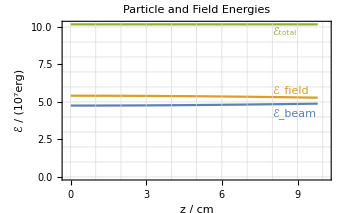

```mathematica
ListPlot[Transpose[{zs,#}]&/@Transpose@Drop[#,-2]&@(nrg44/10^7),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{8,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{8,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{8,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,10],Range[0,10]}
]
```

```mathematica
cts=cavLz/beamβ 1/50(Range[0,#-1]&@Length@zs);
```

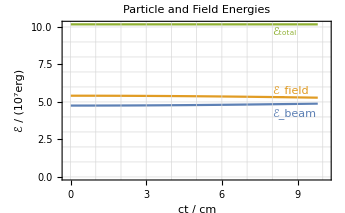

```mathematica
ListPlot[Transpose[{cts,#}]&/@Transpose@Drop[#,-2]&@(nrg44/10^7),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{8,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{8,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{8,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,10],Range[0,10]}
]
```

```mathematica
modes44=Drop[#,-2]&@res44⟦;;,2⟧;
```

```mathematica
nrgF110=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦1⟧}][Transpose@{#⟦1⟧}]&/@modes44
nrgF210=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦2⟧}][Transpose@{#⟦2⟧}]&/@modes44
nrgF120=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦3⟧}][Transpose@{#⟦3⟧}]&/@modes44
nrgF220=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦4⟧}][Transpose@{#⟦4⟧}]&/@modes44
```

{5.41631×10^7,5.41624×10^7,5.41606×10^7,5.41576×10^7,5.41534×10^7,5.41479×10^7,5.41413×10^7,5.41334×10^7,5.41244×10^7,5.41141×10^7,5.41027×10^7,5.409×10^7,5.40762×10^7,5.40612×10^7,5.40451×10^7,5.40278×10^7,5.40093×10^7,5.39896×10^7,5.39688×10^7,5.39469×10^7,5.39239×10^7,5.38997×10^7,5.38745×10^7,5.38481×10^7,5.38206×10^7,5.37921×10^7,5.37625×10^7,5.37318×10^7,5.37002×10^7,5.36674×10^7,5.36337×10^7,5.35989×10^7,5.35632×10^7,5.35265×10^7,5.34888×10^7,5.34502×10^7,5.34106×10^7,5.33702×10^7,5.33288×10^7,5.32865×10^7,5.32434×10^7,5.31995×10^7,5.31547×10^7,5.3109×10^7,5.30626×10^7,5.30154×10^7,5.29675×10^7,5.29188×10^7,5.28694×10^7,5.28193×10^7}

{0.,6.08313,24.3273,54.717,97.2257,151.817,218.443,297.046,387.558,489.9,603.984,729.709,866.968,1015.64,1175.6,1346.7,1528.8,1721.73,1925.34,2139.44,2363.84,2598.36,2842.78,3096.9,3360.49,3633.32,3915.16,4205.76,4504.86,4812.21,5127.55,5450.58,5781.04,6118.63,6463.06,6814.03,7171.23,7534.35,7903.08,8277.09,8656.06,9039.66,9427.54,9819.38,10214.8,10613.5,11015.2,11419.4,11825.8,12234.}

{0.,6.08313,24.3257,54.7071,97.1929,151.735,218.271,296.725,387.008,489.018,602.638,727.738,864.177,1011.8,1170.43,1339.9,1520.01,1710.56,1911.32,2122.08,2342.58,2572.58,2811.81,3060.01,3316.89,3582.15,3855.5,4136.61,4425.18,4720.88,5023.35,5332.27,5647.27,5968.,6294.09,6625.17,6960.87,7300.79,7644.55,7991.76,8342.01,8694.92,9050.08,9407.08,9765.51,10125.,10485.,10845.3,11205.4,11564.8}

{0.,2.0874,8.34625,18.7665,33.3312,52.0169,74.7934,101.624,132.465,167.266,205.972,248.52,294.84,344.858,398.493,455.658,516.26,580.202,647.379,717.683,791.001,867.213,946.197,1027.82,1111.96,1198.47,1287.22,1378.06,1470.84,1565.42,1661.63,1759.33,1858.36,1958.56,2059.76,2161.79,2264.51,2367.73,2471.3,2575.03,2678.78,2782.36,2885.61,2988.37,3090.46,3191.72,3292.,3391.11,3488.92,3585.24}

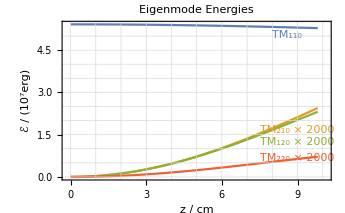

```mathematica
ListPlot[Transpose[{zs,#}]&/@(1/10^7{nrgF110,2 10^3 nrgF210,2 10^3 nrgF120,2 10^3 nrgF220}),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{8,5.2},{-1,1}],
Text[Style["TM_210 × 2000",ColorData[97,2]],{7.5,1.5},{-1,-1},dir[24Degree]],
Text[Style["TM_120 × 2000",ColorData[97,3]],{7.5,1.4},{-1,1},dir[20Degree]],
Text[Style["TM_220 × 2000",ColorData[97,4]],{7.5,0.5},{-1,-1},dir[7Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,10],Range[0,6,0.5]}
]
```

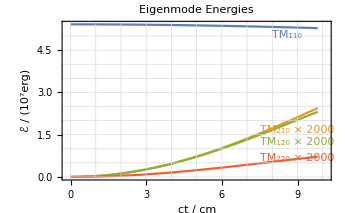

```mathematica
ListPlot[Transpose[{cts,#}]&/@(1/10^7{nrgF110,2 10^3 nrgF210,2 10^3 nrgF120,2 10^3 nrgF220}),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{8,5.2},{-1,1}],
Text[Style["TM_210 × 2000",ColorData[97,2]],{7.5,1.5},{-1,-1},dir[24Degree]],
Text[Style["TM_120 × 2000",ColorData[97,3]],{7.5,1.4},{-1,1},dir[20Degree]],
Text[Style["TM_220 × 2000",ColorData[97,4]],{7.5,0.5},{-1,-1},dir[7Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,10],Range[0,6,0.5]}
]
```

```mathematica
ParticleWeight=4 3 10^11;
MeC=ParticleWeight (MeMKS×10^3)CLight;
EOverC=ParticleWeight QeOverC;
```

```mathematica
Ps=beamβγ MeC;
```

```mathematica
oneZinit={
{cavLx/2,0,cavLy/2,0,0,Ps}
};
```

```mathematica
res41=CrossCavityList[cavLx,cavLy,cavLz][fourModes,cavLz/beamβ 1/50,51][oneZinit,fourAinit,ReportGamma->True]
nrg41=EnergyPF[cavLx,cavLy,cavLz][fourModes][Transpose@First@#,Transpose@Last@#]&/@res41;
NumberForm[#,16]&@TableForm@nrg41
```

{50.}

{50.0004}

{50.0017}

{50.0038}

{50.0067}

{50.0105}

{50.015}

{50.0205}

{50.0267}

{50.0338}

{50.0417}

{50.0504}

{50.06}

{50.0703}

{50.0815}

{50.0935}

{50.1062}

{50.1198}

{50.1341}

{50.1493}

{50.1652}

{50.1818}

{50.1993}

{50.2175}

{50.2364}

{50.2561}

{50.2765}

{50.2977}

{50.3195}

{50.3421}

{50.3654}

{50.3893}

{50.414}

{50.4393}

{50.4652}

{50.4918}

{50.5191}

{50.547}

{50.5755}

{50.6046}

{50.6343}

{50.6645}

{50.6954}

{50.7268}

{50.7587}

{50.7912}

{50.8241}

{50.8576}

{50.8916}

{50.9261}

{50.9435}

{{{{25.,0.,20.,0.,0,0.00163823}},{{3668.26,0},{0,0},{0,0},{0,0}}},{{{25.,-1.42515×10^-22,20.,6.78314×10^-23,0.2,0.00163824}},{{3667.54,-9.46718×10^-8},{-9.31973×10^-18,-1.23659×10^-24},{3.54863×10^-18,4.70838×10^-25},{-1.1413×10^-33,-1.51424×10^-40}}},{{{25.,-2.84966×10^-22,20.,1.35633×10^-22,0.400003,0.00163828}},{{3665.4,-1.89305×10^-7},{-3.72708×10^-17,-2.47209×10^-24},{1.41905×10^-17,9.4114×10^-25},{-4.56337×10^-33,-3.02604×10^-40}}},{{{25.,-4.2729×10^-22,20.,2.03373×10^-22,0.600006,0.00163835}},{{3661.84,-2.83862×10^-7},{-8.38288×10^-17,-3.70544×10^-24},{3.19134×10^-17,1.41037×10^-24},{-1.02607×10^-32,-4.53296×10^-40}}},{{{25.,-5.69421×10^-22,20.,2.71023×10^-22,0.800012,0.00163845}},{{3656.85,-3.78304×10^-7},{-1.48953×10^-16,-4.93554×10^-24},{5.66972×10^-17,1.87799×10^-24},{-1.8224×10^-32,-6.03254×10^-40}}},{{{25.,-7.11297×10^-22,20.,3.3855×10^-22,1.00002,0.00163857}},{{3650.43,-4.72592×10^-7},{-2.32586×10^-16,-6.16132×10^-24},{8.85135×10^-17,2.34346×10^-24},{-2.84406×10^-32,-7.52238×10^-40}}},{{{25.,-8.52852×10^-22,20.,4.05924×10^-22,1.20003,0.00163872}},{{3642.6,-5.6669×10^-7},{-3.34655×10^-16,-7.38169×10^-24},{1.27326×10^-16,2.80625×10^-24},{-4.08937×10^-32,-9.00004×10^-40}}},{{{25.,-9.94022×10^-22,20.,4.73116×10^-22,1.40004,0.0016389}},{{3633.35,-6.60558×10^-7},{-4.55071×10^-16,-8.59559×10^-24},{1.7309×10^-16,3.26583×10^-24},{-5.55634×10^-32,-1.04632×10^-39}}},{{{25.,-1.13474×10^-21,20.,5.40095×10^-22,1.60005,0.0016391}},{{3622.69,-7.54158×10^-7},{-5.93727×10^-16,-9.80194×10^-24},{2.25754×10^-16,3.72167×10^-24},{-7.24258×10^-32,-1.19093×10^-39}}},{{{25.,-1.27495×10^-21,20.,6.0683×10^-22,1.80006,0.00163934}},{{3610.62,-8.47453×10^-7},{-7.50502×10^-16,-1.09997×10^-23},{2.85257×10^-16,4.17326×10^-24},{-9.14537×10^-32,-1.33362×10^-39}}},{{{25.,-1.41459×10^-21,20.,6.73291×10^-22,2.00008,0.00163959}},{{3597.15,-9.40405×10^-7},{-9.25258×10^-16,-1.21878×10^-23},{3.5153×10^-16,4.62007×10^-24},{-1.12616×10^-31,-1.47416×10^-39}}},{{{25.,-1.55359×10^-21,20.,7.39449×10^-22,2.2001,0.00163988}},{{3582.27,-1.03298×10^-6},{-1.11784×10^-15,-1.33652×10^-23},{4.245×10^-16,5.06159×10^-24},{-1.35879×10^-31,-1.61231×10^-39}}},{{{25.,-1.69188×10^-21,20.,8.05273×10^-22,2.40012,0.00164019}},{{3566.01,-1.12513×10^-6},{-1.32809×10^-15,-1.45308×10^-23},{5.0408×10^-16,5.49733×10^-24},{-1.61205×10^-31,-1.74784×10^-39}}},{{{25.,-1.82941×10^-21,20.,8.70734×10^-22,2.60014,0.00164053}},{{3548.36,-1.21683×10^-6},{-1.5558×10^-15,-1.56838×10^-23},{5.90182×10^-16,5.92676×10^-24},{-1.88553×10^-31,-1.88055×10^-39}}},{{{25.,-1.96612×10^-21,20.,9.35802×10^-22,2.80016,0.0016409}},{{3529.33,-1.30803×10^-6},{-1.80079×10^-15,-1.68229×10^-23},{6.82705×10^-16,6.34942×10^-24},{-2.17878×10^-31,-2.01022×10^-39}}},{{{25.,-2.10194×10^-21,20.,1.00045×10^-21,3.00018,0.00164129}},{{3508.93,-1.39871×10^-6},{-2.06285×10^-15,-1.79472×10^-23},{7.81545×10^-16,6.76481×10^-24},{-2.49134×10^-31,-2.13663×10^-39}}},{{{25.,-2.23681×10^-21,20.,1.06464×10^-21,3.20021,0.00164171}},{{3487.17,-1.48882×10^-6},{-2.34173×10^-15,-1.90559×10^-23},{8.86588×10^-16,7.17245×10^-24},{-2.82269×10^-31,-2.25959×10^-39}}},{{{25.,-2.37067×10^-21,20.,1.12836×10^-21,3.40023,0.00164215}},{{3464.06,-1.57832×10^-6},{-2.63719×10^-15,-2.01477×10^-23},{9.97714×10^-16,7.57189×10^-24},{-3.17229×10^-31,-2.37889×10^-39}}},{{{25.,-2.50346×10^-21,20.,1.19157×10^-21,3.60026,0.00164262}},{{3439.6,-1.66719×10^-6},{-2.94898×10^-15,-2.12219×10^-23},{1.11479×10^-15,7.96265×10^-24},{-3.5396×10^-31,-2.49433×10^-39}}},{{{25.,-2.63512×10^-21,20.,1.25424×10^-21,3.80029,0.00164312}},{{3413.8,-1.75538×10^-6},{-3.27682×10^-15,-2.22774×10^-23},{1.2377×10^-15,8.34431×10^-24},{-3.92399×10^-31,-2.60574×10^-39}}},{{{25.,-2.76559×10^-21,20.,1.31634×10^-21,4.00032,0.00164364}},{{3386.69,-1.84287×10^-6},{-3.62042×10^-15,-2.33134×10^-23},{1.36628×10^-15,8.7164×10^-24},{-4.32487×10^-31,-2.71294×10^-39}}},{{{25.,-2.89481×10^-21,20.,1.37786×10^-21,4.20036,0.00164419}},{{3358.25,-1.9296×10^-6},{-3.97949×10^-15,-2.43289×10^-23},{1.5004×10^-15,9.07852×10^-24},{-4.74157×10^-31,-2.81574×10^-39}}},{{{25.,-3.02273×10^-21,20.,1.43875×10^-21,4.40039,0.00164476}},{{3328.52,-2.01556×10^-6},{-4.3537×10^-15,-2.5323×10^-23},{1.6399×10^-15,9.43025×10^-24},{-5.17343×10^-31,-2.91398×10^-39}}},{{{25.,-3.14928×10^-21,20.,1.499×10^-21,4.60043,0.00164536}},{{3297.5,-2.1007×10^-6},{-4.74272×10^-15,-2.62949×10^-23},{1.78461×10^-15,9.77118×10^-24},{-5.61974×10^-31,-3.00751×10^-39}}},{{{25.,-3.27441×10^-21,20.,1.55857×10^-21,4.80047,0.00164598}},{{3265.2,-2.18499×10^-6},{-5.14622×10^-15,-2.72437×10^-23},{1.93439×10^-15,1.01009×10^-23},{-6.07978×10^-31,-3.09617×10^-39}}},{{{25.,-3.39807×10^-21,20.,1.61744×10^-21,5.0005,0.00164662}},{{3231.64,-2.26839×10^-6},{-5.56385×10^-15,-2.81686×10^-23},{2.08904×10^-15,1.04191×10^-23},{-6.55281×10^-31,-3.17982×10^-39}}},{{{25.,-3.52019×10^-21,20.,1.67558×10^-21,5.20055,0.00164729}},{{3196.83,-2.35088×10^-6},{-5.99523×10^-15,-2.90687×10^-23},{2.24841×10^-15,1.07254×10^-23},{-7.03806×10^-31,-3.25832×10^-39}}},{{{25.,-3.64072×10^-21,20.,1.73297×10^-21,5.40059,0.00164798}},{{3160.78,-2.43241×10^-6},{-6.43998×10^-15,-2.99433×10^-23},{2.41229×10^-15,1.10193×10^-23},{-7.53475×10^-31,-3.33154×10^-39}}},{{{25.,-3.75961×10^-21,20.,1.78959×10^-21,5.60063,0.0016487}},{{3123.51,-2.51296×10^-6},{-6.89772×10^-15,-3.07916×10^-23},{2.58051×10^-15,1.13007×10^-23},{-8.04207×10^-31,-3.39938×10^-39}}},{{{25.,-3.87681×10^-21,20.,1.8454×10^-21,5.80068,0.00164944}},{{3085.03,-2.59249×10^-6},{-7.36804×10^-15,-3.16128×10^-23},{2.75288×10^-15,1.15691×10^-23},{-8.5592×10^-31,-3.46171×10^-39}}},{{{25.,-3.99226×10^-21,20.,1.90038×10^-21,6.00072,0.0016502}},{{3045.37,-2.67097×10^-6},{-7.85053×10^-15,-3.24063×10^-23},{2.92919×10^-15,1.18243×10^-23},{-9.0853×10^-31,-3.51843×10^-39}}},{{{25.,-4.10591×10^-21,20.,1.95451×10^-21,6.20077,0.00165099}},{{3004.52,-2.74838×10^-6},{-8.34477×10^-15,-3.31713×10^-23},{3.10925×10^-15,1.20659×10^-23},{-9.61952×10^-31,-3.56946×10^-39}}},{{{25.,-4.21771×10^-21,20.,2.00777×10^-21,6.40082,0.0016518}},{{2962.52,-2.82466×10^-6},{-8.85031×10^-15,-3.39071×10^-23},{3.29284×10^-15,1.22937×10^-23},{-1.0161×10^-30,-3.61472×10^-39}}},{{{25.,-4.3276×10^-21,20.,2.06012×10^-21,6.60087,0.00165262}},{{2919.38,-2.89981×10^-6},{-9.36673×10^-15,-3.46132×10^-23},{3.47976×10^-15,1.25075×10^-23},{-1.07089×10^-30,-3.65412×10^-39}}},{{{25.,-4.43555×10^-21,20.,2.11156×10^-21,6.80092,0.00165348}},{{2875.12,-2.97378×10^-6},{-9.89356×10^-15,-3.52889×10^-23},{3.6698×10^-15,1.27069×10^-23},{-1.12622×10^-30,-3.68761×10^-39}}},{{{25.,-4.5415×10^-21,20.,2.16205×10^-21,7.00098,0.00165435}},{{2829.74,-3.04655×10^-6},{-1.04303×10^-14,-3.59336×10^-23},{3.86273×10^-15,1.28918×10^-23},{-1.18202×10^-30,-3.71512×10^-39}}},{{{25.,-4.6454×10^-21,20.,2.21157×10^-21,7.20103,0.00165524}},{{2783.28,-3.11808×10^-6},{-1.09766×10^-14,-3.65467×10^-23},{4.05834×10^-15,1.30619×10^-23},{-1.23818×10^-30,-3.73663×10^-39}}},{{{25.,-4.74721×10^-21,20.,2.26011×10^-21,7.40109,0.00165616}},{{2735.76,-3.18836×10^-6},{-1.15319×10^-14,-3.71277×10^-23},{4.2564×10^-15,1.3217×10^-23},{-1.29463×10^-30,-3.75208×10^-39}}},{{{25.,-4.84689×10^-21,20.,2.30763×10^-21,7.60114,0.00165709}},{{2687.18,-3.25734×10^-6},{-1.20956×10^-14,-3.76761×10^-23},{4.45669×10^-15,1.33571×10^-23},{-1.35126×10^-30,-3.76146×10^-39}}},{{{25.,-4.94438×10^-21,20.,2.35413×10^-21,7.8012,0.00165804}},{{2637.57,-3.325×10^-6},{-1.26674×10^-14,-3.81914×10^-23},{4.65897×10^-15,1.34818×10^-23},{-1.40798×10^-30,-3.76475×10^-39}}},{{{25.,-5.03965×10^-21,20.,2.39958×10^-21,8.00126,0.00165902}},{{2586.96,-3.39132×10^-6},{-1.32467×10^-14,-3.86731×10^-23},{4.86301×10^-15,1.35911×10^-23},{-1.46471×10^-30,-3.76195×10^-39}}},{{{25.,-5.13265×10^-21,20.,2.44396×10^-21,8.20132,0.00166001}},{{2535.35,-3.45626×10^-6},{-1.3833×10^-14,-3.91209×10^-23},{5.06858×10^-15,1.36848×10^-23},{-1.52135×10^-30,-3.75306×10^-39}}},{{{25.,-5.22334×10^-21,20.,2.48725×10^-21,8.40138,0.00166102}},{{2482.78,-3.51981×10^-6},{-1.44258×10^-14,-3.95343×10^-23},{5.27545×10^-15,1.37629×10^-23},{-1.57782×10^-30,-3.73809×10^-39}}},{{{25.,-5.31168×10^-21,20.,2.52943×10^-21,8.60145,0.00166205}},{{2429.25,-3.58193×10^-6},{-1.50246×10^-14,-3.99129×10^-23},{5.48338×10^-15,1.38252×10^-23},{-1.63401×10^-30,-3.71707×10^-39}}},{{{25.,-5.39763×10^-21,20.,2.57049×10^-21,8.80151,0.00166309}},{{2374.81,-3.6426×10^-6},{-1.56288×10^-14,-4.02565×10^-23},{5.69212×10^-15,1.38716×10^-23},{-1.68983×10^-30,-3.69003×10^-39}}},{{{25.,-5.48116×10^-21,20.,2.61041×10^-21,9.00157,0.00166416}},{{2319.46,-3.70179×10^-6},{-1.62379×10^-14,-4.05648×10^-23},{5.90145×10^-15,1.39022×10^-23},{-1.74521×10^-30,-3.65702×10^-39}}},{{{25.,-5.56222×10^-21,20.,2.64917×10^-21,9.20164,0.00166524}},{{2263.23,-3.75949×10^-6},{-1.68514×10^-14,-4.08374×10^-23},{6.11112×10^-15,1.39169×10^-23},{-1.80004×10^-30,-3.61809×10^-39}}},{{{25.,-5.64078×10^-21,20.,2.68676×10^-21,9.40171,0.00166634}},{{2206.14,-3.81567×10^-6},{-1.74688×10^-14,-4.10741×10^-23},{6.32089×10^-15,1.39156×10^-23},{-1.85425×10^-30,-3.57331×10^-39}}},{{{25.,-5.71681×10^-21,20.,2.72315×10^-21,9.60177,0.00166745}},{{2148.21,-3.8703×10^-6},{-1.80894×10^-14,-4.12747×10^-23},{6.53052×10^-15,1.38984×10^-23},{-1.90773×10^-30,-3.52273×10^-39}}},{{{25.,-5.79027×10^-21,20.,2.75834×10^-21,9.80184,0.00166858}},{{2089.48,-3.92336×10^-6},{-1.87128×10^-14,-4.14391×10^-23},{6.73977×10^-15,1.38653×10^-23},{-1.96041×10^-30,-3.46646×10^-39}}},{{{25.,-2.31861×10^-21,20.,1.09412×10^-21,10.0019,0.00166915}},{{2028.51,-4.16712×10^-6},{-1.88723×10^-14,2.02739×10^-23},{6.77093×10^-15,-9.73003×10^-24},{-1.95512×10^-30,4.16806×10^-39}}},{{{25.,-2.31861×10^-21,20.,1.09412×10^-21,10.2019,0.00166915}},{{1965.29,-4.22076×10^-6},{-1.85585×10^-14,2.13651×10^-23},{6.62043×10^-15,-1.02389×10^-23},{-1.89073×10^-30,4.37467×10^-39}}}}

4.700874944192899×10^7 | 5.416305233812386×10^7 | 1.011718017800529×10^8
4.700957174144152×10^7 | 5.416223000782281×10^7 | 1.011718017492643×10^8
4.701203830686858×10^7 | 5.415976332942031×10^7 | 1.011718016362889×10^8
4.70161481392929×10^7 | 5.415565327444752×10^7 | 1.011718014137404×10^8
4.702189957467448×10^7 | 5.414990147971221×10^7 | 1.011718010543867×10^8
4.702929028452395×10^7 | 5.414251024667204×10^7 | 1.01171800531196×10^8
4.703831727684497×10^7 | 5.413348254053874×10^7 | 1.011717998173837×10^8
4.704897689734472×10^7 | 5.412282198911337×10^7 | 1.011717988864581×10^8
4.706126483091282×10^7 | 5.411053288135306×10^7 | 1.011717977122659×10^8
4.707517610336707×10^7 | 5.409662016566971×10^7 | 1.011717962690368×10^8
4.709070508346618×10^7 | 5.408108944796161×10^7 | 1.011717945314278×10^8
4.710784548518829×10^7 | 5.406394698937825×10^7 | 1.011717924745665×10^8
4.712659037027422×10^7 | 5.404519970381925×10^7 | 1.011717900740935×10^8
4.714693215103481×10^7 | 5.402485515516881×10^7 | 1.011717873062036×10^8
4.716886259342092×10^7 | 5.4002921554266×10^7 | 1.011717841476869×10^8
4.719237282035494×10^7 | 5.397940775561286×10^7 | 1.011717805759678×10^8
4.721745331532249×10^7 | 5.395432325382073×10^7 | 1.011717765691432×10^8
4.724409392622283×10^7 | 5.392767817979705×10^7 | 1.011717721060199×10^8
4.727228386947651×10^7 | 5.389948329667346×10^7 | 1.0117176716615×10^8
4.730201173438834×10^7 | 5.386974999547722×10^7 | 1.011717617298656×10^8
4.733326548776442×10^7 | 5.383849029054714×10^7 | 1.011717557783116×10^8
4.736603247878077×10^7 | 5.380571681469669×10^7 | 1.011717492934774×10^8
4.7400299444102×10^7 | 5.377144281412512×10^7 | 1.011717422582271×10^8
4.743605251324789×10^7 | 5.373568214307959×10^7 | 1.011717346563275×10^8
4.747327721420559×10^7 | 5.369844925826969×10^7 | 1.011717264724753×10^8
4.75119584792853×10^7 | 5.365975921303713×10^7 | 1.011717176923224×10^8
4.755208065121693×10^7 | 5.361962765128243×10^7 | 1.011717083024994×10^8
4.759362748948547×10^7 | 5.357807080115153×10^7 | 1.01171698290637×10^8
4.76365821769024×10^7 | 5.353510546848428×10^7 | 1.011716876453867×10^8
4.768092732641035×10^7 | 5.349074903002804×10^7 | 1.011716763564384×10^8
4.772664498811869×10^7 | 5.344501942641866×10^7 | 1.011716644145374×10^8
4.777371665656652×10^7 | 5.339793515493178×10^7 | 1.011716518114983×10^8
4.782212327821099×10^7 | 5.334951526200752×10^7 | 1.011716385402185×10^8
4.787184525913713×10^7 | 5.329977933555127×10^7 | 1.011716245946884×10^8
4.792286247298654×10^7 | 5.324874749701403×10^7 | 1.011716099700006×10^8
4.797515426910167×10^7 | 5.319644039325517×10^7 | 1.011715946623568×10^8
4.802869948088223×10^7 | 5.314287918819112×10^7 | 1.011715786690733×10^8
4.808347643435054×10^7 | 5.308808555423328×10^7 | 1.011715619885838×10^8
4.813946295692226×10^7 | 5.303208166351853×10^7 | 1.011715446204408×10^8
4.819663638637898×10^7 | 5.297489017893611×10^7 | 1.011715265653151×10^8
4.825497358003917×10^7 | 5.291653424495424×10^7 | 1.011715078249934×10^8
4.831445092412332×10^7 | 5.285703747825041×10^7 | 1.011714884023737×10^8
4.837504434331033×10^7 | 5.279642395814903×10^7 | 1.011714683014594×10^8
4.843672931048037×10^7 | 5.27347182168703×10^7 | 1.011714475273507×10^8
4.849948085664077×10^7 | 5.267194522959436×10^7 | 1.011714260862351×10^8
4.856327358103107×10^7 | 5.260813040434479×10^7 | 1.011714039853759×10^8
4.86280816614026×10^7 | 5.254329957169521×10^7 | 1.011713812330978×10^8
4.869387886446896×10^7 | 5.247747897430374×10^7 | 1.011713578387727×10^8
4.876063855652298×10^7 | 5.241069525627918×10^7 | 1.011713338128021×10^8
4.882833371421556×10^7 | 5.23429754523833×10^7 | 1.011713091665989×10^8
5.00495379309311×10^7 | 5.578708656017461×10^7 | 1.058366244911057×10^8
5.00495379309311×10^7 | 5.578708656017461×10^7 | 1.058366244911057×10^8

```mathematica
zs=Drop[#,-2]&@res41⟦;;,1,1,5⟧;
```

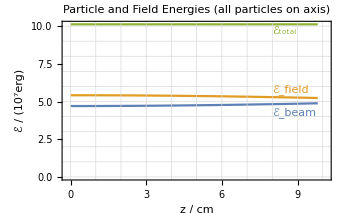

```mathematica
ListPlot[Transpose[{zs,#}]&/@Transpose@Drop[#,-2]&@(nrg41/10^7),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Particle and Field Energies (all particles on axis)",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{8,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{8,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{8,10.0},{-1,1}]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->Directive[LightGray],
GridLines->{Range[0,10],Range[0,10]}
]
```

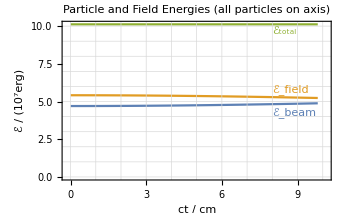

```mathematica
ListPlot[Transpose[{cts,#}]&/@Transpose@Drop[#,-2]&@(nrg41/10^7),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Particle and Field Energies (all particles on axis)",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{8,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{8,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{8,10.0},{-1,1}]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->Directive[LightGray],
GridLines->{Range[0,10],Range[0,10]}
]
```

```mathematica
modes41=Drop[#,-2]&@res41⟦;;,2⟧;
```

```mathematica
nrgF110x=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦1⟧}][Transpose@{#⟦1⟧}]&/@modes41
nrgF210x=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦2⟧}][Transpose@{#⟦2⟧}]&/@modes41
nrgF120x=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦3⟧}][Transpose@{#⟦3⟧}]&/@modes41
nrgF220x=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦4⟧}][Transpose@{#⟦4⟧}]&/@modes41
```

{5.41631×10^7,5.41622×10^7,5.41598×10^7,5.41557×10^7,5.41499×10^7,5.41425×10^7,5.41335×10^7,5.41228×10^7,5.41105×10^7,5.40966×10^7,5.40811×10^7,5.40639×10^7,5.40452×10^7,5.40249×10^7,5.40029×10^7,5.39794×10^7,5.39543×10^7,5.39277×10^7,5.38995×10^7,5.38697×10^7,5.38385×10^7,5.38057×10^7,5.37714×10^7,5.37357×10^7,5.36984×10^7,5.36598×10^7,5.36196×10^7,5.35781×10^7,5.35351×10^7,5.34907×10^7,5.3445×10^7,5.33979×10^7,5.33495×10^7,5.32998×10^7,5.32487×10^7,5.31964×10^7,5.31429×10^7,5.30881×10^7,5.30321×10^7,5.29749×10^7,5.29165×10^7,5.2857×10^7,5.27964×10^7,5.27347×10^7,5.26719×10^7,5.26081×10^7,5.25433×10^7,5.24775×10^7,5.24107×10^7,5.2343×10^7}

{0.,3.45481×10^-30,1.38163×10^-29,3.10756×10^-29,5.52177×10^-29,8.62216×10^-29,1.2406×10^-28,1.687×10^-28,2.20103×10^-28,2.78223×10^-28,3.4301×10^-28,4.14407×10^-28,4.92351×10^-28,5.76774×10^-28,6.67602×10^-28,7.64755×10^-28,8.68148×10^-28,9.77691×10^-28,1.09329×10^-27,1.21484×10^-27,1.34223×10^-27,1.47535×10^-27,1.6141×10^-27,1.75834×10^-27,1.90794×10^-27,2.06278×10^-27,2.22273×10^-27,2.38763×10^-27,2.55735×10^-27,2.73174×10^-27,2.91064×10^-27,3.09389×10^-27,3.28135×10^-27,3.47283×10^-27,3.66817×10^-27,3.86721×10^-27,4.06976×10^-27,4.27565×10^-27,4.4847×10^-27,4.69672×10^-27,4.91153×10^-27,5.12894×10^-27,5.34876×10^-27,5.57079×10^-27,5.79484×10^-27,6.02072×10^-27,6.24821×10^-27,6.47714×10^-27,6.70728×10^-27,6.93845×10^-27}

{0.,5.00897×10^-31,2.00303×10^-30,4.5047×10^-30,8.00308×10^-30,1.24942×10^-29,1.79729×10^-29,2.44329×10^-29,3.1867×10^-29,4.02665×10^-29,4.96219×10^-29,5.99225×10^-29,7.11565×10^-29,8.33112×10^-29,9.63725×10^-29,1.10326×10^-28,1.25154×10^-28,1.40842×10^-28,1.57371×10^-28,1.74721×10^-28,1.92874×10^-28,2.11808×10^-28,2.31502×10^-28,2.51933×10^-28,2.73078×10^-28,2.94912×10^-28,3.17411×10^-28,3.40548×10^-28,3.64299×10^-28,3.88634×10^-28,4.13526×10^-28,4.38948×10^-28,4.64869×10^-28,4.9126×10^-28,5.18091×10^-28,5.45331×10^-28,5.72949×10^-28,6.00913×10^-28,6.29192×10^-28,6.57752×10^-28,6.86562×10^-28,7.15588×10^-28,7.44797×10^-28,7.74155×10^-28,8.0363×10^-28,8.33186×10^-28,8.62791×10^-28,8.9241×10^-28,9.2201×10^-28,9.51556×10^-28}

{0.,5.18139×10^-62,2.07174×10^-61,4.6583×10^-61,8.27367×10^-61,1.2912×10^-60,1.85659×10^-60,2.52261×10^-60,3.28819×10^-60,4.15209×10^-60,5.11293×10^-60,6.16913×10^-60,7.31901×10^-60,8.56069×10^-60,9.89217×10^-60,1.13113×10^-59,1.28158×10^-59,1.44032×10^-59,1.60709×10^-59,1.78163×10^-59,1.96365×10^-59,2.15286×10^-59,2.34895×10^-59,2.55161×10^-59,2.7605×10^-59,2.97529×10^-59,3.19564×10^-59,3.42118×10^-59,3.65154×10^-59,3.88637×10^-59,4.12526×10^-59,4.36785×10^-59,4.61374×10^-59,4.86253×10^-59,5.11381×10^-59,5.36718×10^-59,5.62223×10^-59,5.87855×10^-59,6.13572×10^-59,6.39332×10^-59,6.65095×10^-59,6.90817×10^-59,7.16458×10^-59,7.41976×10^-59,7.67329×10^-59,7.92477×10^-59,8.17379×10^-59,8.41995×10^-59,8.66284×10^-59,8.90208×10^-59}

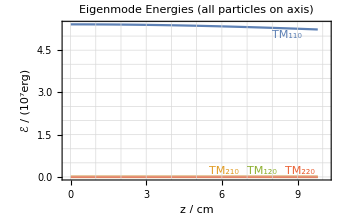

```mathematica
ListPlot[Transpose[{zs,#}]&/@(1/10^7{nrgF110x,2 10^3 nrgF210x,2 10^3 nrgF120x,2 10^3 nrgF220x}),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Eigenmode Energies (all particles on axis)",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{8,5.20},{-1,1}],
Text[Style["TM_210",ColorData[97,2]],{5.5,0.03},{-1,-1}],
Text[Style["TM_120",ColorData[97,3]],{7.0,0.03},{-1,-1}],
Text[Style["TM_220",ColorData[97,4]],{8.5,0.03},{-1,-1}]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->Directive[LightGray],
GridLines->{Range[0,10],Range[0,6,0.5]}
]
```

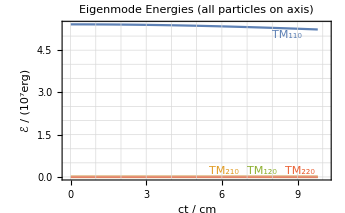

```mathematica
ListPlot[Transpose[{cts,#}]&/@(1/10^7{nrgF110x,2 10^3 nrgF210x,2 10^3 nrgF120x,2 10^3 nrgF220x}),
Joined->True,PlotRange->{{-0.13,10.13},Automatic},
PlotLabel->"Eigenmode Energies (all particles on axis)",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{8,5.20},{-1,1}],
Text[Style["TM_210",ColorData[97,2]],{5.5,0.03},{-1,-1}],
Text[Style["TM_120",ColorData[97,3]],{7.0,0.03},{-1,-1}],
Text[Style["TM_220",ColorData[97,4]],{8.5,0.03},{-1,-1}]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->Directive[LightGray],
GridLines->{Range[0,10],Range[0,6,0.5]}
]
```

```mathematica
ParticleWeight=3 10^11;
MeC=ParticleWeight (MeMKS×10^3)CLight;
EOverC=ParticleWeight QeOverC;
```

```mathematica
Ps=beamβγ MeC;
```

```mathematica
oneZinit={
{cavLx/2,0,cavLy/2,0,0,Ps}
};
```

#### Test 1 (long cavity)

First we turn off the windowing:

```mathematica
CavityWindow[Lz_][qz_]:=If[0≤qz≤Lz,1,1]
```

```mathematica
res44long=CrossCavityList[cavLx,cavLy,cavLz][fourModes,cavLz/beamβ 1/50,626][fourZinit,fourAinit];
nrg44long=EnergyPF[cavLx,cavLy,cavLz][fourModes][Transpose@First@#,Transpose@Last@#]&/@res44long;
```

```mathematica
zslong=res44long⟦;;,1,1,5⟧;
```

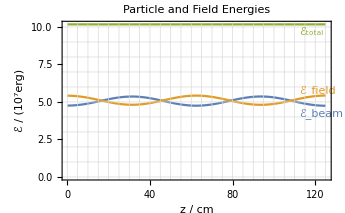

```mathematica
ListPlot[Transpose[{zslong,#}]&/@Transpose@(nrg44long/10^7),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{112,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{112,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{112,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[0,10]}
]
```

```mathematica
ctslong=cavLz/beamβ 1/50(Range[0,#-1]&@Length@zslong);
```

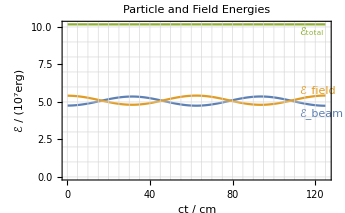

```mathematica
ListPlot[Transpose[{ctslong,#}]&/@Transpose@(nrg44long/10^7),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{112,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{112,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{112,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[0,10]}
]
```

```mathematica
modes44long=res44long⟦;;,2⟧;
```

```mathematica
nrgF110xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦1⟧}][Transpose@{#⟦1⟧}]&/@modes44long;
nrgF210xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦2⟧}][Transpose@{#⟦2⟧}]&/@modes44long;
nrgF120xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦3⟧}][Transpose@{#⟦3⟧}]&/@modes44long;
nrgF220xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦4⟧}][Transpose@{#⟦4⟧}]&/@modes44long;
```

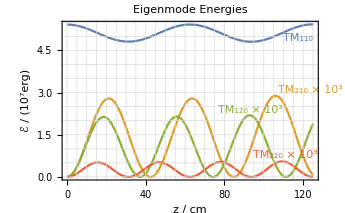

```mathematica
ListPlot[Transpose[{zslong,#}]&/@(1/10^7{nrgF110xl,1 10^3 nrgF210xl,1 10^3 nrgF120xl,1 10^3 nrgF220xl}),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{125,5.1},{1,1}],
Text[Style["TM_210 × 10^3",ColorData[97,2]],{107,2.9},{-0.5,-1},dir[0Degree]],
Text[Style["TM_120 × 10^3",ColorData[97,3]],{93,2.2},{0.30,-1},dir[0Degree]],
Text[Style["TM_220 × 10^3",ColorData[97,4]],{111,0.6},{-0.2,-1},dir[0Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[0,6,0.5]}
]
```

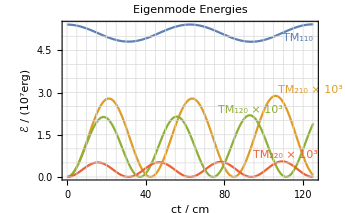

```mathematica
ListPlot[Transpose[{ctslong,#}]&/@(1/10^7{nrgF110xl,1 10^3 nrgF210xl,1 10^3 nrgF120xl,1 10^3 nrgF220xl}),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{125,5.1},{1,1}],
Text[Style["TM_210 × 10^3",ColorData[97,2]],{107,2.9},{-0.5,-1},dir[0Degree]],
Text[Style["TM_120 × 10^3",ColorData[97,3]],{93,2.2},{0.30,-1},dir[0Degree]],
Text[Style["TM_220 × 10^3",ColorData[97,4]],{111,0.6},{-0.2,-1},dir[0Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[0,6,0.5]}
]
```

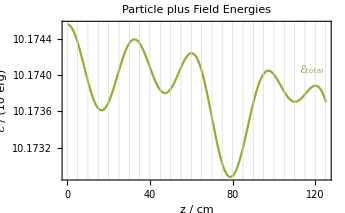

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,3⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle plus Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_total",ColorData[97,3]],{112,10.174},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,3]},
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[0,10]}
]
```

```mathematica
Sin[3.]^2+(1.-Sin[3.]^2)
```

1.

1.

```mathematica
Sin[3.]^2+Cos[3.]^2
```

1.

1.

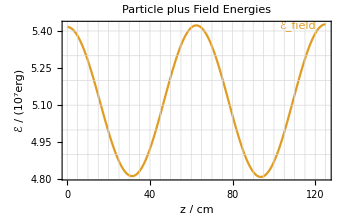

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,2⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle plus Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_field",ColorData[97,2]],{120,5.4},{1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,2]},
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[4,6,0.1]}
]
```

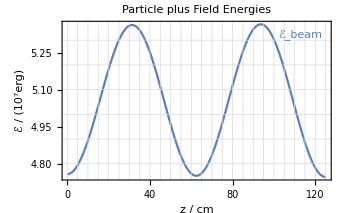

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,1⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle plus Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{102,5.3},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,1]},
GridLinesStyle->LightGray,
GridLines->{Range[0,130,5],Range[4,6,0.1]}
]
```

```mathematica
1/2 ptclβ CLight (2π)/(PillBoxω[cavLx,cavLy,cavLz][1,1,0])
```

31.2285

#### Test 2 (very long cavity)

First we turn off the windowing:

```mathematica
CavityWindow[Lz_][qz_]:=If[0≤qz≤Lz,1,1]
```

```mathematica
res44long=CrossCavityList[cavLx,cavLy,cavLz][fourModes,cavLz/beamβ 1/50,10001][fourZinit,fourAinit];
nrg44long=EnergyPF[cavLx,cavLy,cavLz][fourModes][Transpose@First@#,Transpose@Last@#]&/@res44long;
```

```mathematica
zslong=res44long⟦;;,1,1,5⟧;
```

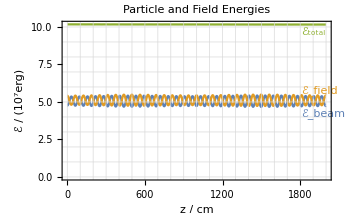

```mathematica
ListPlot[Transpose[{zslong,#}]&/@Transpose@(nrg44long/10^7),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{1805,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{1805,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{1805,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,10]}
]
```

```mathematica
ctslong=cavLz/beamβ 1/50(Range[0,#-1]&@Length@zslong);
```

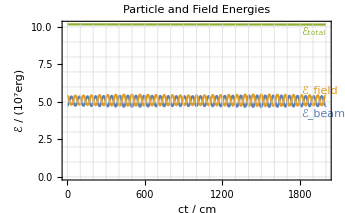

```mathematica
ListPlot[Transpose[{ctslong,#}]&/@Transpose@(nrg44long/10^7),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{1805,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{1805,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{1805,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,10]}
]
```

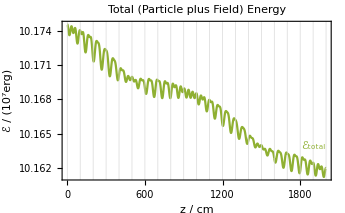

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,3⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Total (Particle plus Field) Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_total",ColorData[97,3]],{1805,10.1635},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,3]},
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,10]}
]
```

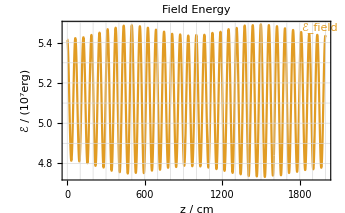

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,2⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Field Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_field",ColorData[97,2]],{1810,5.45},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,2]},
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[4,6,0.1]}
]
```

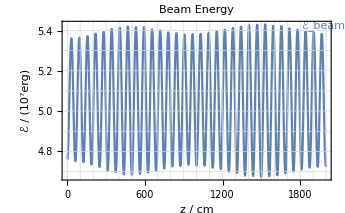

```mathematica
ListPlot[Transpose[{zslong,nrg44long⟦;;,1⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Beam Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{1810,5.40},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,1]},
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[4,6,0.1]}
]
```

```mathematica
modes44long=res44long⟦;;,2⟧;
```

```mathematica
nrgF110xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦1⟧}][Transpose@{#⟦1⟧}]&/@modes44long;
nrgF210xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦2⟧}][Transpose@{#⟦2⟧}]&/@modes44long;
nrgF120xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦3⟧}][Transpose@{#⟦3⟧}]&/@modes44long;
nrgF220xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦4⟧}][Transpose@{#⟦4⟧}]&/@modes44long;
```

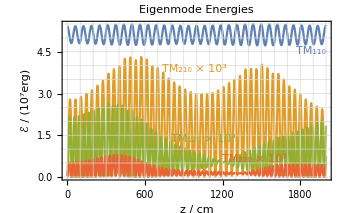

```mathematica
ListPlot[Transpose[{zslong,#}]&/@(1/10^7{nrgF110xl,1 10^3 nrgF210xl,1 10^3 nrgF120xl,1 10^3 nrgF220xl}),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{2000,4.7},{1,1}],
Text[Style["TM_210 × 10^3",ColorData[97,2]],{730,3.7},{-1,-1},dir[0Degree]],
Text[Style["TM_120 × 10^3",ColorData[97,3]],{800,1.2},{-1,-1},dir[0Degree]],
Text[Style["TM_220 × 10^3",ColorData[97,4]],{1700,0.45},{0.5,-1},dir[0Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,6,0.5]}
]
```

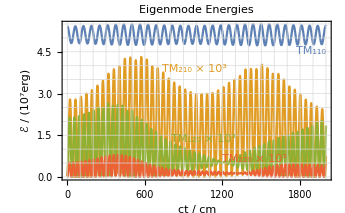

```mathematica
ListPlot[Transpose[{ctslong,#}]&/@(1/10^7{nrgF110xl,1 10^3 nrgF210xl,1 10^3 nrgF120xl,1 10^3 nrgF220xl}),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"ct / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{2000,4.7},{1,1}],
Text[Style["TM_210 × 10^3",ColorData[97,2]],{730,3.7},{-1,-1},dir[0Degree]],
Text[Style["TM_120 × 10^3",ColorData[97,3]],{800,1.2},{-1,-1},dir[0Degree]],
Text[Style["TM_220 × 10^3",ColorData[97,4]],{1700,0.45},{0.5,-1},dir[0Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,6,0.5]}
]
```

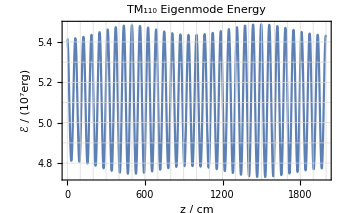

```mathematica
ListPlot[Transpose[{zslong,1/10^7 nrgF110xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_110 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,1]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[4,6,0.1]}
]
```

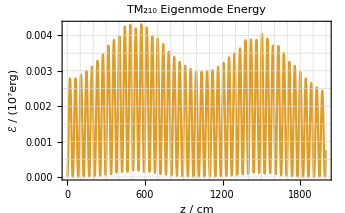

```mathematica
ListPlot[Transpose[{zslong,1/10^7 nrgF210xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_210 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,2]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,0.0050,0.0005]}
]
```

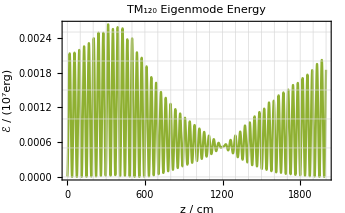

```mathematica
ListPlot[Transpose[{zslong,1/10^7 nrgF120xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_120 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,3]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,0.0050,0.0005]}
]
```

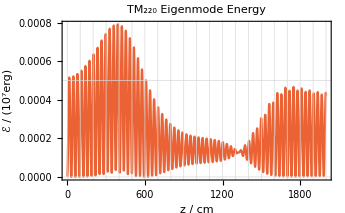

```mathematica
ListPlot[Transpose[{zslong,1/10^7 nrgF220xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_220 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,4]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,2000,100],Range[0,0.0050,0.0005]}
]
```

#### Test 3 (extra long cavity)

First we turn off the windowing:

```mathematica
CavityWindow[Lz_][qz_]:=If[0≤qz≤Lz,1,1]
```

```mathematica
res44Xlong=CrossCavityList[cavLx,cavLy,cavLz][fourModes,cavLz/beamβ 1/50,20001][fourZinit,fourAinit];
nrg44Xlong=EnergyPF[cavLx,cavLy,cavLz][fourModes][Transpose@First@#,Transpose@Last@#]&/@res44Xlong;
```

```mathematica
zsXlong=res44Xlong⟦;;,1,1,5⟧;
```

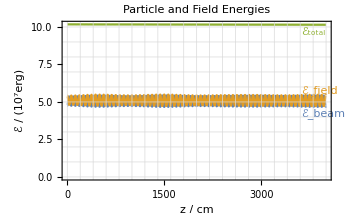

```mathematica
ListPlot[Transpose[{zsXlong,#}]&/@Transpose@(nrg44Xlong/10^7),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Particle and Field Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{3610,4.6},{-1,1}],
Text[Style["ℰ_field",ColorData[97,2]],{3610,5.4},{-1,-1}],
Text[Style["ℰ_total",ColorData[97,3]],{3610,10.0},{-1,1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,10]}
]
```

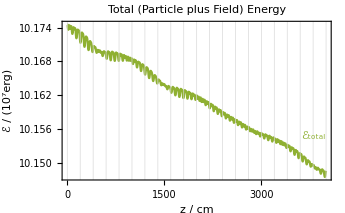

```mathematica
ListPlot[Transpose[{zsXlong,nrg44Xlong⟦;;,3⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Total (Particle plus Field) Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_total",ColorData[97,3]],{3610,10.1539},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,3]},
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,10]}
]
```

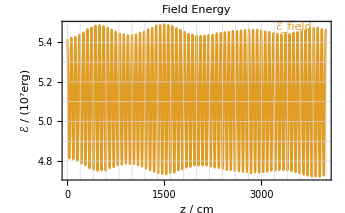

```mathematica
ListPlot[Transpose[{zsXlong,nrg44Xlong⟦;;,2⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Field Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_field",ColorData[97,2]],{3220,5.45},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,2]},
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[4,6,0.1]}
]
```

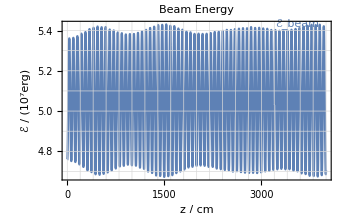

```mathematica
ListPlot[Transpose[{zsXlong,nrg44Xlong⟦;;,1⟧/10^7}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Beam Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["ℰ_beam",ColorData[97,1]],{3220,5.41},{-1,-1}]
},
BaseStyle->{FontFamily->"Palatino",FontSize->10},
ImageSize->345,
PlotStyle->{ColorData[97,1]},
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[4,6,0.1]}
]
```

```mathematica
modes44Xlong=res44Xlong⟦;;,2⟧;
```

```mathematica
nrgF110xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦1⟧}][Transpose@{#⟦1⟧}]&/@modes44Xlong;
nrgF210xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦2⟧}][Transpose@{#⟦2⟧}]&/@modes44Xlong;
nrgF120xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦3⟧}][Transpose@{#⟦3⟧}]&/@modes44Xlong;
nrgF220xl=EnergyF[cavLx,cavLy,cavLz][{fourModes⟦4⟧}][Transpose@{#⟦4⟧}]&/@modes44Xlong;
```

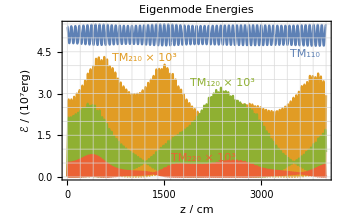

```mathematica
ListPlot[Transpose[{zsXlong,#}]&/@(1/10^7{nrgF110xl,1 10^3 nrgF210xl,1 10^3 nrgF120xl,1 10^3 nrgF220xl}),
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"Eigenmode Energies",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
Epilog->{
Text[Style["TM_110",ColorData[97,1]],{3900,4.6},{1,1}],
Text[Style["TM_210 × 10^3",ColorData[97,2]],{1200,4.1},{0,-1},dir[0Degree]],
Text[Style["TM_120 × 10^3",ColorData[97,3]],{2400,3.2},{0,-1},dir[0Degree]],
Text[Style["TM_220 × 10^3",ColorData[97,4]],{2600,0.5},{1,-1},dir[0Degree]]
},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,6,0.5]}
]
```

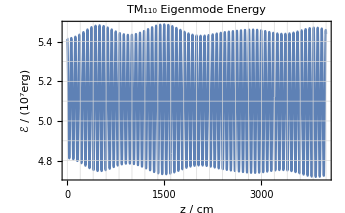

```mathematica
ListPlot[Transpose[{zsXlong,1/10^7 nrgF110xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_110 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,1]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[4,6,0.1]}
]
```

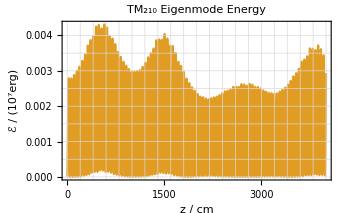

```mathematica
ListPlot[Transpose[{zsXlong,1/10^7 nrgF210xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_210 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,2]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,0.0050,0.0005]}
]
```

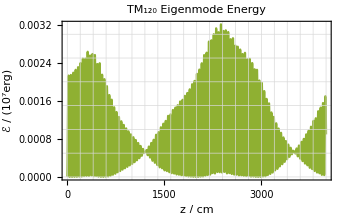

```mathematica
ListPlot[Transpose[{zsXlong,1/10^7 nrgF120xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_120 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,3]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,0.0050,0.0005]}
]
```

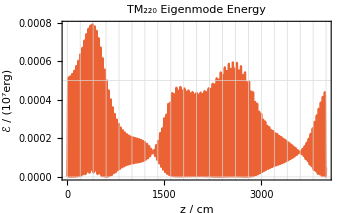

```mathematica
ListPlot[Transpose[{zsXlong,1/10^7 nrgF220xl}],
Joined->True,PlotRange->{Automatic,Automatic},
PlotLabel->"TM_220 Eigenmode Energy",
FrameLabel->{"z / cm","ℰ / (10^7erg)"},
BaseStyle->{FontSize->10,FontFamily->"Palatino"},
PlotStyle->{ColorData[97,4]},
ImageSize->345,
GridLinesStyle->LightGray,
GridLines->{Range[0,4000,200],Range[0,0.0050,0.0005]}
]
```

#### Cavity and Particle Setup

```mathematica
cavLx=10.0;
cavLy=8.0;
cavLz=4.0;
```

```mathematica
oneMode={
{"TM",1,1,0}
};
```

```mathematica
twoModes={
{"TM",1,1,0},
{"TM",1,2,0}
};
```

```mathematica
threeModes={
{"TM",1,1,0},
{"TM",1,2,0},
{"TM",2,1,0}
};
```

```mathematica
oneAinit={
{10^3,0}
};
```

```mathematica
twoAinit={
{10^3,0},
{0,0}
};
```

```mathematica
threeAinit={
{10^3,0},
{0,0},
{0,0}
};
```

```mathematica
beamγ=10.;
beamβ=SRBeta[beamγ];
beamβγ=SRBetaGamma[beamγ];
Ps=beamβγ MeC;
```

```mathematica
oneZinit={
{cavLx/2,0,cavLy/2,0,0,Ps}
};
```

```mathematica
twoZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps}
};
```

```mathematica
threeZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps}
};
```

```mathematica
fourZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

```mathematica
nineZinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps},
{3cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,3cavLy/4,0,0,Ps},
{3cavLx/4,0,cavLy/4,0,0,Ps},
{cavLx/4,0,3cavLy/4,0,0,Ps},
{3cavLx/4,0,3cavLy/4,0,0,Ps}
};
```

```mathematica
EOverC
```

1.60218×10^-20

```mathematica
(*EOverC/=10^6*)
```

#### -size, field rotation)

We can window the fields to the cavity:

```mathematica
(*  ................. ===inCav===  .............................................................................  === qz values ===  ...................  *)
Plus@@#&/@MapThread[{0,0,0,0} GenIntAz[cavLx,cavLy,cavLz][{#1},{#2}][fourZinit⟦;;,1⟧,fourZinit⟦;;,3⟧,{-1.,-1.,-1.,-1.}]&,{twoModes,{1,1}}]
Plus@@#&/@MapThread[{0,0,1,1} GenIntAz[cavLx,cavLy,cavLz][{#1},{#2}][fourZinit⟦;;,1⟧,fourZinit⟦;;,3⟧,{-1.,-1.,1.,1.}]&,{twoModes,{1,1}}]
Plus@@#&/@MapThread[{0,1,1,1} GenIntAz[cavLx,cavLy,cavLz][{#1},{#2}][fourZinit⟦;;,1⟧,fourZinit⟦;;,3⟧,{-1.,1.,1.,1.}]&,{twoModes,{1,1}}]
Plus@@#&/@MapThread[{1,1,1,1} GenIntAz[cavLx,cavLy,cavLz][{#1},{#2}][fourZinit⟦;;,1⟧,fourZinit⟦;;,3⟧,{1.,1.,1.,1.}]&,{twoModes,{1,1}}]
```

{0.,0.}

{1.20711,1.70711}

{1.91421,1.70711}

{2.91421,1.70711}

We can can now set the step-size independent of the number of steps ...

```mathematica
CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/20,20][fourZinit,oneAinit]
```

{{{5.,5.52455×10^-34,4.,6.90569×10^-34,3.989,2.94581×10^-16},{2.57104,6.36624×10^-18,4.,4.88883×10^-34,3.98575,2.87993×10^-16},{5.,3.91453×10^-34,2.08867,7.95011×10^-18,3.98537,2.88052×10^-16},{2.55078,4.51073×10^-18,2.06335,5.63105×10^-18,3.98368,2.83292×10^-16}},{{-426.667,-9.65842×10^-8}}}

```mathematica
CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/20,20][fourZinit,oneAinit]
```

{{{5.,5.52455×10^-34,4.,6.90569×10^-34,3.989,2.94581×10^-16},{2.57104,6.36624×10^-18,4.,4.88883×10^-34,3.98575,2.87993×10^-16},{5.,3.91453×10^-34,2.08867,7.95011×10^-18,3.98537,2.88052×10^-16},{2.55078,4.51073×10^-18,2.06335,5.63105×10^-18,3.98368,2.83292×10^-16}},{{-426.667,-454.827}}}

... but make sure you correct the time-step for the slower-than-light velocity:

```mathematica
CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/20,20][fourZinit,oneAinit]
```

{{{5.,1.03142×10^-33,4.,1.28927×10^-33,4.00915,2.9399×10^-16},{2.57338,1.17712×10^-17,4.,9.20987×10^-34,4.00587,2.87564×10^-16},{5.,7.41113×10^-34,2.09156,1.46191×10^-17,4.00549,2.87616×10^-16},{2.5525,8.44741×10^-18,2.06547,1.04669×10^-17,4.00378,2.82981×10^-16}},{{-435.81,-452.63}}}

If we increase the cavity length to the point where the field rotates a full 360^∘, we can see the particle energy return to it’s initial value.

```mathematica
Ps
```

2.71724×10^-16

```mathematica
With[{f=1.554},
CrossCavity[cavLx,cavLy,f cavLz][oneMode,(f cavLz)/beamβ 1/200,200][fourZinit,oneAinit]]
```

{{{5.,1.9167×10^-33,4.,2.39587×10^-33,6.22096,3.03767×10^-16},{2.59998,2.16032×10^-17,4.,1.73248×10^-33,6.21868,2.94728×10^-16},{5.,1.40302×10^-33,2.12516,2.66224×10^-17,6.21817,2.94918×10^-16},{2.57122,1.57721×10^-17,2.08924,1.93469×10^-17,6.2174,2.88199×10^-16}},{{-1000.,0.0922065}}}

```mathematica
With[{f=3.1078},
CrossCavity[cavLx,cavLy,f cavLz][oneMode,(f cavLz)/beamβ 1/200,200][fourZinit,oneAinit]]
```

{{{5.,-3.83389×10^-33,4.,-4.79236×10^-33,12.4377,2.71726×10^-16},{2.50255,-4.38159×10^-17,4.,-3.42057×10^-33,12.4342,2.71698×10^-16},{5.,-2.756×10^-33,2.00869,-5.43424×10^-17,12.4333,2.71659×10^-16},{2.49451,-3.14235×10^-17,1.99856,-3.8911×10^-17,12.4322,2.7172×10^-16}},{{1000.,0.0189333}}}

#### Test 1 (correct γ, no field rotation implies no energy gain)

Is the initial γ correct? And what happens if we turn off the field rotation?

```mathematica
StepHamPF[Lx_,Ly_,Lz_][mode_List,pfCoupling_,ds_][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,Ax,Ay,As,γmc,Z=Zi,A=Ai},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
γmc=√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
Print@(γmc/MeC);
(*A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];*)
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][3,mode,pfCoupling,ds][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
(*A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];*)
{Z,A}
]
```

```mathematica
{Zfin,Afin}=CrossCavity[cavLx,cavLy,cavLz][oneMode,cavLz/beamβ 1/20,20][oneZinit,oneAinit]
```

{10.}

{10.}

{10.}

«17 more identical outputs»

{{{5.,1.23282×10^-33,4.,1.54103×10^-33,4.,2.71724×10^-16}},{{1000.,6.40871×10^-20}}}

#### Test 2 (energy conservation—one mode, one particle)

What about the energy gain? To check this, we turn the field rotation back on; but we limit that field rotation by using a very short cavity:

```mathematica
StepHamPF[Lx_,Ly_,Lz_][mode_List,pfCoupling_,ds_][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,Ax,Ay,As,γmc,Z=Zi,A=Ai},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
γmc=√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
Print@NumberForm[#,16]&@(γmc/MeC);
Print@NumberForm[#,16]&@HamPF[cavLx,cavLy,cavLz][oneMode][Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][3,mode,pfCoupling,ds][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}
]
```

```mathematica
{cavLx,cavLy,cavLz/20}
{oneMode,(cavLz/20)/beamβ 1/20,20}
{oneZinit,oneAinit}
```

{10.,8.,0.2}

{{{TM,1,1,0}},0.0100504,20}

{{{5.,0,4.,0,0,2.71724×10^-16}},{{1000,0}}}

```mathematica
CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit,ParticleFieldCoupling->False]
```

{10.}

{2.730924488317191×10^-16,126454.3063889574,126454.3063889574}

{10.00000745617001}

{2.730926524540918×10^-16,126454.3063889574,126454.3063889574}

{10.0000298244899}

{2.730932633160173×10^-16,126454.3063889574,126454.3063889574}

{10.00006710438925}

{2.730942814019179×10^-16,126454.3063889574,126454.3063889574}

{10.00011929491739}

{2.730957066858315×10^-16,126454.3063889573,126454.3063889573}

{10.0001863947434}

{2.730975391314116×10^-16,126454.3063889574,126454.3063889574}

{10.00026840215616}

{2.730997786919289×10^-16,126454.3063889574,126454.3063889574}

{10.0003653150644}

{2.731024253102721×10^-16,126454.3063889574,126454.3063889574}

{10.00047713099671}

{2.731054789189495×10^-16,126454.3063889574,126454.3063889574}

{10.00060384710168}

{2.731089394400908×10^-16,126454.3063889573,126454.3063889573}

{10.00074546014789}

{2.731128067854485×10^-16,126454.3063889573,126454.3063889573}

{10.00090196652406}

{2.731170808564011×10^-16,126454.3063889573,126454.3063889573}

{10.00107336223909}

{2.731217615439546×10^-16,126454.3063889573,126454.3063889573}

{10.00125964292218}

{2.731268487287461×10^-16,126454.3063889573,126454.3063889573}

{10.00146080382295}

{2.731323422810463×10^-16,126454.3063889572,126454.3063889572}

{10.00167683981156}

{2.731382420607628×10^-16,126454.3063889572,126454.3063889572}

{10.00190774537882}

{2.73144547917444×10^-16,126454.3063889572,126454.3063889572}

{10.00215351463635}

{2.731512596902826×10^-16,126454.3063889571,126454.3063889571}

{10.00241414131671}

{2.731583772081198×10^-16,126454.3063889571,126454.3063889571}

{10.00268961877359}

{2.731659002894494×10^-16,126454.3063889571,126454.3063889571}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-12.7078}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-15.2486}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-17.7891}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-20.3291}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-22.8686}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-25.4075}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-27.9457}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-30.4832}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-33.02}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-35.5559}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-38.0909}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-40.6249}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-43.1579}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-45.6898}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-48.2205}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-50.75}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit]
```

{10.}

{10.}

{10.}

{10.0001}

{10.0001}

{10.0002}

{10.0003}

{10.0004}

{10.0005}

{10.0006}

{10.0007}

{10.0009}

{10.0011}

{10.0013}

{10.0015}

{10.0017}

{10.0019}

{10.0022}

{10.0024}

{10.0027}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-12.7078}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-15.2486}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-17.7891}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-20.3291}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-22.8686}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-25.4075}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-27.9457}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-30.4832}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-33.02}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-35.5559}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-38.0909}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-40.6249}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-43.1579}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-45.6898}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-48.2205}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-50.75}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit]
```

{10.}

{10.}

{10.}

{10.0001}

{10.0001}

{10.0002}

{10.0003}

{10.0004}

{10.0005}

{10.0006}

{10.0007}

{10.0009}

{10.0011}

{10.0013}

{10.0015}

{10.0017}

{10.0019}

{10.0022}

{10.0024}

{10.0027}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-12.7078}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-15.2486}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-17.7891}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-20.3291}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-22.8686}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-25.4075}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-27.9457}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-30.4832}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-33.02}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-35.5559}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-38.0909}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-40.6249}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-43.1579}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-45.6898}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-48.2205}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-50.75}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][twoModes,(cavLz/20)/beamβ 1/20,5][fourZinit,twoAinit]
```

{10.,10.,10.,10.}

{10.,10.,10.,10.}

{10.,10.,10.,10.}

{10.0001,10.,10.,10.}

{10.0001,10.0001,10.0001,10.0001}

{{{{5.,0.,4.,0.,0,2.71724×10^-16},{2.5,0.,4.,0.,0,2.71724×10^-16},{5.,0.,2.,0.,0,2.71724×10^-16},{2.5,0.,2.,0.,0,2.71724×10^-16}},{{1000,0},{0,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.71724×10^-16},{5.,2.17934×10^-36,2.,4.44891×10^-20,0.01,2.71724×10^-16},{2.5,2.51669×10^-20,2.,3.14586×10^-20,0.01,2.71724×10^-16}},{{999.987,-2.54182},{1.37443×10^-24,2.73506×10^-22}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.71724×10^-16},{5.,4.35862×10^-36,2.,8.89771×10^-20,0.02,2.71724×10^-16},{2.5,5.03331×10^-20,2.,6.29163×10^-20,0.02,2.71724×10^-16}},{{999.949,-5.08357},{5.49762×10^-24,5.46993×10^-22}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.71725×10^-16},{5.,6.5378×10^-36,2.00001,1.33463×10^-19,0.03,2.71725×10^-16},{2.5,7.5498×10^-20,2.00001,9.43725×10^-20,0.03,2.71724×10^-16}},{{999.885,-7.62519},{1.23693×10^-23,8.2044×10^-22}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.71726×10^-16},{5.,8.71682×10^-36,2.00001,1.77945×10^-19,0.04,2.71726×10^-16},{2.50001,1.00661×10^-19,2.00001,1.25826×10^-19,0.04,2.71725×10^-16}},{{999.796,-10.1666},{2.19889×10^-23,1.09383×10^-21}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.71727×10^-16},{5.,1.08956×10^-35,2.00002,2.22423×10^-19,0.0500001,2.71727×10^-16},{2.50001,1.25822×10^-19,2.00001,1.57277×10^-19,0.05,2.71726×10^-16}},{{999.681,-12.7078},{3.43558×10^-23,1.36714×10^-21}}}}

```mathematica
{PCanonToPMech[cavLx,cavLy,cavLz][oneMode,First@#⟦2⟧][#⟦1⟧],#⟦2⟧}&/@ccl
```

{{{{5.,2.5},{0.,0.},{4.,4.},{0.,0.},{0,0},{2.71724×10^-16,2.71724×10^-16}},{{1000},{0}}},{{{5.,2.5},{3.08205×10^-36,3.55913×10^-20},{4.,4.},{3.85256×10^-36,2.72417×10^-36},{0.01,0.01},{2.71724×10^-16,2.71724×10^-16}},{{999.987},{-2.54182}}},{{{5.,2.5},{6.16403×10^-36,7.11817×10^-20},{4.,4.},{7.70503×10^-36,5.44828×10^-36},{0.02,0.02},{2.71724×10^-16,2.71724×10^-16}},{{999.949},{-5.08357}}},{{{5.,2.50001},{9.24584×10^-36,1.0677×10^-19},{4.,4.},{1.15573×10^-35,8.17225×10^-36},{0.03,0.03},{2.71725×10^-16,2.71725×10^-16}},{{999.885},{-7.62519}}},{{{5.,2.50001},{1.23274×10^-35,1.42356×10^-19},{4.,4.},{1.54093×10^-35,1.0896×10^-35},{0.0400001,0.04},{2.71727×10^-16,2.71726×10^-16}},{{999.796},{-10.1666}}},{{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.71729×10^-16,2.71727×10^-16}},{{999.681},{-12.7078}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,5][twoZinit,oneAinit]
```

{10.,10.}

{10.,10.}

{10.,10.}

{10.0001,10.}

{10.0001,10.0001}

{{{{5.,2.5},{0.,0.},{4.,4.},{0.,0.},{0,0},{2.87745×10^-16,2.83053×10^-16}},{{1000},{0}}},{{{5.,2.5},{3.08205×10^-36,3.55913×10^-20},{4.,4.},{3.85256×10^-36,2.72417×10^-36},{0.01,0.01},{2.87745×10^-16,2.83053×10^-16}},{{999.987},{-2.54182}}},{{{5.,2.5},{6.16403×10^-36,7.11817×10^-20},{4.,4.},{7.70503×10^-36,5.44828×10^-36},{0.02,0.02},{2.87745×10^-16,2.83053×10^-16}},{{999.949},{-5.08357}}},{{{5.,2.50001},{9.24584×10^-36,1.0677×10^-19},{4.,4.},{1.15573×10^-35,8.17225×10^-36},{0.03,0.03},{2.87745×10^-16,2.83053×10^-16}},{{999.885},{-7.62519}}},{{{5.,2.50001},{1.23274×10^-35,1.42356×10^-19},{4.,4.},{1.54093×10^-35,1.0896×10^-35},{0.0400001,0.04},{2.87745×10^-16,2.83053×10^-16}},{{999.796},{-10.1666}}},{{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.87745×10^-16,2.83053×10^-16}},{{999.681},{-12.7078}}}}

```mathematica
Dimensions@ccl
Dimensions/@ccl
```

{6,2}

{{2},{2},{2},{2},{2},{2}}

```mathematica
Transpose/@#&/@ccl
```

{{{{5.,0.,4.,0.,0,2.87745×10^-16},{2.5,0.,4.,0.,0,2.83053×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.87745×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.83053×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.87745×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.83053×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.87745×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.83053×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.87745×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.83053×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}}

```mathematica
Map[Transpose,ccl,{2}]
```

{{{{5.,0.,4.,0.,0,2.87745×10^-16},{2.5,0.,4.,0.,0,2.83053×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.87745×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.83053×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.87745×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.83053×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.87745×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.83053×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.87745×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.83053×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}}

```mathematica
ccl⟦-1,1⟧
```

{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.87745×10^-16,2.83053×10^-16}}

```mathematica
Transpose@ccl⟦-1,1⟧
```

{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}}

```mathematica
Transpose/@ccl⟦-1⟧
```

{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}

```mathematica
MapThread[f,{{a,b,c},{1,2,3}}]
```

{f[a,1],f[b,2],f[c,3]}

```mathematica
cavLz/20
```

0.2

```mathematica
1/MeC √(MeC^2+(px)^2+(py)^2+(ps)^2)/.Thread[{px,py,ps}->{oneZinit⟦;;,2⟧,oneZinit⟦;;,4⟧,oneZinit⟦;;,6⟧}]
```

{10.0499}

```mathematica
% SRBeta[10]
```

{9.9995}

```mathematica
{Zfin,Afin}=CrossCavity[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{{{5.,5.52479×10^-34,4.,6.90598×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.88901×10^-34,3.98591,2.89361×10^-16},{5.,3.91466×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827}}}

```mathematica
{Zfin,Afin}=CrossCav[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{{{5.,5.52479×10^-34,4.,6.90598×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.88901×10^-34,3.98591,2.89361×10^-16},{5.,3.91466×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827}}}

```mathematica
Ainit
Afin
```

{{1000,0}}

{{-426.667,-454.827}}

```mathematica
CrossCavList[cavLx,cavLy,cavLz/10][modes,20][Zinit,Ainit]
```

Transpose::nmtx: The first two levels of {5.,2.5,5.,2.5} cannot be transposed.

Transpose::nmtx: The first two levels of {0.,0.,0.,0.} cannot be transposed.

Transpose::nmtx: The first two levels of {4.,4.,2.,2.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{{Transpose[{5.,2.5,5.,2.5}],Transpose[{0.,0.,0.,0.}],Transpose[{4.,4.,2.,2.}],Transpose[{0.,0.,0.,0.}],Transpose[{0,0,0,0}],Transpose[{2.73092×10^-16,2.73092×10^-16,2.73092×10^-16,2.73092×10^-16}]},{Transpose[{5.,2.5,5.,2.5}],Transpose[{6.13346×10^-36,7.08287×10^-20,4.33701×10^-36,5.00835×10^-20}],Transpose[{4.,4.,2.,2.}],Transpose[{7.66682×10^-36,5.42126×10^-36,8.85359×10^-20,6.26043×10^-20}],Transpose[{0.0199008,0.0199008,0.0199008,0.0199008}],Transpose[{2.73093×10^-16,2.73093×10^-16,2.73093×10^-16,2.73093×10^-16}]},{Transpose[{5.,2.50001,5.,2.50001}],Transpose[{1.22663×10^-35,1.4165×10^-19,8.6736×10^-36,1.00162×10^-19}],Transpose[{4.,4.,2.00001,2.00001}],Transpose[{1.53329×10^-35,1.0842×10^-35,1.77063×10^-19,1.25202×10^-19}],Transpose[{0.0398016,0.0398015,0.0398015,0.0398015}],Transpose[{2.73096×10^-16,2.73095×10^-16,2.73095×10^-16,2.73094×10^-16}]},{Transpose[{5.,2.50002,5.,2.50002}],Transpose[{1.83979×10^-35,2.12457×10^-19,1.30093×10^-35,1.5023×10^-19}],Transpose[{4.,4.,2.00003,2.00002}],Transpose[{2.29974×10^-35,1.62617×10^-35,2.65571×10^-19,1.87788×10^-19}],Transpose[{0.0597025,0.0597024,0.0597024,0.0597023}],Transpose[{2.731×10^-16,2.73098×10^-16,2.73097×10^-16,2.73096×10^-16}]},{Transpose[{5.,2.50004,5.,2.50003}],Transpose[{2.45277×10^-35,2.83243×10^-19,1.73438×10^-35,2.00284×10^-19}],Transpose[{4.,4.,2.00005,2.00004}],Transpose[{3.06597×10^-35,2.16797×10^-35,3.54053×10^-19,2.50354×10^-19}],Transpose[{0.0796034,0.0796033,0.0796033,0.0796032}],Transpose[{2.73105×10^-16,2.73101×10^-16,2.73101×10^-16,2.73099×10^-16}]},{Transpose[{5.,2.50006,5.,2.50005}],Transpose[{3.06551×10^-35,3.53999×10^-19,2.16766×10^-35,2.50317×10^-19}],Transpose[{4.,4.,2.00008,2.00006}],Transpose[{3.83188×10^-35,2.70956×10^-35,4.42498×10^-19,3.12895×10^-19}],Transpose[{0.0995044,0.0995042,0.0995042,0.099504}],Transpose[{2.73113×10^-16,2.73107×10^-16,2.73106×10^-16,2.73102×10^-16}]},{Transpose[{5.,2.50009,5.,2.50007}],Transpose[{3.67793×10^-35,4.2472×10^-19,2.60072×10^-35,3.00326×10^-19}],Transpose[{4.,4.,2.00012,2.00008}],Transpose[{4.59741×10^-35,3.25088×10^-35,5.30897×10^-19,3.75404×10^-19}],Transpose[{0.119405,0.119405,0.119405,0.119405}],Transpose[{2.73122×10^-16,2.73113×10^-16,2.73113×10^-16,2.73107×10^-16}]},{Transpose[{5.,2.50013,5.,2.50009}],Transpose[{4.28999×10^-35,4.95396×10^-19,3.03353×10^-35,3.50304×10^-19}],Transpose[{4.,4.,2.00016,2.00011}],Transpose[{5.36248×10^-35,3.79188×10^-35,6.19241×10^-19,4.37875×10^-19}],Transpose[{0.139307,0.139306,0.139306,0.139306}],Transpose[{2.73132×10^-16,2.7312×10^-16,2.7312×10^-16,2.73112×10^-16}]},{Transpose[{5.,2.50017,5.,2.50012}],Transpose[{4.90161×10^-35,5.66022×10^-19,3.46604×10^-35,4.00247×10^-19}],Transpose[{4.,4.,2.00021,2.00015}],Transpose[{6.12701×10^-35,4.33251×10^-35,7.07521×10^-19,5.00302×10^-19}],Transpose[{0.159208,0.159207,0.159207,0.159207}],Transpose[{2.73144×10^-16,2.73129×10^-16,2.73128×10^-16,2.73118×10^-16}]},{Transpose[{5.,2.50021,5.,2.50015}],Transpose[{5.51274×10^-35,6.3659×10^-19,3.8982×10^-35,4.50149×10^-19}],Transpose[{4.,4.,2.00026,2.00018}],Transpose[{6.89092×10^-35,4.8727×10^-35,7.95728×10^-19,5.62677×10^-19}],Transpose[{0.179109,0.179108,0.179108,0.179108}],Transpose[{2.73158×10^-16,2.73138×10^-16,2.73138×10^-16,2.73124×10^-16}]},{Transpose[{5.,2.50026,5.,2.50018}],Transpose[{6.12331×10^-35,7.07093×10^-19,4.32999×10^-35,5.00007×10^-19}],Transpose[{4.,4.,2.00032,2.00023}],Transpose[{7.65414×10^-35,5.41241×10^-35,8.83852×10^-19,6.24996×10^-19}],Transpose[{0.19901,0.199009,0.199009,0.199009}],Transpose[{2.73173×10^-16,2.73149×10^-16,2.73148×10^-16,2.73132×10^-16}]},{Transpose[{5.,2.50031,5.,2.50022}],Transpose[{6.73327×10^-35,7.77523×10^-19,4.76135×10^-35,5.49814×10^-19}],Transpose[{4.,4.,2.00039,2.00028}],Transpose[{8.41658×10^-35,5.95158×10^-35,9.71885×10^-19,6.8725×10^-19}],Transpose[{0.218912,0.21891,0.21891,0.21891}],Transpose[{2.7319×10^-16,2.73161×10^-16,2.7316×10^-16,2.7314×10^-16}]},{Transpose[{5.,2.50037,5.,2.50026}],Transpose[{7.34254×10^-35,8.47873×10^-19,5.19223×10^-35,5.99567×10^-19}],Transpose[{4.,4.,2.00046,2.00033}],Transpose[{9.17818×10^-35,6.49016×10^-35,1.05982×10^-18,7.49435×10^-19}],Transpose[{0.238813,0.238812,0.238811,0.238811}],Transpose[{2.73209×10^-16,2.73174×10^-16,2.73173×10^-16,2.73149×10^-16}]},{Transpose[{5.,2.50044,5.,2.50031}],Transpose[{7.95108×10^-35,9.18136×10^-19,5.62261×10^-35,6.49259×10^-19}],Transpose[{4.,4.,2.00054,2.00038}],Transpose[{9.93885×10^-35,7.02809×10^-35,1.14764×10^-18,8.11544×10^-19}],Transpose[{0.258715,0.258713,0.258713,0.258712}],Transpose[{2.73229×10^-16,2.73188×10^-16,2.73187×10^-16,2.73159×10^-16}]},{Transpose[{5.,2.5005,5.,2.50036}],Transpose[{8.55881×10^-35,9.88305×10^-19,6.05243×10^-35,6.98885×10^-19}],Transpose[{4.,4.,2.00063,2.00045}],Transpose[{1.06985×10^-34,7.56533×10^-35,1.23534×10^-18,8.7357×10^-19}],Transpose[{0.278616,0.278614,0.278614,0.278613}],Transpose[{2.73251×10^-16,2.73203×10^-16,2.73202×10^-16,2.73169×10^-16}]},{Transpose[{5.,2.50058,5.,2.50041}],Transpose[{9.16568×10^-35,1.05837×10^-18,6.48166×10^-35,7.48442×10^-19}],Transpose[{4.,4.,2.00072,2.00051}],Transpose[{1.14571×10^-34,8.10181×10^-35,1.32292×10^-18,9.35507×10^-19}],Transpose[{0.298518,0.298515,0.298515,0.298514}],Transpose[{2.73274×10^-16,2.73219×10^-16,2.73218×10^-16,2.73181×10^-16}]},{Transpose[{5.,2.50066,5.,2.50047}],Transpose[{9.77163×10^-35,1.12833×10^-18,6.91024×10^-35,7.97923×10^-19}],Transpose[{4.,4.,2.00082,2.00058}],Transpose[{1.22145×10^-34,8.63749×10^-35,1.41036×10^-18,9.97349×10^-19}],Transpose[{0.31842,0.318417,0.318416,0.318415}],Transpose[{2.73299×10^-16,2.73237×10^-16,2.73235×10^-16,2.73193×10^-16}]},{Transpose[{5.,2.50074,5.,2.50053}],Transpose[{1.03766×10^-34,1.19818×10^-18,7.33815×10^-35,8.47324×10^-19}],Transpose[{4.,4.,2.00093,2.00066}],Transpose[{1.29707×10^-34,9.1723×10^-35,1.49765×10^-18,1.05909×10^-18}],Transpose[{0.338322,0.338318,0.338317,0.338316}],Transpose[{2.73326×10^-16,2.73255×10^-16,2.73254×10^-16,2.73206×10^-16}]},{Transpose[{5.,2.50083,5.,2.50059}],Transpose[{1.09805×10^-34,1.2679×10^-18,7.76533×10^-35,8.9664×10^-19}],Transpose[{4.,4.,2.00104,2.00074}],Transpose[{1.37256×10^-34,9.70621×10^-35,1.58479×10^-18,1.12072×10^-18}],Transpose[{0.358224,0.358219,0.358219,0.358217}],Transpose[{2.73354×10^-16,2.73275×10^-16,2.73273×10^-16,2.7322×10^-16}]},{Transpose[{5.,2.50093,5.,2.50066}],Transpose[{1.15833×10^-34,1.33749×10^-18,8.19175×10^-35,9.45866×10^-19}],Transpose[{4.,4.,2.00116,2.00082}],Transpose[{1.44791×10^-34,1.02391×10^-34,1.67176×10^-18,1.18224×10^-18}],Transpose[{0.378126,0.378121,0.37812,0.378118}],Transpose[{2.73384×10^-16,2.73295×10^-16,2.73294×10^-16,2.73234×10^-16}]},{Transpose[{5.,2.50103,5.,2.50073}],Transpose[{1.21849×10^-34,1.40694×10^-18,8.61735×10^-35,9.94996×10^-19}],Transpose[{4.,4.,2.00129,2.00091}],Transpose[{1.52312×10^-34,1.07711×10^-34,1.75856×10^-18,1.24364×10^-18}],Transpose[{0.398028,0.398022,0.398021,0.398019}],Transpose[{2.73416×10^-16,2.73317×10^-16,2.73315×10^-16,2.73249×10^-16}]}}

```mathematica
Avals=Last/@%
```

{{{1000},{0}},{{999.949},{-5.05809}},{{999.798},{-10.1157}},{{999.545},{-15.1722}},{{999.191},{-20.2272}},{{998.736},{-25.2802}},{{998.18},{-30.3306}},{{997.523},{-35.378}},{{996.765},{-40.4217}},{{995.906},{-45.4614}},{{994.946},{-50.4965}},{{993.886},{-55.5265}},{{992.725},{-60.5508}},{{991.464},{-65.569}},{{990.102},{-70.5806}},{{988.641},{-75.5851}},{{987.079},{-80.5819}},{{985.417},{-85.5705}},{{983.656},{-90.5505}},{{981.796},{-95.5214}},{{979.835},{-100.483}}}

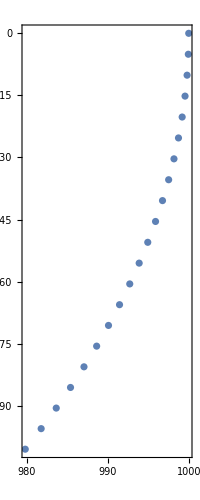

```mathematica
ListPlot[Flatten/@Avals,AspectRatio->Automatic]
```

```mathematica
PillBoxΩ[cavLx,cavLy,cavLz/10][1,1,0]
```

0.5029

```mathematica
{Zfin,Afin}=CrossCavList[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

Set::shape: Lists {trZ$1529,trA$1529} and {{{{5.,2.5,5.,2.5},{0.,0.,0.,0.},{4.,4.,2.,2.},{0.,0.,0.,0.},{0,0,0,0},{2.89114×10^-16,2.84422×10^-16,2.84422×10^-16,2.81103×10^-16}},{{1000},{0}}},«19»,{{{5.,2.5707,5.,2.55053},{5.52479×10^-34,6.36659×10^-18,3.91466×10^-34,4.51092×10^-18},{4.,4.,2.08825,2.06305},«1»,{3.98914,3.98591,3.98554,3.98386},{2.89114×10^-16,2.84422×10^-16,2.84422×10^-16,2.81103×10^-16}},{{-«18»},{-«18»}}}} are not the same shape.

{{{5.,0.,4.,0.,0,2.73092×10^-16},{2.5,0.,4.,0.,0,2.73092×10^-16},{5.,0.,2.,0.,0,2.73092×10^-16},{2.5,0.,2.,0.,0,2.73092×10^-16}},{{1000,0}}}

#### Test 2x (energy conservation—one mode, one particle)

What about the energy gain? To check this, we turn the field rotation back on; but we limit that field rotation by using a very short cavity:

```mathematica
RotateEM[Lx_,Ly_,Lz_][mode_List,ds_][Q_List,P_List]:=Module[
{M,Ω,MΩ,cosΩds,sinΩds,Qf,Pf},
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
Ω=PillBoxΩ[Lx,Ly,Lz][Sequence@@Rest@#]&/@mode;
MΩ=M Ω;
cosΩds=Cos[Ω ds];
sinΩds=Sin[Ω ds];
Qf=Q cosΩds+P/MΩ sinΩds;
Pf=-Q MΩ sinΩds+P cosΩds;
{Qf,Pf}
]
```

```mathematica
HamPF[Lx_,Ly_,Lz_][mode_List][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{Ax,Ay,As,inCav,M,K,ergP,ergF},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
ergP=Plus@@√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
K=EigenmodeK[Lx,Ly,Lz][Sequence@@#]&/@mode;
ergF=1/2((P/M).P+(K Q).Q);
{ergP,ergF,ergP+ergF}
]
```

```mathematica
HamF[Lx_,Ly_,Lz_][mode_List][Q_,P_]:=Module[
{M,K},
M=EigenmodeM[Lx,Ly,Lz][Sequence@@#]&/@mode;
K=EigenmodeK[Lx,Ly,Lz][Sequence@@#]&/@mode;
1/2((P/M).P+(K Q).Q)
]
```

```mathematica
Transpose@oneAinit
```

{{1000},{0}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

0.000026853

{{999.987},{-5.39764×10^-10}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.949},{-1.07951×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.885},{-1.61924×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.796},{-2.15892×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.681},{-2.69854×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.54},{-3.2381×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.374},{-3.77757×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

{{999.183},{-4.31695×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

0.000026853

{{998.966},{-4.85622×10^-9}}

```mathematica
HamF[cavLx,cavLy,cavLz][oneMode][Sequence@@%]
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%%]
```

0.000026853

0.000026853

{{998.723},{-5.39536×10^-9}}

```mathematica
StepHamPF[Lx_,Ly_,Lz_][mode_List,pfCoupling_,ds_][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,Ax,Ay,As,γmc,Z=Zi,A=Ai},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
γmc=√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
Print@NumberForm[#,16]&@(γmc/MeC);
Print@NumberForm[#,16]&@A;
Print@NumberForm[#,16]&@HamPF[cavLx,cavLy,cavLz][oneMode][Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][3,mode,pfCoupling,ds][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}
]
```

```mathematica
{cavLx,cavLy,cavLz/20}
{oneMode,(cavLz/20)/beamβ 1/20,20}
{oneZinit,oneAinit}
```

{10.,8.,0.2}

{{{TM,1,1,0}},0.0100504,20}

{{{5.,0,4.,0,0,2.71724×10^-16}},{{1000,0}}}

```mathematica
CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,4][oneZinit,oneAinit,ParticleFieldCoupling->False]
```

{10.}

{{1000},{0}}

{2.730924488317191×10^-16,0.00002685301434375592,0.00002685301434402901}

{10.00000745617001}

{{999.987226864931},{-2.698817996069635×10^-11}}

{2.730926524540918×10^-16,0.00002685233006875355,0.00002685233006902664}

{10.0000298244899}

{{999.948907786029},{-5.397567047405686×10^-11}}

{2.730932633160173×10^-16,0.0000268502773136687,0.00002685027731394179}

{10.00006710438925}

{{999.885043742204},{-8.09617821103585×10^-11}}

{2.730942814019179×10^-16,0.00002684685628826096,0.00002684685628853405}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.69882×10^-11}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.39757×10^-11}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-8.09618×10^-11}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-1.07946×10^-10}}}}

```mathematica
CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,4][oneZinit,oneAinit,ParticleFieldCoupling->True]
```

{10.}

{{1000},{0}}

{2.730924488317191×10^-16,0.00002685301434375592,0.00002685301434402901}

{10.00000745617001}

{{999.987226864931},{-2.698817996053613×10^-11}}

{2.730926524540918×10^-16,0.00002685233006875355,0.00002685233006902664}

{10.0000298244899}

{{999.948907786029},{-5.397567047373643×10^-11}}

{2.730932633160173×10^-16,0.00002685027731366871,0.00002685027731394181}

{10.00006710438925}

{{999.885043742205},{-8.09617821098779×10^-11}}

{2.730942814019179×10^-16,0.000026846856288261,0.0000268468562885341}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.69882×10^-11}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.39757×10^-11}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-8.09618×10^-11}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-1.07946×10^-10}}}}

```mathematica
Transpose@oneAinit
```

{{1000},{0}}

```mathematica
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%]//NumberForm[#,16]&
```

{{999.987226864931},{-5.397635992139268×10^-10}}

```mathematica
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%]//NumberForm[#,16]&
```

{{999.948907786029},{-1.079513409481137×10^-9}}

```mathematica
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%]//NumberForm[#,16]&
```

{{999.885043742204},{-1.619235642207171×10^-9}}

```mathematica
RotateEM[cavLx,cavLy,cavLz][oneMode,(cavLz/20)/beamβ 1/20][Sequence@@%]//NumberForm[#,16]&
```

{{999.795636364945},{-2.158916509502071×10^-9}}

```mathematica
CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit,ParticleFieldCoupling->False]
```

{10.}

{2.730924488317191×10^-16,0.00002685301434375592,0.00002685301434402901}

{10.00000745617001}

{2.730926524540918×10^-16,0.00002685233006875355,0.00002685233006902664}

{10.0000298244899}

{2.730932633160173×10^-16,0.0000268502773136687,0.00002685027731394179}

{10.00006710438925}

{2.730942814019179×10^-16,0.00002684685628826096,0.00002684685628853405}

{10.00011929491739}

{2.730957066858315×10^-16,0.00002684206734210587,0.00002684206734237897}

{10.0001863947434}

{2.730975391314116×10^-16,0.00002683591096455916,0.00002683591096483227}

{10.00026840215616}

{2.730997786919289×10^-16,0.00002682838778470674,0.00002682838778497984}

{10.0003653150644}

{2.731024253102721×10^-16,0.00002681949857130043,0.00002681949857157353}

{10.00047713099671}

{2.731054789189495×10^-16,0.00002680924423267941,0.00002680924423295252}

{10.00060384710168}

{2.731089394400908×10^-16,0.00002679762581667743,0.00002679762581695054}

{10.00074546014789}

{2.731128067854485×10^-16,0.00002678464451051567,0.00002678464451078878}

{10.00090196652406}

{2.731170808564011×10^-16,0.00002677030164068146,0.00002677030164095458}

{10.00107336223909}

{2.731217615439546×10^-16,0.00002675459867279279,0.00002675459867306591}

{10.00125964292218}

{2.731268487287461×10^-16,0.00002673753721144841,0.00002673753721172154}

{10.00146080382295}

{2.731323422810463×10^-16,0.00002671911900006401,0.00002671911900033714}

{10.00167683981156}

{2.731382420607628×10^-16,0.00002669934592069398,0.0000266993459209671}

{10.00190774537882}

{2.73144547917444×10^-16,0.0000266782199938391,0.00002667821999411224}

{10.00215351463635}

{2.731512596902826×10^-16,0.00002665574337824015,0.0000266557433785133}

{10.00241414131671}

{2.731583772081198×10^-16,0.00002663191837065723,0.00002663191837093039}

{10.00268961877359}

{2.731659002894494×10^-16,0.00002660674740563511,0.00002660674740590827}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.69882×10^-11}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.39757×10^-11}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-8.09618×10^-11}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-1.07946×10^-10}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-1.34927×10^-10}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-1.61905×10^-10}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-1.88879×10^-10}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-2.15848×10^-10}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-2.42811×10^-10}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-2.69768×10^-10}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-2.96718×10^-10}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-3.23661×10^-10}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-3.50595×10^-10}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-3.77521×10^-10}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-4.04437×10^-10}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-4.31342×10^-10}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-4.58237×10^-10}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-4.85119×10^-10}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-5.1199×10^-10}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-5.38847×10^-10}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit]
```

{10.}

{10.}

{10.}

{10.0001}

{10.0001}

{10.0002}

{10.0003}

{10.0004}

{10.0005}

{10.0006}

{10.0007}

{10.0009}

{10.0011}

{10.0013}

{10.0015}

{10.0017}

{10.0019}

{10.0022}

{10.0024}

{10.0027}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-12.7078}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-15.2486}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-17.7891}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-20.3291}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-22.8686}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-25.4075}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-27.9457}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-30.4832}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-33.02}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-35.5559}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-38.0909}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-40.6249}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-43.1579}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-45.6898}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-48.2205}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-50.75}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,20][oneZinit,oneAinit]
```

{10.}

{10.}

{10.}

{10.0001}

{10.0001}

{10.0002}

{10.0003}

{10.0004}

{10.0005}

{10.0006}

{10.0007}

{10.0009}

{10.0011}

{10.0013}

{10.0015}

{10.0017}

{10.0019}

{10.0022}

{10.0024}

{10.0027}

{{{{5.,0.,4.,0.,0,2.71724×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16}},{{999.681,-12.7078}}},{{{5.,1.84896×10^-35,4.,2.3112×10^-35,0.0600001,2.71731×10^-16}},{{999.54,-15.2486}}},{{{5.,2.157×10^-35,4.,2.69625×10^-35,0.0700002,2.71734×10^-16}},{{999.374,-17.7891}}},{{{5.,2.46499×10^-35,4.,3.08123×10^-35,0.0800002,2.71737×10^-16}},{{999.183,-20.3291}}},{{{5.,2.77291×10^-35,4.,3.46614×10^-35,0.0900003,2.7174×10^-16}},{{998.966,-22.8686}}},{{{5.,3.08076×10^-35,4.,3.85095×10^-35,0.1,2.71744×10^-16}},{{998.723,-25.4075}}},{{{5.,3.38854×10^-35,4.,4.23567×10^-35,0.11,2.71748×10^-16}},{{998.455,-27.9457}}},{{{5.,3.69623×10^-35,4.,4.62028×10^-35,0.120001,2.71753×10^-16}},{{998.161,-30.4832}}},{{{5.,4.00382×10^-35,4.,5.00478×10^-35,0.130001,2.71758×10^-16}},{{997.842,-33.02}}},{{{5.,4.31131×10^-35,4.,5.38914×10^-35,0.140001,2.71764×10^-16}},{{997.498,-35.5559}}},{{{5.,4.6187×10^-35,4.,5.77337×10^-35,0.150001,2.7177×10^-16}},{{997.127,-38.0909}}},{{{5.,4.92596×10^-35,4.,6.15745×10^-35,0.160001,2.71776×10^-16}},{{996.732,-40.6249}}},{{{5.,5.2331×10^-35,4.,6.54137×10^-35,0.170001,2.71783×10^-16}},{{996.311,-43.1579}}},{{{5.,5.5401×10^-35,4.,6.92513×10^-35,0.180001,2.7179×10^-16}},{{995.864,-45.6898}}},{{{5.,5.84697×10^-35,4.,7.30871×10^-35,0.190001,2.71797×10^-16}},{{995.392,-48.2205}}},{{{5.,1.94289×10^-37,4.,2.42861×10^-37,0.200002,2.71801×10^-16}},{{994.895,-50.75}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][twoModes,(cavLz/20)/beamβ 1/20,5][fourZinit,twoAinit]
```

{10.,10.,10.,10.}

{10.,10.,10.,10.}

{10.,10.,10.,10.}

{10.0001,10.,10.,10.}

{10.0001,10.0001,10.0001,10.0001}

{{{{5.,0.,4.,0.,0,2.71724×10^-16},{2.5,0.,4.,0.,0,2.71724×10^-16},{5.,0.,2.,0.,0,2.71724×10^-16},{2.5,0.,2.,0.,0,2.71724×10^-16}},{{1000,0},{0,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.71724×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.71724×10^-16},{5.,2.17934×10^-36,2.,4.44891×10^-20,0.01,2.71724×10^-16},{2.5,2.51669×10^-20,2.,3.14586×10^-20,0.01,2.71724×10^-16}},{{999.987,-2.54182},{1.37443×10^-24,2.73506×10^-22}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.71724×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.71724×10^-16},{5.,4.35862×10^-36,2.,8.89771×10^-20,0.02,2.71724×10^-16},{2.5,5.03331×10^-20,2.,6.29163×10^-20,0.02,2.71724×10^-16}},{{999.949,-5.08357},{5.49762×10^-24,5.46993×10^-22}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.71725×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.71725×10^-16},{5.,6.5378×10^-36,2.00001,1.33463×10^-19,0.03,2.71725×10^-16},{2.5,7.5498×10^-20,2.00001,9.43725×10^-20,0.03,2.71724×10^-16}},{{999.885,-7.62519},{1.23693×10^-23,8.2044×10^-22}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.71727×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.71726×10^-16},{5.,8.71682×10^-36,2.00001,1.77945×10^-19,0.04,2.71726×10^-16},{2.50001,1.00661×10^-19,2.00001,1.25826×10^-19,0.04,2.71725×10^-16}},{{999.796,-10.1666},{2.19889×10^-23,1.09383×10^-21}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.71729×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.71727×10^-16},{5.,1.08956×10^-35,2.00002,2.22423×10^-19,0.0500001,2.71727×10^-16},{2.50001,1.25822×10^-19,2.00001,1.57277×10^-19,0.05,2.71726×10^-16}},{{999.681,-12.7078},{3.43558×10^-23,1.36714×10^-21}}}}

```mathematica
{PCanonToPMech[cavLx,cavLy,cavLz][oneMode,First@#⟦2⟧][#⟦1⟧],#⟦2⟧}&/@ccl
```

{{{{5.,2.5},{0.,0.},{4.,4.},{0.,0.},{0,0},{2.71724×10^-16,2.71724×10^-16}},{{1000},{0}}},{{{5.,2.5},{3.08205×10^-36,3.55913×10^-20},{4.,4.},{3.85256×10^-36,2.72417×10^-36},{0.01,0.01},{2.71724×10^-16,2.71724×10^-16}},{{999.987},{-2.54182}}},{{{5.,2.5},{6.16403×10^-36,7.11817×10^-20},{4.,4.},{7.70503×10^-36,5.44828×10^-36},{0.02,0.02},{2.71724×10^-16,2.71724×10^-16}},{{999.949},{-5.08357}}},{{{5.,2.50001},{9.24584×10^-36,1.0677×10^-19},{4.,4.},{1.15573×10^-35,8.17225×10^-36},{0.03,0.03},{2.71725×10^-16,2.71725×10^-16}},{{999.885},{-7.62519}}},{{{5.,2.50001},{1.23274×10^-35,1.42356×10^-19},{4.,4.},{1.54093×10^-35,1.0896×10^-35},{0.0400001,0.04},{2.71727×10^-16,2.71726×10^-16}},{{999.796},{-10.1666}}},{{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.71729×10^-16,2.71727×10^-16}},{{999.681},{-12.7078}}}}

```mathematica
ccl=CrossCavityList[cavLx,cavLy,cavLz/20][oneMode,(cavLz/20)/beamβ 1/20,5][twoZinit,oneAinit]
```

{10.,10.}

{10.,10.}

{10.,10.}

{10.0001,10.}

{10.0001,10.0001}

{{{{5.,2.5},{0.,0.},{4.,4.},{0.,0.},{0,0},{2.87745×10^-16,2.83053×10^-16}},{{1000},{0}}},{{{5.,2.5},{3.08205×10^-36,3.55913×10^-20},{4.,4.},{3.85256×10^-36,2.72417×10^-36},{0.01,0.01},{2.87745×10^-16,2.83053×10^-16}},{{999.987},{-2.54182}}},{{{5.,2.5},{6.16403×10^-36,7.11817×10^-20},{4.,4.},{7.70503×10^-36,5.44828×10^-36},{0.02,0.02},{2.87745×10^-16,2.83053×10^-16}},{{999.949},{-5.08357}}},{{{5.,2.50001},{9.24584×10^-36,1.0677×10^-19},{4.,4.},{1.15573×10^-35,8.17225×10^-36},{0.03,0.03},{2.87745×10^-16,2.83053×10^-16}},{{999.885},{-7.62519}}},{{{5.,2.50001},{1.23274×10^-35,1.42356×10^-19},{4.,4.},{1.54093×10^-35,1.0896×10^-35},{0.0400001,0.04},{2.87745×10^-16,2.83053×10^-16}},{{999.796},{-10.1666}}},{{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.87745×10^-16,2.83053×10^-16}},{{999.681},{-12.7078}}}}

```mathematica
Dimensions@ccl
Dimensions/@ccl
```

{6,2}

{{2},{2},{2},{2},{2},{2}}

```mathematica
Transpose/@#&/@ccl
```

{{{{5.,0.,4.,0.,0,2.87745×10^-16},{2.5,0.,4.,0.,0,2.83053×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.87745×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.83053×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.87745×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.83053×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.87745×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.83053×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.87745×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.83053×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}}

```mathematica
Map[Transpose,ccl,{2}]
```

{{{{5.,0.,4.,0.,0,2.87745×10^-16},{2.5,0.,4.,0.,0,2.83053×10^-16}},{{1000,0}}},{{{5.,3.08205×10^-36,4.,3.85256×10^-36,0.01,2.87745×10^-16},{2.5,3.55913×10^-20,4.,2.72417×10^-36,0.01,2.83053×10^-16}},{{999.987,-2.54182}}},{{{5.,6.16403×10^-36,4.,7.70503×10^-36,0.02,2.87745×10^-16},{2.5,7.11817×10^-20,4.,5.44828×10^-36,0.02,2.83053×10^-16}},{{999.949,-5.08357}}},{{{5.,9.24584×10^-36,4.,1.15573×10^-35,0.03,2.87745×10^-16},{2.50001,1.0677×10^-19,4.,8.17225×10^-36,0.03,2.83053×10^-16}},{{999.885,-7.62519}}},{{{5.,1.23274×10^-35,4.,1.54093×10^-35,0.0400001,2.87745×10^-16},{2.50001,1.42356×10^-19,4.,1.0896×10^-35,0.04,2.83053×10^-16}},{{999.796,-10.1666}}},{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}}

```mathematica
ccl⟦-1,1⟧
```

{{5.,2.50002},{1.54087×10^-35,1.77938×10^-19},{4.,4.},{1.92609×10^-35,1.36195×10^-35},{0.0500001,0.0500001},{2.87745×10^-16,2.83053×10^-16}}

```mathematica
Transpose@ccl⟦-1,1⟧
```

{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}}

```mathematica
Transpose/@ccl⟦-1⟧
```

{{{5.,1.54087×10^-35,4.,1.92609×10^-35,0.0500001,2.87745×10^-16},{2.50002,1.77938×10^-19,4.,1.36195×10^-35,0.0500001,2.83053×10^-16}},{{999.681,-12.7078}}}

```mathematica
MapThread[f,{{a,b,c},{1,2,3}}]
```

{f[a,1],f[b,2],f[c,3]}

```mathematica
cavLz/20
```

0.2

```mathematica
1/MeC √(MeC^2+(px)^2+(py)^2+(ps)^2)/.Thread[{px,py,ps}->{oneZinit⟦;;,2⟧,oneZinit⟦;;,4⟧,oneZinit⟦;;,6⟧}]
```

{10.0499}

```mathematica
% SRBeta[10]
```

{9.9995}

```mathematica
{Zfin,Afin}=CrossCavity[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{{{5.,5.52479×10^-34,4.,6.90598×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.88901×10^-34,3.98591,2.89361×10^-16},{5.,3.91466×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827}}}

```mathematica
{Zfin,Afin}=CrossCav[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{{{5.,5.52479×10^-34,4.,6.90598×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.88901×10^-34,3.98591,2.89361×10^-16},{5.,3.91466×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827}}}

```mathematica
Ainit
Afin
```

{{1000,0}}

{{-426.667,-454.827}}

```mathematica
CrossCavList[cavLx,cavLy,cavLz/10][modes,20][Zinit,Ainit]
```

Transpose::nmtx: The first two levels of {5.,2.5,5.,2.5} cannot be transposed.

Transpose::nmtx: The first two levels of {0.,0.,0.,0.} cannot be transposed.

Transpose::nmtx: The first two levels of {4.,4.,2.,2.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{{Transpose[{5.,2.5,5.,2.5}],Transpose[{0.,0.,0.,0.}],Transpose[{4.,4.,2.,2.}],Transpose[{0.,0.,0.,0.}],Transpose[{0,0,0,0}],Transpose[{2.73092×10^-16,2.73092×10^-16,2.73092×10^-16,2.73092×10^-16}]},{Transpose[{5.,2.5,5.,2.5}],Transpose[{6.13346×10^-36,7.08287×10^-20,4.33701×10^-36,5.00835×10^-20}],Transpose[{4.,4.,2.,2.}],Transpose[{7.66682×10^-36,5.42126×10^-36,8.85359×10^-20,6.26043×10^-20}],Transpose[{0.0199008,0.0199008,0.0199008,0.0199008}],Transpose[{2.73093×10^-16,2.73093×10^-16,2.73093×10^-16,2.73093×10^-16}]},{Transpose[{5.,2.50001,5.,2.50001}],Transpose[{1.22663×10^-35,1.4165×10^-19,8.6736×10^-36,1.00162×10^-19}],Transpose[{4.,4.,2.00001,2.00001}],Transpose[{1.53329×10^-35,1.0842×10^-35,1.77063×10^-19,1.25202×10^-19}],Transpose[{0.0398016,0.0398015,0.0398015,0.0398015}],Transpose[{2.73096×10^-16,2.73095×10^-16,2.73095×10^-16,2.73094×10^-16}]},{Transpose[{5.,2.50002,5.,2.50002}],Transpose[{1.83979×10^-35,2.12457×10^-19,1.30093×10^-35,1.5023×10^-19}],Transpose[{4.,4.,2.00003,2.00002}],Transpose[{2.29974×10^-35,1.62617×10^-35,2.65571×10^-19,1.87788×10^-19}],Transpose[{0.0597025,0.0597024,0.0597024,0.0597023}],Transpose[{2.731×10^-16,2.73098×10^-16,2.73097×10^-16,2.73096×10^-16}]},{Transpose[{5.,2.50004,5.,2.50003}],Transpose[{2.45277×10^-35,2.83243×10^-19,1.73438×10^-35,2.00284×10^-19}],Transpose[{4.,4.,2.00005,2.00004}],Transpose[{3.06597×10^-35,2.16797×10^-35,3.54053×10^-19,2.50354×10^-19}],Transpose[{0.0796034,0.0796033,0.0796033,0.0796032}],Transpose[{2.73105×10^-16,2.73101×10^-16,2.73101×10^-16,2.73099×10^-16}]},{Transpose[{5.,2.50006,5.,2.50005}],Transpose[{3.06551×10^-35,3.53999×10^-19,2.16766×10^-35,2.50317×10^-19}],Transpose[{4.,4.,2.00008,2.00006}],Transpose[{3.83188×10^-35,2.70956×10^-35,4.42498×10^-19,3.12895×10^-19}],Transpose[{0.0995044,0.0995042,0.0995042,0.099504}],Transpose[{2.73113×10^-16,2.73107×10^-16,2.73106×10^-16,2.73102×10^-16}]},{Transpose[{5.,2.50009,5.,2.50007}],Transpose[{3.67793×10^-35,4.2472×10^-19,2.60072×10^-35,3.00326×10^-19}],Transpose[{4.,4.,2.00012,2.00008}],Transpose[{4.59741×10^-35,3.25088×10^-35,5.30897×10^-19,3.75404×10^-19}],Transpose[{0.119405,0.119405,0.119405,0.119405}],Transpose[{2.73122×10^-16,2.73113×10^-16,2.73113×10^-16,2.73107×10^-16}]},{Transpose[{5.,2.50013,5.,2.50009}],Transpose[{4.28999×10^-35,4.95396×10^-19,3.03353×10^-35,3.50304×10^-19}],Transpose[{4.,4.,2.00016,2.00011}],Transpose[{5.36248×10^-35,3.79188×10^-35,6.19241×10^-19,4.37875×10^-19}],Transpose[{0.139307,0.139306,0.139306,0.139306}],Transpose[{2.73132×10^-16,2.7312×10^-16,2.7312×10^-16,2.73112×10^-16}]},{Transpose[{5.,2.50017,5.,2.50012}],Transpose[{4.90161×10^-35,5.66022×10^-19,3.46604×10^-35,4.00247×10^-19}],Transpose[{4.,4.,2.00021,2.00015}],Transpose[{6.12701×10^-35,4.33251×10^-35,7.07521×10^-19,5.00302×10^-19}],Transpose[{0.159208,0.159207,0.159207,0.159207}],Transpose[{2.73144×10^-16,2.73129×10^-16,2.73128×10^-16,2.73118×10^-16}]},{Transpose[{5.,2.50021,5.,2.50015}],Transpose[{5.51274×10^-35,6.3659×10^-19,3.8982×10^-35,4.50149×10^-19}],Transpose[{4.,4.,2.00026,2.00018}],Transpose[{6.89092×10^-35,4.8727×10^-35,7.95728×10^-19,5.62677×10^-19}],Transpose[{0.179109,0.179108,0.179108,0.179108}],Transpose[{2.73158×10^-16,2.73138×10^-16,2.73138×10^-16,2.73124×10^-16}]},{Transpose[{5.,2.50026,5.,2.50018}],Transpose[{6.12331×10^-35,7.07093×10^-19,4.32999×10^-35,5.00007×10^-19}],Transpose[{4.,4.,2.00032,2.00023}],Transpose[{7.65414×10^-35,5.41241×10^-35,8.83852×10^-19,6.24996×10^-19}],Transpose[{0.19901,0.199009,0.199009,0.199009}],Transpose[{2.73173×10^-16,2.73149×10^-16,2.73148×10^-16,2.73132×10^-16}]},{Transpose[{5.,2.50031,5.,2.50022}],Transpose[{6.73327×10^-35,7.77523×10^-19,4.76135×10^-35,5.49814×10^-19}],Transpose[{4.,4.,2.00039,2.00028}],Transpose[{8.41658×10^-35,5.95158×10^-35,9.71885×10^-19,6.8725×10^-19}],Transpose[{0.218912,0.21891,0.21891,0.21891}],Transpose[{2.7319×10^-16,2.73161×10^-16,2.7316×10^-16,2.7314×10^-16}]},{Transpose[{5.,2.50037,5.,2.50026}],Transpose[{7.34254×10^-35,8.47873×10^-19,5.19223×10^-35,5.99567×10^-19}],Transpose[{4.,4.,2.00046,2.00033}],Transpose[{9.17818×10^-35,6.49016×10^-35,1.05982×10^-18,7.49435×10^-19}],Transpose[{0.238813,0.238812,0.238811,0.238811}],Transpose[{2.73209×10^-16,2.73174×10^-16,2.73173×10^-16,2.73149×10^-16}]},{Transpose[{5.,2.50044,5.,2.50031}],Transpose[{7.95108×10^-35,9.18136×10^-19,5.62261×10^-35,6.49259×10^-19}],Transpose[{4.,4.,2.00054,2.00038}],Transpose[{9.93885×10^-35,7.02809×10^-35,1.14764×10^-18,8.11544×10^-19}],Transpose[{0.258715,0.258713,0.258713,0.258712}],Transpose[{2.73229×10^-16,2.73188×10^-16,2.73187×10^-16,2.73159×10^-16}]},{Transpose[{5.,2.5005,5.,2.50036}],Transpose[{8.55881×10^-35,9.88305×10^-19,6.05243×10^-35,6.98885×10^-19}],Transpose[{4.,4.,2.00063,2.00045}],Transpose[{1.06985×10^-34,7.56533×10^-35,1.23534×10^-18,8.7357×10^-19}],Transpose[{0.278616,0.278614,0.278614,0.278613}],Transpose[{2.73251×10^-16,2.73203×10^-16,2.73202×10^-16,2.73169×10^-16}]},{Transpose[{5.,2.50058,5.,2.50041}],Transpose[{9.16568×10^-35,1.05837×10^-18,6.48166×10^-35,7.48442×10^-19}],Transpose[{4.,4.,2.00072,2.00051}],Transpose[{1.14571×10^-34,8.10181×10^-35,1.32292×10^-18,9.35507×10^-19}],Transpose[{0.298518,0.298515,0.298515,0.298514}],Transpose[{2.73274×10^-16,2.73219×10^-16,2.73218×10^-16,2.73181×10^-16}]},{Transpose[{5.,2.50066,5.,2.50047}],Transpose[{9.77163×10^-35,1.12833×10^-18,6.91024×10^-35,7.97923×10^-19}],Transpose[{4.,4.,2.00082,2.00058}],Transpose[{1.22145×10^-34,8.63749×10^-35,1.41036×10^-18,9.97349×10^-19}],Transpose[{0.31842,0.318417,0.318416,0.318415}],Transpose[{2.73299×10^-16,2.73237×10^-16,2.73235×10^-16,2.73193×10^-16}]},{Transpose[{5.,2.50074,5.,2.50053}],Transpose[{1.03766×10^-34,1.19818×10^-18,7.33815×10^-35,8.47324×10^-19}],Transpose[{4.,4.,2.00093,2.00066}],Transpose[{1.29707×10^-34,9.1723×10^-35,1.49765×10^-18,1.05909×10^-18}],Transpose[{0.338322,0.338318,0.338317,0.338316}],Transpose[{2.73326×10^-16,2.73255×10^-16,2.73254×10^-16,2.73206×10^-16}]},{Transpose[{5.,2.50083,5.,2.50059}],Transpose[{1.09805×10^-34,1.2679×10^-18,7.76533×10^-35,8.9664×10^-19}],Transpose[{4.,4.,2.00104,2.00074}],Transpose[{1.37256×10^-34,9.70621×10^-35,1.58479×10^-18,1.12072×10^-18}],Transpose[{0.358224,0.358219,0.358219,0.358217}],Transpose[{2.73354×10^-16,2.73275×10^-16,2.73273×10^-16,2.7322×10^-16}]},{Transpose[{5.,2.50093,5.,2.50066}],Transpose[{1.15833×10^-34,1.33749×10^-18,8.19175×10^-35,9.45866×10^-19}],Transpose[{4.,4.,2.00116,2.00082}],Transpose[{1.44791×10^-34,1.02391×10^-34,1.67176×10^-18,1.18224×10^-18}],Transpose[{0.378126,0.378121,0.37812,0.378118}],Transpose[{2.73384×10^-16,2.73295×10^-16,2.73294×10^-16,2.73234×10^-16}]},{Transpose[{5.,2.50103,5.,2.50073}],Transpose[{1.21849×10^-34,1.40694×10^-18,8.61735×10^-35,9.94996×10^-19}],Transpose[{4.,4.,2.00129,2.00091}],Transpose[{1.52312×10^-34,1.07711×10^-34,1.75856×10^-18,1.24364×10^-18}],Transpose[{0.398028,0.398022,0.398021,0.398019}],Transpose[{2.73416×10^-16,2.73317×10^-16,2.73315×10^-16,2.73249×10^-16}]}}

```mathematica
Avals=Last/@%
```

{{{1000},{0}},{{999.949},{-5.05809}},{{999.798},{-10.1157}},{{999.545},{-15.1722}},{{999.191},{-20.2272}},{{998.736},{-25.2802}},{{998.18},{-30.3306}},{{997.523},{-35.378}},{{996.765},{-40.4217}},{{995.906},{-45.4614}},{{994.946},{-50.4965}},{{993.886},{-55.5265}},{{992.725},{-60.5508}},{{991.464},{-65.569}},{{990.102},{-70.5806}},{{988.641},{-75.5851}},{{987.079},{-80.5819}},{{985.417},{-85.5705}},{{983.656},{-90.5505}},{{981.796},{-95.5214}},{{979.835},{-100.483}}}

```mathematica
ListPlot[Flatten/@Avals,AspectRatio->Automatic]
```

-Graphics-

```mathematica
PillBoxΩ[cavLx,cavLy,cavLz/10][1,1,0]
```

0.5029

```mathematica
{Zfin,Afin}=CrossCavList[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

Set::shape: Lists {trZ$1529,trA$1529} and {{{{5.,2.5,5.,2.5},{0.,0.,0.,0.},{4.,4.,2.,2.},{0.,0.,0.,0.},{0,0,0,0},{2.89114×10^-16,2.84422×10^-16,2.84422×10^-16,2.81103×10^-16}},{{1000},{0}}},«19»,{{{5.,2.5707,5.,2.55053},{5.52479×10^-34,6.36659×10^-18,3.91466×10^-34,4.51092×10^-18},{4.,4.,2.08825,2.06305},«1»,{3.98914,3.98591,3.98554,3.98386},{2.89114×10^-16,2.84422×10^-16,2.84422×10^-16,2.81103×10^-16}},{{-«18»},{-«18»}}}} are not the same shape.

{{{5.,0.,4.,0.,0,2.73092×10^-16},{2.5,0.,4.,0.,0,2.73092×10^-16},{5.,0.,2.,0.,0,2.73092×10^-16},{2.5,0.,2.,0.,0,2.73092×10^-16}},{{1000,0}}}

#### Test 3

```mathematica
cavLx=10.0;
cavLy=8.0;
cavLz=4.0;
```

```mathematica
pbEx=PillBoxEx[cavLx,cavLy,cavLz];
pbEy=PillBoxEy[cavLx,cavLy,cavLz];
pbEz=PillBoxEz[cavLx,cavLy,cavLz];
```

```mathematica
Ps=10.MeC;
Zinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

```mathematica
modes={
{"TM",1,1,0},
{"TM",1,2,0},
{"TM",2,1,0}
};
```

```mathematica
Ainit={
{10^3,0},
{0,0},
{0,0}
};
```

```mathematica
EOverC
```

1.60218×10^-20

```mathematica
EOverC/=10^6
```

```mathematica
{Zfin,Afin}=CrossCav[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{10.0499,10.0499,10.0499,10.0499}

{10.0499,10.0499,10.0499,10.0499}

3:  {0.,0.,0.}

3:  {0.579983,0.339743,0.339743}

{10.0528,10.052,10.052,10.0514}

3:  {0.580071,0.339759,0.339768}

3:  {1.16027,0.679577,0.679596}

{10.0616,10.0582,10.0582,10.0558}

3:  {1.16062,0.679641,0.679696}

3:  {1.74112,1.01955,1.01963}

{10.0763,10.0685,10.0685,10.0631}

3:  {1.7419,1.01969,1.01985}

3:  {2.32279,1.3597,1.35992}

{10.0965,10.0829,10.0829,10.0732}

3:  {2.32415,1.35994,1.36031}

3:  {2.9055,1.70006,1.70053}

{10.1222,10.101,10.1011,10.0861}

3:  {2.90759,1.70042,1.70112}

3:  {3.48947,2.04066,2.04151}

{10.153,10.1229,10.1229,10.1016}

3:  {3.49242,2.04117,2.04234}

3:  {4.0749,2.38153,2.38291}

{10.1887,10.1482,10.1483,10.1195}

3:  {4.07881,2.38218,2.384}

3:  {4.66195,2.72268,2.72478}

{10.2289,10.1768,10.1769,10.1398}

3:  {4.6669,2.72348,2.72615}

3:  {5.25076,3.06412,3.06714}

{10.2732,10.2082,10.2085,10.1621}

3:  {5.25682,3.06506,3.06881}

3:  {5.84143,3.40583,3.41002}

{10.3211,10.2424,10.2427,10.1864}

3:  {5.84863,3.40691,3.41198}

3:  {6.43404,3.74782,3.75342}

{10.3722,10.2788,10.2793,10.2123}

3:  {6.44238,3.74901,3.75568}

3:  {7.02862,4.09006,4.09735}

{10.426,10.3171,10.3179,10.2396}

3:  {7.03809,4.09134,4.09989}

3:  {7.62518,4.43252,4.4418}

{10.4818,10.357,10.358,10.2681}

3:  {7.63572,4.43388,4.44459}

3:  {8.22367,4.77518,4.78674}

{10.5392,10.3981,10.3993,10.2974}

3:  {8.23522,4.77658,4.78976}

3:  {8.82403,5.118,5.13214}

{10.5976,10.4399,10.4415,10.3273}

3:  {8.83648,5.11942,5.13537}

3:  {9.42615,5.46095,5.47798}

{10.6563,10.482,10.4839,10.3575}

3:  {9.43938,5.46236,5.48136}

3:  {10.0299,5.80399,5.8242}

{10.7148,10.5241,10.5264,10.3876}

3:  {10.0438,5.80535,5.8277}

3:  {10.6351,6.14708,6.17075}

{10.7724,10.5656,10.5683,10.4174}

3:  {10.6494,6.14838,6.17433}

3:  {11.2416,6.49018,6.51758}

{10.8287,10.6062,10.6093,10.4466}

3:  {11.2562,6.4914,6.52118}

3:  {11.8491,6.83326,6.86462}

{10.883,10.6454,10.6489,10.4748}

{{{5.,5.52477×10^-34,4.,6.90596×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.889×10^-34,3.98591,2.89361×10^-16},{5.,3.91465×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827},{7.53171×10^-20,-7.58351×10^-21},{9.89025×10^-20,6.79486×10^-21}}}

#### Test 2

```mathematica
cavLx=10.0;
cavLy=8.0;
cavLz=4.0;
```

```mathematica
pbEx=PillBoxEx[cavLx,cavLy,cavLz];
pbEy=PillBoxEy[cavLx,cavLy,cavLz];
pbEz=PillBoxEz[cavLx,cavLy,cavLz];
```

```mathematica
Ps=10.MeC;
Zinit={
{cavLx/2,0,cavLy/2,0,0,Ps},
{cavLx/4,0,cavLy/2,0,0,Ps},
{cavLx/2,0,cavLy/4,0,0,Ps},
{cavLx/4,0,cavLy/4,0,0,Ps}
};
```

```mathematica
modes={
{"TM",1,1,0},
{"TM",1,2,0},
{"TM",2,1,0}
};
```

```mathematica
Ainit={
{10^3,0},
{0,0},
{0,0}
};
```

```mathematica
EOverC
```

1.60218×10^-20

```mathematica
EOverC/=10^6
```

```mathematica
{Zfin,Afin}=CrossCav[cavLx,cavLy,cavLz][modes,20][Zinit,Ainit]
```

{10.0499,10.0499,10.0499,10.0499}

{10.0499,10.0499,10.0499,10.0499}

3:  {0.,0.,0.}

3:  {0.579983,0.339743,0.339743}

{10.0528,10.052,10.052,10.0514}

3:  {0.580071,0.339759,0.339768}

3:  {1.16027,0.679577,0.679596}

{10.0616,10.0582,10.0582,10.0558}

3:  {1.16062,0.679641,0.679696}

3:  {1.74112,1.01955,1.01963}

{10.0763,10.0685,10.0685,10.0631}

3:  {1.7419,1.01969,1.01985}

3:  {2.32279,1.3597,1.35992}

{10.0965,10.0829,10.0829,10.0732}

3:  {2.32415,1.35994,1.36031}

3:  {2.9055,1.70006,1.70053}

{10.1222,10.101,10.1011,10.0861}

3:  {2.90759,1.70042,1.70112}

3:  {3.48947,2.04066,2.04151}

{10.153,10.1229,10.1229,10.1016}

3:  {3.49242,2.04117,2.04234}

3:  {4.0749,2.38153,2.38291}

{10.1887,10.1482,10.1483,10.1195}

3:  {4.07881,2.38218,2.384}

3:  {4.66195,2.72268,2.72478}

{10.2289,10.1768,10.1769,10.1398}

3:  {4.6669,2.72348,2.72615}

3:  {5.25076,3.06412,3.06714}

{10.2732,10.2082,10.2085,10.1621}

3:  {5.25682,3.06506,3.06881}

3:  {5.84143,3.40583,3.41002}

{10.3211,10.2424,10.2427,10.1864}

3:  {5.84863,3.40691,3.41198}

3:  {6.43404,3.74782,3.75342}

{10.3722,10.2788,10.2793,10.2123}

3:  {6.44238,3.74901,3.75568}

3:  {7.02862,4.09006,4.09735}

{10.426,10.3171,10.3179,10.2396}

3:  {7.03809,4.09134,4.09989}

3:  {7.62518,4.43252,4.4418}

{10.4818,10.357,10.358,10.2681}

3:  {7.63572,4.43388,4.44459}

3:  {8.22367,4.77518,4.78674}

{10.5392,10.3981,10.3993,10.2974}

3:  {8.23522,4.77658,4.78976}

3:  {8.82403,5.118,5.13214}

{10.5976,10.4399,10.4415,10.3273}

3:  {8.83648,5.11942,5.13537}

3:  {9.42615,5.46095,5.47798}

{10.6563,10.482,10.4839,10.3575}

3:  {9.43938,5.46236,5.48136}

3:  {10.0299,5.80399,5.8242}

{10.7148,10.5241,10.5264,10.3876}

3:  {10.0438,5.80535,5.8277}

3:  {10.6351,6.14708,6.17075}

{10.7724,10.5656,10.5683,10.4174}

3:  {10.6494,6.14838,6.17433}

3:  {11.2416,6.49018,6.51758}

{10.8287,10.6062,10.6093,10.4466}

3:  {11.2562,6.4914,6.52118}

3:  {11.8491,6.83326,6.86462}

{10.883,10.6454,10.6489,10.4748}

{{{5.,5.52477×10^-34,4.,6.90596×10^-34,3.98914,2.9595×10^-16},{2.5707,6.36659×10^-18,4.,4.889×10^-34,3.98591,2.89361×10^-16},{5.,3.91465×10^-34,2.08825,7.95058×10^-18,3.98554,2.8942×10^-16},{2.55053,4.51092×10^-18,2.06305,5.63133×10^-18,3.98386,2.8466×10^-16}},{{-426.667,-454.827},{7.53171×10^-20,-7.58351×10^-21},{9.89025×10^-20,6.79486×10^-21}}}

```mathematica
StepHamPF[Lx_,Ly_,Lz_][mode_List,pfCoupling_,ds_][Zi:{qx_,px_,qy_,py_,qs_,ps_},Ai:{Q_,P_}]:=Module[
{inCav,Ax,Ay,As,γmc,Z=Zi,A=Ai},
(*inCav=MapThread[CavityWindow[Lx,Ly,Lz],{qx,qy,qs}];*)
inCav=CavityWindow[Lz]/@qs;
Ax=inCav GenAx[Lx,Ly,Lz][mode,Q][qx,qy,qs];
Ay=inCav GenAy[Lx,Ly,Lz][mode,Q][qx,qy,qs];
As=inCav GenAz[Lx,Ly,Lz][mode,Q][qx,qy,qs];
γmc=√(MeC^2+(px-EOverC Ax)^2+(py-EOverC Ay)^2+(ps-EOverC As)^2);
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][3,mode,pfCoupling,ds][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][2,mode,pfCoupling,ds/2][γmc,Z,A];
{Z,A}=KDK[Lx,Ly,Lz][1,mode,pfCoupling,ds/2][γmc,Z,A];
A=RotateEM[Lx,Ly,Lz][mode,ds/2][Sequence@@A];
{Z,A}
]
```